## Code setup for the semi-deterministic approximation

### Assuming linkage equilibrium, LE

#### Uses the distribution of allele frequency

```mathematica
int::usage="int[N0,pb,h,Ks,Ku,Km,correctness] gives the normalization constant which is an integral over the distribution of allele frequency in the interval [0,1].";
int[N0_,pb_,h_,Ks_,Ku_,Km_,correctness_]:=NIntegrate[p^(4 N0 Ku+4 N0 Km pb-1)(1-p)^(4  N0 Ku+4 N0 Km(1-pb)-1)ⅇ^(-2 N0 Ks p(2h(1-p)+p)),{p,0,1},WorkingPrecision->correctness];
```

```mathematica
Ep::usage="Ep[N0,pb,h,Ks,Ku,Km,correctness] gives the non-normalized expected allele frequency at a single locus.";
Ep[N0_,pb_,h_,Ks_,Ku_,Km_,correctness_]:=NIntegrate[p^(4 N0 Ku+4 N0 Km pb)(1-p)^(4  N0 Ku+4 N0 Km(1-pb)-1)ⅇ^(-2 N0 Ks p(2h(1-p)+p)),{p,0,1},WorkingPrecision->correctness];
```

```mathematica
Epq::usage="Epq[N0,pb,h,Ks,Ku,Km,correctness] gives the non-normalized expectation of pq at a single locus.";
Epq[N0_,pb_,h_,Ks_,Ku_,Km_,correctness_]:=NIntegrate[p^(4 N0 Ku+4 N0 Km pb)(1-p)^(4  N0 Ku+4 N0 Km(1-pb))ⅇ^(-2 N0 Ks p(2h(1-p)+p)),{p,0,1},WorkingPrecision->correctness];
```

```mathematica
Epnorm::usage="Epnorm[N0,pb,h,Ks,Ku,Km,correctness] gives the normalized single locus allele frequency.";
Epnorm[N0_,pb_,h_,Ks_,Ku_,Km_,correctness_]:=Ep[N0,pb,h,Ks,Ku,Km,correctness]/int[N0,pb,h,Ks,Ku,Km,correctness];
```

```mathematica
Epqnorm::usage="Epqnorm[N0,pb,h,Ks,Ku,Km,correctness] gives the normalized expectation of pq at a single locus.";
Epqnorm[N0_,pb_,h_,Ks_,Ku_,Km_,correctness_]:=Epq[N0,pb,h,Ks,Ku,Km,correctness]/int[N0,pb,h,Ks,Ku,Km,correctness];
```

```mathematica
fstanorm::usage="fstanorm[N0,Ku,Ks,Km,h,pb,correctness] gives the expected F_ST at a given locus.";
fstanorm[N0_,Ku_,Ks_,Km_,h_,pb_,correctness_]:=1-((Epqnorm[N0,pb,h,Ks,Ku,Km,correctness])/(Epnorm[N0,pb,h,Ks,Ku,Km,correctness](1-Epnorm[N0,pb,h,Ks,Ku,Km,correctness])));
```

```mathematica
Hetenorm::usage="Hetenorm[N0,Ku,Ks,Km,h,pb,LU,correctness] gives the expected heterosis at a given locus.";
Hetenorm[N0_,Ku_,Ks_,Km_,h_,pb_,LU_,correctness_]:=1-Exp[2h LU Ks/Ku(Epnorm[N0,pb,h,Ks,Ku,Km,correctness](1-Epnorm[N0,pb,h,Ks,Ku,Km,correctness])-Epqnorm[N0,pb,h,Ks,Ku,Km,correctness])-LU Ks/Ku(Epnorm[N0,pb,h,Ks,Ku,Km,correctness]-Epqnorm[N0,pb,h,Ks,Ku,Km,correctness]-Epnorm[N0,pb,h,Ks,Ku,Km,correctness]^2)]
```

```mathematica
inbreednorm::usage="inbreednorm[N0,Ku,Ks,Km,h,pb,LU,correctness] gives the expected inbreeding at a given locus.";
inbreednorm[N0_,Ku_,Ks_,Km_,h_,pb_,LU_,correctness_]:=1-Exp[-LU Ks/Ku(1/2-h)Epqnorm[N0,pb,h,Ks,Ku,Km,correctness]]
```

```mathematica
avgLoadnorm::usage="avgLoadnorm[h,Ks,Ku,Km,LU,correctness][{N0,pb}] gives the expected load at a given locus.";
avgLoadnorm[h_,Ks_,Ku_,Km_,LU_,correctness_][{N0_,pb_}]:=LU Ks/Ku (Epnorm[N0,pb,h,Ks,Ku,Km,correctness]+Epqnorm[N0,pb,h,Ks,Ku,Km,correctness](2h-1))
```

```mathematica
fnn::usage="fnn[h,Ks,Ku,Km,LU,correctness][{N0,pb}] is used in the function 'fxptHardMetH' to get the equilibrium population size and allele frequency in the population(assumes equal effect across loci).";
fnn[h_,Ks_,Ku_,Km_,LU_,correctness_][{N0_,pb_}]:={Max[(1-avgLoadnorm[h,Ks,Ku,Km,LU,correctness][{N0,pb}]),0],Epnorm[N0,pb,h,Ks,Ku,Km,correctness]};
```

```mathematica
fnna::usage="fnna[h1,h2,Ks1,Ks2,Ku,Km,LU,correctness,a][{N0,pb1,pb2}] is used in the function 'fxptHardMetHa' to get the equilibrium population size and allele frequency in the population (assumes a distribution of effect across loci with a proportion 'a' of loci are additive and the remaining proportion, '(1-a)' recessive).";
fnna[h1_,h2_,Ks1_,Ks2_,Ku_,Km_,LU_,correctness_,a_][{N0_,pb1_,pb2_}]:={Max[(1-(a*avgLoadnorm[h1,Ks1,Ku,Km,LU,correctness][{N0,pb1}]+(1-a)*avgLoadnorm[h2,Ks2,Ku,Km,LU,correctness][{N0,pb2}])),0],Epnorm[N0,pb1,h1,Ks1,Ku,Km,correctness],Epnorm[N0,pb2,h2,Ks2,Ku,Km,correctness]};
```

```mathematica
fxptHardMetH::usage="fxptHardMetH[N0,pb,h,Ks,Ku,Km,LU,correctness] gives the expected population size, expected allele frequency and expected load at a given locus at equilibrium. dem = 0 ignores the demographic effect of migration. dem = 1 accounts for the demographic effect of migration (assumes equal effect across loci).";
fxptHardMetH[N0_,pb_,h_,Ks_,Ku_,Km_,LU_,correctness_]:=fxptHardMetH[N0,pb,h,Ks,Ku,Km,LU,correctness]=Module[{fli,nstar,Rg,res},
fli=FixedPointList[fnn[h,Ks,Ku,Km,LU,correctness],{N0,pb},400000,SameTest->(((Norm[#1-#2]<10^-10)||#1⟦1⟧==0)&)];
nstar=ch2[fli];
Rg=avgLoadnorm[h,Ks,Ku,Km,LU,correctness][nstar];
res=NumberForm[{nstar⟦1⟧,nstar⟦2⟧,Rg},{10,8}];
res]
```

```mathematica
fxptHardMetHa::usage="fxptHardMetHa[N0,pb1,pb2,h1,h2,Ks1,Ks2,Ku,Km,LU,correctness,a] gives the expected load, expected population size and expected allele frequency at a given locus at equilibrium. dem = 0 ignores the demographic effect of migration. dem = 1 accounts for the demographic effect of migration (assumes a distribution of fitness effects - proportion 'a' of loci are additive and the remaining proportion, '(1-a)' are recessive)).";
fxptHardMetHa[N0_,pb1_,pb2_,h1_,h2_,Ks1_,Ks2_,Ku_,Km_,LU_,correctness_,a_]:=fxptHardMetHa[N0,pb1,pb2,h1,h2,Ks1,Ks2,Ku,Km,LU,correctness,a]=Module[{fli,nstar,Rg1,Rg2,Rg,res},
fli=FixedPointList[fnna[h1,h2,Ks1,Ks2,Ku,Km,LU,correctness,a],{N0,pb1,pb2},400000,SameTest->(((Norm[#1-#2]<10^-10)||#1⟦1⟧==0)&)];
nstar=ch2[fli];
Rg1=a*avgLoadnorm[h1,Ks1,Ku,Km,LU,correctness][{nstar⟦1⟧,nstar⟦2⟧}];
Rg2=(1-a)*avgLoadnorm[h2,Ks2,Ku,Km,LU,correctness][{nstar⟦1⟧,nstar⟦3⟧}];
Rg=Rg1+Rg2;
res=NumberForm[{nstar⟦1⟧,nstar⟦2⟧,nstar⟦3⟧,Rg},{10,8}];
res]
```

```mathematica
fxpt::usage="fxptN0,pb,h,Ks,Ku,Km,LU,correctness] iterates till a fixed point is reached.";
fxpt[N0_,pb_,h_,Ks_,Ku_,Km_,LU_,correctness_]:=Module[{fli,nstar,Rg,res},
fli=FixedPointList[fnn[h,Ks,Ku,Km,LU,correctness],{N0,pb},400000,SameTest->((Norm[#1-#2]<10^-15)&)]]
```

```mathematica
pEq::usage="pEq[Ks,h,{Kμ,Kν}] gives the equilibrium allele frequency for mutation μ,ν to/from deleterious alleles, fitness 1:1-hs:1-s";
pEq[Ks_,h_,{Kμ_,Kν_}]:=Module[{
A=2+9/Ks (-Ks h(1-h)+Kν-2 Kμ+ h (7 Kμ-5 Kν)-6 h^2 (Kμ-Kν)),
F=1-3h(1-h)+3 (1-2 h)(Kμ+Kν)/Ks},
1/(3 (1-2 h))((1-3 h)+2 √F Cos[1/3 (π+ArcCos[-A/(2 F^(3/2))])])];
pEq[Ks_,1/2,{Kμ_,Kν_}]:=1/2+(Kμ+Kν)/Ks-√(((Kμ+Kν)/Ks)^2-(Kμ-Kν)/Ks+1/4);
pEq[Ks_,0.5,{Kμ_,Kν_}]:=1/2+(Kμ+Kν)/Ks-√(((Kμ+Kν)/Ks)^2-(Kμ-Kν)/Ks+1/4);
pEq[0,_,{Kμ_,Kν_}]:=Kμ/(Kμ+Kν);
```

#### Uses the distribution of allele frequency as above but extended to account for very low Km values

```mathematica
avgp::usage="avgp[N0,Ku,Ks,Km,h,pb,correctness] gives the expectation of the allele frequency p over the normalised-single locus frequency distribution (for a given n)";
avgp[N0_,Ku_,Ks_,Km_,h_,pb_,correctness_]:=NIntegrate[1/(N0 Km+N0 Ku-N0 Km pb)ⅇ^(-2N0 Ks p (-2 h (-1+p)+p)) (1-p)^(4 N0(Km+Ku-Km pb)) p^(-1+4N0 Ku+4N0 Km pb) (N0 Ku+N0 Ks p (-p+h (-1+2 p))+N0 Km pb),{p,0,1},WorkingPrecision->correctness]/((2^(1-4N0 Km-8N0 Ku) ⅇ^(-(1/2+h) N0 Ks))/(4 N0 Ku+4N0 Km pb)+(2^(-1-4N0 Km-8N0 Ku) ⅇ^(-(1/2+h)N0 Ks))/(N0 Km+N0 Ku-N0 Km pb)-NIntegrate[1/(4N0 (Ku+Km pb))ⅇ^(-2N0 Ks p (-2 h (-1+p)+p)) (1-p)^(-2+4N0 (Km+Ku-Km pb)) p^(4N0 (Ku+Km pb)) (1-4N0 Ku-4N0 Ks (-1+p) (-p+h (-1+2 p))+4N0 Km (-1+pb)),{p,0,1/2},WorkingPrecision->correctness]-NIntegrate[1/(4N0 (Km+Ku-Km pb))ⅇ^(-2N0 Ks p (-2 h (-1+p)+p)) (1-p)^(4N0 (Km+Ku-Km pb)) p^(-2+4N0 Ku+4N0 Km pb) (1-4N0 Ku+4N0 Ks p (h+p-2 h p)-4N0 Km pb),{p,1/2,1},WorkingPrecision->correctness]);
```

```mathematica
avgpq::usage="avgpq[N0,Ku,Ks,Km,h,pb,correctness] gives the expectated value of pq over the normalised-single locus frequency distribution (for a given n)";
avgpq[N0_,Ku_,Ks_,Km_,h_,pb_,correctness_]:=NIntegrate[ⅇ^(-2N0 Ks p (-2 h (-1+p)+p)) (1-p)^(4N0 (Km+Ku-Km pb)) p^(4N0 Ku+4N0 Km pb) ,{p,0,1},WorkingPrecision->correctness]/((2^(1-4N0 Km-8N0 Ku) ⅇ^(-(1/2+h)N0 Ks))/(4N0 Ku+4N0 Km pb)+(2^(-1-4N0 Km-8N0 Ku) ⅇ^(-(1/2+h)N0 Ks))/(N0 Km+N0 Ku-N0 Km pb)-NIntegrate[1/(4N0 (Ku+Km pb))ⅇ^(-2N0 Ks p (-2 h (-1+p)+p)) (1-p)^(-2+4N0 (Km+Ku-Km pb)) p^(4N0 (Ku+Km pb)) (1-4N0 Ku-4N0 Ks (-1+p) (-p+h (-1+2 p))+4N0 Km (-1+pb)),{p,0,1/2},WorkingPrecision->correctness]-NIntegrate[1/(4N0 (Km+Ku-Km pb))ⅇ^(-2N0 Ks p (-2 h (-1+p)+p)) (1-p)^(4N0 (Km+Ku-Km pb)) p^(-2+4N0 Ku+4N0 Km pb) (1-4N0 Ku+4N0 Ks p (h+p-2 h p)-4N0 Km pb),{p,1/2,1},WorkingPrecision->correctness]);
```

```mathematica
fsta::usage="fsta[N0,Ku,Ks,Km,h,pb,correctness] gives F_ST at a given locus";
fsta[N0_,Ku_,Ks_,Km_,h_,pb_,correctness_]:=1-(avgpq[N0,Ku,Ks,Km,h,pb,correctness]/(avgp[N0,Ku,Ks,Km,h,pb,correctness](1-avgp[N0,Ku,Ks,Km,h,pb,correctness])));
```

```mathematica
avgRglocus::usage="avgRglocus[Ku,Ks,Km,h,LU,correctness][{N0,pb}] gives load at a given locus";
avgRglocus[Ku_,Ks_,Km_,h_,LU_,correctness_][{N0_,pb_}]:=LU Ks/Ku(avgp[N0,Ku,Ks,Km,h,pb,correctness]-(1-2h)avgpq[N0,Ku,Ks,Km,h,pb,correctness]);
```

```mathematica
fNn::usage="fNn[Ku,Ks,Km,h,LU,correctness][{N0,pb}] is used in the function 'fxptHardmeta' to get the equilibrium population size and allele frequency in the population(assumes equal effect across loci).";
fNn[Ku_,Ks_,Km_,h_,LU_,correctness_][{N0_,pb_}]:={Max[(1-avgRglocus[Ku,Ks,Km,h,LU,correctness][{N0,pb}]),0],avgp[N0,Ku,Ks,Km,h,pb,correctness]};
```

```mathematica
fNna::usage="fNna[Ku,Ks1,Ks2,Km,h1,h2,LU,correctness,a][{N0,pb1,pb2}] is used in the function 'fxptHardmetaA' to get the equilibrium population size and allele frequency in the population(assumes equal effect across loci).";
fNna[Ku_,Ks1_,Ks2_,Km_,h1_,h2_,LU_,correctness_,a_][{N0_,pb1_,pb2_}]:={Max[(1-(a*avgRglocus[Ku,Ks1,Km,h1,LU,correctness][{N0,pb1}]+(1-a)*avgRglocus[Ku,Ks2,Km,h2,LU,correctness][{N0,pb2}])),0],avgp[N0,Ku,Ks1,Km,h1,pb1,correctness],avgp[N0,Ku,Ks2,Km,h2,pb2,correctness]};
```

```mathematica
fxptHardmeta::usage="fxptHardmeta[N0,pb,Ku,Ks,Km,h,LU,correctness] gives the expected population size, expected allele frequency and expected load at a given locus at equilibrium. dem = 0 ignores the demographic effect of migration. dem = 1 accounts for the demographic effect of migration.";
fxptHardmeta[N0_,pb_,Ku_,Ks_,Km_,h_,LU_,correctness_]:=fxptHardmeta[N0,pb,Ku,Ks,Km,h,LU,correctness]=Module[{fli,nstar1,nstar2,nstar,Rg,res},
fli=FixedPointList[fNn[Ku,Ks,Km,h,LU,correctness],{N0,pb},800000,SameTest->(((Norm[#1-#2]<10^-10)||#1⟦1⟧==0||ToString[#1⟦1⟧]=="Indeterminate")&)];
nstar= chh[fli];
Rg=avgRglocus[Ku,Ks,Km,h,LU,correctness][nstar];
res=NumberForm[{nstar⟦1⟧,nstar⟦2⟧,Rg},{10,8}];
res]
```

```mathematica
fxptHardmetaA::usage="fxptHardmetaA[N0,pb1,pb2,Ku,Ks1,Ks2,Km,h1,h2,LU,correctness,a] gives the expected population size, expected allele frequency and expected load at a given locus at equilibrium. dem = 0 ignores the demographic effect of migration. dem = 1 accounts for the demographic effect of migration.";
fxptHardmetaA[N0_,pb1_,pb2_,Ku_,Ks1_,Ks2_,Km_,h1_,h2_,LU_,correctness_,a_]:=fxptHardmetaA[N0,pb1,pb2,Ku,Ks1,Ks2,Km,h1,h2,LU,correctness,a]=Module[{fli,nstar1,nstar2,nstar,Rg1,Rg2,Rg,res},
fli=FixedPointList[fNna[Ku,Ks1,Ks2,Km,h1,h2,LU,correctness,a],{N0,pb1,pb2},400000,SameTest->(((Norm[#1-#2]<10^-10)||#1⟦1⟧==0||ToString[#1⟦1⟧]=="Indeterminate")&)];
nstar= chh[fli];
Rg1=a avgRglocus[Ku,Ks1,Km,h1,LU,correctness][{nstar⟦1⟧,nstar⟦2⟧}];
Rg2=(1-a)avgRglocus[Ku,Ks2,Km,h2,LU,correctness][{nstar⟦1⟧,nstar⟦3⟧}];
Rg = Rg1+Rg2;
res=NumberForm[{nstar⟦1⟧,nstar⟦2⟧,nstar⟦3⟧,Rg},{10,8}];
res]
```

```mathematica
chh::usage="sets criteria for fixed point";
```

```mathematica
ch2::usage="sets criteria for fixed point";
```

```mathematica
ch::usage="sets criteria for fixed point";
```

```mathematica
chh[a_List]:=If[(NumberQ[a⟦-1⟧⟦1⟧]&&NumberQ[a⟦-2⟧⟦1⟧])==True,a⟦-1⟧,If[ToString[a⟦-1⟧⟦1⟧]=="Indeterminate"&&ToString[a⟦-2⟧⟦1⟧]=="Indeterminate",a⟦-3⟧,a⟦-2⟧]]
```

```mathematica
ch[a_List]:=If[Length[a]==1,a,If[(NumberQ[a⟦-1⟧⟦1⟧]&&NumberQ[a⟦-1⟧⟦2⟧])==False,a⟦-2⟧,a⟦-1⟧] ]
```

```mathematica
ch2[a_List]:=If[a⟦-1⟧⟦1⟧==0&&a⟦-2⟧⟦1⟧==0,a⟦-2⟧,a⟦-1⟧];
```

```mathematica
inbreedEffHardmeta::usage="inbreedEffHardmeta[N0,pb,Ku,Ks,Km,h,LU,correctness] gives the expected inbreeding at a given locus.";
inbreedEffHardmeta[N0_,pb_,Ku_,Ks_,Km_,h_,LU_,correctness_]:=1-Exp[-LU Ks/Ku(1/2-h)pb(1-pb)(1-fsta[N0,Ku,Ks,Km,h,pb,correctness])];
```

```mathematica
HEffHardmeta::usage="HEffHardmeta[N0,pb,Ku,Ks,Km,h,LU,correctness] gives the expected heterosis at a given locus.";
HEffHardmeta[N0_,pb_,Ku_,Ks_,Km_,h_,LU_,correctness_]:=1-Exp[2h LU Ks/Ku pb(1-pb)fsta[N0,Ku,Ks,Km,h,pb,correctness]-LU Ks/Ku(pb-pb(1-pb)(1-fsta[N0,Ku,Ks,Km,h,pb,correctness])-pb^2)];
```

### Assuming linkage disequilibrium, LD (i.e., accounting for multilocus effects) using the effective migration approximation

This is same as above but uses the effective  migration rate in place of the raw migration rate in the diffusion approximation

```mathematica
gEff::usage="gEff[pb,Ks,h,Ku,LU,fst] gives the gene flow factor.";
gEff[pb_,Ks_,h_,Ku_,LU_,fst_]:=Exp[2 LU Ks/Ku(1-2h)pb(1-pb)fst]
```

```mathematica
NormEffHard::usage="NormEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}] gives the normalization constant which is an integral over the distribution of allele frequency in the interval [0,1].";
NormEffHard[Km_,Ks_,h_,Ku_,Kv_,LU_,correctness_][{N0_,pb_,fst_}]:=NormEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}]=NIntegrate[p^(4 N0 Ku+ 4 Km N0 gEff[pb,Ks,h,Ku,LU,fst] pb - 1)(1-p)^(4 N0 Kv+4Km N0  gEff[pb,Ks,h,Ku,LU,fst] (1-pb)-1)ⅇ^(-2  N0 Ks p(p+2h(1-p))),{p,0,1},WorkingPrecision->correctness];
```

```mathematica
ExpPEffHard::usage="ExpPEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}] gives the expected single locus allele frequency.";
ExpPEffHard[Km_,Ks_,h_,Ku_,Kv_,LU_,correctness_][{N0_,pb_,fst_}]:=ExpPEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}]=NIntegrate[p^(4 N0 Ku+ 4 Km N0 gEff[pb,Ks,h,Ku,LU,fst] pb)(1-p)^(4 N0 Kv+4Km N0  gEff[pb,Ks,h,Ku,LU,fst] (1-pb)-1)ⅇ^(-2 N0 Ks p(p+2h(1-p))),{p,0,1},WorkingPrecision->correctness]/NormEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}];
```

```mathematica
ExpPQEffHard::usage="ExpPQEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}] gives the expectation of pq at a single locus.";
ExpPQEffHard[Km_,Ks_,h_,Ku_,Kv_,LU_,correctness_][{N0_,pb_,fst_}]:=ExpPQEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}]=NIntegrate[p^(4 N0 Ku+ 4 Km N0 gEff[pb,Ks,h,Ku,LU,fst] pb)(1-p)^(4 N0 Kv+4Km N0  gEff[pb,Ks,h,Ku,LU,fst] (1-pb))ⅇ^(-2 N0 Ks p(p+2h(1-p))),{p,0,1},WorkingPrecision->correctness]/NormEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}];
```

```mathematica
fstEffHard::usage="fstEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}] gives fst at a single locus.";
fstEffHard[Km_,Ks_,h_,Ku_,Kv_,LU_,correctness_][{N0_,pb_,fst_}]:=1-(ExpPQEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}]/(ExpPEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}](1-ExpPEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}])));
```

```mathematica
loadDEffHardfstEffHard::usage="fstEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}] gives load at a single locus.";
loadDEffHardfstEffHard[Km_,Ks_,h_,Ku_,Kv_,LU_,correctness_][{N0_,pb_,fst_}]:=LU Ks/Ku((ExpPEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}])-(1-2h)(ExpPEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}])(1-ExpPEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}])(1-fstEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}]));
```

```mathematica
fnnEffHard::usage="fnnEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}] is used in the function 'fixedpointEffHard' to get the equilibrium population size and allele frequency in the population(assumes equal effect across loci).";
fnnEffHard[Km_,Ks_,h_,Ku_,Kv_,LU_,correctness_][{N0_,pb_,fst_}]:={Max[(1-loadDEffHardfstEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}]),0],ExpPEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}],fstEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}]};
```

```mathematica
fixedpointEffHard::usage="fixedpointEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}] gives the expected population size, expected allele frequency and expected load at a given locus at equilibrium (assumes equal effect across loci).";
fixedpointEffHard[Km_,Ks_,h_,Ku_,Kv_,LU_,correctness_][{N0_,pb_,fst_}]:=fixedpointEffHard[Km,Ks,h,Ku,Kv,LU,correctness][{N0,pb,fst}]=Module[{itn,eq,Rg,res},
itn=FixedPointList[fnnEffHard[Km,Ks,h,Ku,Kv,LU,correctness],{N0,pb,fst},1200000,SameTest->((Norm[#1-#2]<10^-20)&)];eq=itn⟦-1⟧;
Rg=loadDEffHardfstEffHard[Km,Ks,h,Ku,Kv,LU,correctness][eq];
res=NumberForm[{eq⟦1⟧,eq⟦2⟧,eq⟦3⟧,Rg},{10,8}]];
```

```mathematica
inbreedEffHard::usage="inbreedEffHard[Ks,Ku,LU,h][{N0,pb,fst}] gives the expected inbreeding at a given locus.";
inbreedEffHard[Ks_,Ku_,LU_,h_][{N0_,pb_,fst_}]:=1-Exp[-LU Ks/Ku(1/2-h)pb(1-pb)(1-fst)];
```

```mathematica
HEffHard::usage="HEffHard[Ks,Ku,LU,h][{N0,pb,fst}] gives the expected heterosis at a given locus.";
HEffHard[Ks_,Ku_,LU_,h_][{N0_,pb_,fst_}]:=1-Exp[2h LU Ks/Ku pb(1-pb)fst-LU Ks/Ku(pb-pb(1-pb)(1-fst)-pb^2)];
```

## Usage

### Critical Km_c vs Ks

#### LU = 0.2 so that 2LU = 0.4

h = 0.5

```mathematica
critKmvsKsh05a001LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.049,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02}}]
```

{{0,0.0210079},{0.02,0.0233551}}

```mathematica
critKmvsKsh05a00LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.05,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.028,0.029,0.03,0.1,0.2,0.3,0.5,0.6,1,3}}]
```

{{0,0},{0.02,0},{0.028,0},{0.029,0.000854495},{0.03,0.000860813},{0.1,0.000401395},{0.2,0.0558089},{0.3,0.319413},{0.5,0.477968},{0.6,0.513657},{1,0.581585},{3,0.645867}}

```mathematica
critKmvsKsh05a002abLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.052,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.2,0.27,0.273,0.274,0.28,0.3}}]
```

{{0,0},{0.2,0},{0.27,0},{0.273,0},{0.274,0.173782},{0.28,0.209971},{0.3,0.269414}}

```mathematica
critKmvsKsh05a002bLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.053,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.2,0.27,0.29,0.293,0.294,0.295,0.3,0.31,0.33,0.35}}]
```

{{0,0},{0.2,0},{0.27,0},{0.29,0},{0.293,0},{0.294,0},{0.295,0.190517},{0.3,0.224054},{0.31,0.258478},{0.33,0.302905},{0.35,0.334979}}

```mathematica
critKmvsKsh05a002LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.055,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.2,0.25,0.3,0.31,0.32,0.3299,0.33,0.35}}]
```

{{0,0},{0.2,0},{0.25,0},{0.3,0},{0.31,0},{0.32,0},{0.3299,0},{0.33,0.210016},{0.35,0.29245}}

```mathematica
critKmvsKsh05a01LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.06,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.028,0.029,0.03,0.1,0.2,0.3,0.39,0.398,0.399,0.4,0.5,0.6,1,3}}]
```

{{0,0},{0.02,0},{0.028,0},{0.029,0},{0.03,0},{0.1,0},{0.2,0},{0.3,0},{0.39,0},{0.398,0},{0.399,0.257856},{0.4,0.26533},{0.5,0.411001},{0.6,0.465809},{1,0.554649},{3,0.630015}}

```mathematica
critKmvsKsh05a02LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.07,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.028,0.029,0.03,0.1,0.2,0.3,0.39,0.4,0.49,0.495,0.496,0.5,0.6,1,3}}]
```

{{0,0},{0.02,0},{0.028,0},{0.029,0},{0.03,0},{0.1,0},{0.2,0},{0.3,0},{0.39,0},{0.4,0},{0.49,0},{0.495,0},{0.496,0.284539},{0.5,0.304764},{0.6,0.419223},{1,0.53325},{3,0.618199}}

```mathematica
critKmvsKsh05a0LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.1,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.66,0.662,0.663,0.67,0.68,0.7,0.8,0.9,1,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.66,0},{0.662,0},{0.663,0.299182},{0.67,0.329292},{0.68,0.347368},{0.7,0.370819},{0.8,0.432004},{0.9,0.465723},{1,0.488869},{3,0.595969}}

```mathematica
critKmvsKsh05a1LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.2,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.85,0.851,0.852,0.86,0.9,1,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.85,0},{0.851,0},{0.852,0.3087},{0.86,0.33522},{0.9,0.376395},{1,0.423756},{3,0.568953}}

```mathematica
critKmvsKsh05a2LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.3,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,0.904,0.9042,0.9043,0.9044,0.91,0.92,0.93,1,3,5,6,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{0.904,0},{0.9042,0},{0.9043,0.31024},{0.9044,0.311622},{0.91,0.331269},{0.92,0.346647},{0.93,0.357298},{1,0.400144},{3,0.560141},{5,0.582151},{6,0.587472},{7,0.591236}}

```mathematica
critKmvsKsh05a3LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.4,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,0.91,0.92,0.9208,0.9209,0.921,1,3,5}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{0.91,0},{0.92,0},{0.9208,0},{0.9209,0},{0.921,0.30983},{1,0.391791},{3,0.556074},{5,0.578301}}

```mathematica
critKmvsKsh05aLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.5,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.8,0.9,0.92,0.923,0.924,0.925,0.93,1,3,5,6,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.8,0},{0.9,0},{0.92,0},{0.923,0},{0.924,0.318186},{0.925,0.322737},{0.93,0.335081},{1,0.39099},{3,0.553927},{5,0.576098},{6,0.581494},{7,0.585321}}

```mathematica
critKmvsKsh05bLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.6,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,0.91,0.918,0.919,0.92,0.95,0.98,0.99,1}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{0.91,0},{0.918,0},{0.919,0.319257},{0.92,0.323927},{0.95,0.364511},{0.98,0.384097},{0.99,0.389307},{1,0.394088}}

```mathematica
critKmvsKsh05cLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.7,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.8,0.9,0.905,0.909,0.91,0.92,0.94,1,3,5,6,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.8,0},{0.9,0},{0.905,0},{0.909,0},{0.91,0.321344},{0.92,0.344315},{0.94,0.365065},{1,0.399119},{3,0.552093},{5,0.573817},{6,0.579151},{7,0.582948}}

```mathematica
critKmvsKsh05dLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.8,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.83,0.89,0.897,0.898,0.9,1,3,5,6,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.83,0},{0.89,0},{0.897,0},{0.898,0.320875},{0.9,0.329651},{1,0.405032},{3,0.551783},{5,0.573206},{6,0.578491},{7,0.582261}}

```mathematica
critKmvsKsh05eLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.9,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.88,0.884,0.885,0.886,0.89,0.9,1,3,5,6,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.88,0},{0.884,0},{0.885,0.325043},{0.886,0.329312},{0.89,0.339372},{0.9,0.353872},{1,0.411269},{3,0.551692},{5,0.572789},{6,0.57802},{7,0.581757}}

```mathematica
critKmvsKsh05fLU02=Table[{Km,fxptHardmeta[1,0,0.005,1.0,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.86,0.869,0.87,0.9,1,3,5,6,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.86,0},{0.869,0},{0.87,0.324091},{0.9,0.369297},{1,0.417536},{3,0.55175},{5,0.572508},{6,0.57768},{7,0.581383}}

```mathematica
critKmvsKsh05gLU02=Table[{Km,fxptHardmeta[1,0,0.005,1.2,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.838,0.839,0.84,0.86,0.9,1}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.838,0},{0.839,0.330587},{0.84,0.334714},{0.86,0.365204},{0.9,0.39263},{1,0.429628}}

```mathematica
critKmvsKsh05hLU02=Table[{Km,fxptHardmeta[1,0,0.005,1.5,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.78,0.787,0.788,0.79,0.8}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.78,0},{0.787,0},{0.788,0.333041},{0.79,0.341793},{0.8,0.360089}}

```mathematica
critKmvsKsh05iLU02=Table[{Km,fxptHardmeta[1,0,0.005,1.8,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.73,0.735,0.736,0.74,0.75,0.8}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.73,0},{0.735,0},{0.736,0.341224},{0.74,0.353436},{0.75,0.368604},{0.8,0.40428}}

```mathematica
critKmvsKsh05jLU02=Table[{Km,fxptHardmeta[1,0,0.005,2.0,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.69,0.693,0.699,0.7,0.8}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.69,0},{0.693,0},{0.699,0},{0.7,0.340756},{0.8,0.42269}}

```mathematica
critKmvsKsh05kLU02=Table[{Km,fxptHardmeta[1,0,0.005,2.5,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.61,0.611,0.612,0.62,0.7,0.8}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.61,0},{0.611,0},{0.612,0.355463},{0.62,0.374467},{0.7,0.42723},{0.8,0.455507}}

```mathematica
critKmvsKsh05lLU02=Table[{Km,fxptHardmeta[1,0,0.005,3.0,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.52,0.523,0.524,0.53,0.6}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.52,0},{0.523,0},{0.524,0.363087},{0.53,0.380766},{0.6,0.431564}}

```mathematica
critKmvsKsh05mLU02=Table[{Km,fxptHardmeta[1,0,0.005,3.5,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.4,0.43,0.438,0.439,0.44,0.5,0.6}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.43,0},{0.438,0},{0.439,0.373911},{0.44,0.37911},{0.5,0.434923},{0.6,0.465664}}

```mathematica
critKmvsKsh05nLU02=Table[{Km,fxptHardmeta[1,0,0.005,4.0,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.35,0.357,0.358,0.36,0.4,0.43,0.5,0.6}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.35,0},{0.357,0},{0.358,0.386413},{0.36,0.394512},{0.4,0.435987},{0.43,0.44988},{0.5,0.470204},{0.6,0.487752}}

```mathematica
critKmvsKsh05oLU02=Table[{Km,fxptHardmeta[1,0,0.005,4.5,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.281,0.282,0.29,0.3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.281,0},{0.282,0.397591},{0.29,0.41858},{0.3,0.430392}}

```mathematica
critKmvsKsh05pLU02=Table[{Km,fxptHardmeta[1,0,0.005,5.0,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.21,0.212,0.213,0.22,0.25,0.3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.21,0},{0.212,0},{0.213,0.40932},{0.22,0.429654},{0.25,0.45649},{0.3,0.476138}}

```mathematica
critKmvsKsh05qLU02=Table[{Km,fxptHardmeta[1,0,0.005,5.5,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.13,0.15,0.152,0.153,0.16,0.18,0.2}}]
```

{{0,0},{0.1,0},{0.13,0},{0.15,0},{0.152,0},{0.153,0.422334},{0.16,0.443264},{0.18,0.463366},{0.2,0.474103}}

```mathematica
critKmvsKsh05rLU02=Table[{Km,fxptHardmeta[1,0,0.005,6.0,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.103,0.104,0.11,0.13,0.2}}]
```

{{0,0},{0.1,0},{0.103,0},{0.104,0.43834},{0.11,0.456453},{0.13,0.476798},{0.2,0.50058}}

```mathematica
critKmvsKsh05sLU02=Table[{Km,fxptHardmeta[1,0,0.005,6.5,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.03,0.05,0.06,0.065,0.066,0.07,0.08,0.1}}]
```

{{0,0},{0.03,0},{0.05,0},{0.06,0},{0.065,0},{0.066,0.44889},{0.07,0.466462},{0.08,0.481612},{0.1,0.495067}}

```mathematica
critKmvsKsh05tLU02=Table[{Km,fxptHardmeta[1,0,0.005,7.0,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.03,0.039,0.04,0.05,0.06}}]
```

{{0,0},{0.03,0},{0.039,0},{0.04,0.46747},{0.05,0.492705},{0.06,0.501638}}

```mathematica
critKmvsKsh05tLU02=Table[{Km,fxptHardmeta[1,0,0.005,7.5,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.021,0.022,0.03,0.04,0.05,0.06}}]
```

{{0,0},{0.02,0},{0.021,0},{0.022,0.473982},{0.03,0.503662},{0.04,0.513409},{0.05,0.518441},{0.06,0.521677}}

```mathematica
critKmvsKsh05uLU02=Table[{Km,fxptHardmeta[1,0,0.005,8.0,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.01,0.0109,0.011,0.02}}]
```

{{0,0},{0.01,0},{0.0109,0},{0.011,0.480771},{0.02,0.518044}}

```mathematica
critKmvsKsh05vLU02=Table[{Km,fxptHardmeta[1,0,0.005,8.5,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.004,0.005,0.01}}]
```

{{0,0},{0.004,0},{0.005,0.502928},{0.01,0.524744}}

```mathematica
critKmvsKsh05wLU02=Table[{Km,fxptHardmeta[1,0,0.005,9.0,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.001,0.002,0.004,0.005,0.01}}]
```

{{0,0},{0.001,0.511952},{0.002,0.522311},{0.004,0.530772},{0.005,0.53311},{0.01,0.539065}}

h = 0.2

```mathematica
critKmvsKsh02aa0LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.01,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.027,0.028,0.03,0.1,0.2,0.3,0.4,0.5}}]
```

{{0,0.803428},{0.02,0.809744},{0.027,0.811797},{0.028,0.812083},{0.03,0.812653},{0.1,0.829224},{0.2,0.844908},{0.3,0.855138},{0.4,0.862242},{0.5,0.867428}}

```mathematica
critKmvsKsh02aa1LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.03,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.027,0.028,0.03,0.1,0.2,0.3,0.4,0.5}}]
```

{{0,0.410176},{0.02,0.430959},{0.027,0.438324},{0.028,0.439378},{0.03,0.441488},{0.1,0.513608},{0.2,0.595512},{0.3,0.648468},{0.4,0.682399},{0.5,0.705254}}

```mathematica
critKmvsKsh02aa1bLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.04,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.03,0.1}}]
```

{{0,0.208609},{0.02,0.227648},{0.03,0.238137},{0.1,0.329349}}

```mathematica
critKmvsKsh02aa1cLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.049,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.03,0.1}}]
```

{{0,0.0212705},{0.02,0.0243553},{0.03,0.0262511},{0.1,0.0557556}}

```mathematica
critKmvsKsh02aaLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.05,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.027,0.028,0.03,0.1,0.2,0.3,0.4,0.5}}]
```

{{0,0},{0.02,0},{0.027,0},{0.028,0.000876808},{0.03,0.000879047},{0.1,0.000404875},{0.2,0.272765},{0.3,0.473431},{0.4,0.558409},{0.5,0.605791}}

```mathematica
critKmvsKsh02aaa1LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.052,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.03,0.1,0.2,0.21,0.2101,0.2102,0.2103,0.2105,0.211,0.212,0.215,0.22,0.23,0.25,0.3,0.4,0.5}}]
```

{{0,0},{0.02,0},{0.03,0},{0.1,0},{0.2,0},{0.21,0},{0.2101,0},{0.2102,0.18058},{0.2103,0.18448},{0.2105,0.189712},{0.211,0.198553},{0.212,0.210747},{0.215,0.235289},{0.22,0.263821},{0.23,0.305136},{0.25,0.363148},{0.3,0.453118},{0.4,0.547149},{0.5,0.597608}}

```mathematica
critKmvsKsh02aaa2LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.053,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.1,0.2,0.3,0.4,0.5}}]
```

{{0,0},{0.02,0},{0.1,0},{0.2,0},{0.3,0.44231},{0.4,0.541538},{0.5,0.593601}}

```mathematica
critKmvsKsh02aabLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.06,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.03,0.1,0.2,0.23,0.28,0.29,0.295,0.296,0.3,0.33,0.4}}]
```

{{0,0},{0.02,0},{0.03,0},{0.1,0},{0.2,0},{0.23,0},{0.28,0},{0.29,0},{0.295,0},{0.296,0.293941},{0.3,0.325401},{0.33,0.412548},{0.4,0.501999}}

```mathematica
critKmvsKsh02abLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.07,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.05,0.1,0.2,0.3,0.35,0.36,0.361,0.362,0.37,0.38,0.4}}]
```

{{0,0},{0.05,0},{0.1,0},{0.2,0},{0.3,0},{0.35,0},{0.36,0},{0.361,0.329756},{0.362,0.339168},{0.37,0.376111},{0.38,0.402867},{0.4,0.439251}}

```mathematica
critKmvsKsh02a0LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.1,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.4,0.43,0.45,0.47,0.472,0.473,0.48,0.5}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.43,0},{0.45,0},{0.47,0},{0.472,0},{0.473,0.352414},{0.48,0.38864},{0.5,0.430169}}

```mathematica
critKmvsKsh02a01LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.2,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.605,0.606,0.61,0.62,0.63,0.7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{0.6,0},{0.605,0},{0.606,0.357137},{0.61,0.38175},{0.62,0.405731},{0.63,0.42129},{0.7,0.480413}}

```mathematica
critKmvsKsh02a1LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.3,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.64,0.645,0.646,0.65,0.66,0.7,0.8,1}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.64,0},{0.645,0},{0.646,0.361349},{0.65,0.381564},{0.66,0.403731},{0.7,0.447551},{0.8,0.500377},{1,0.550559}}

```mathematica
critKmvsKsh02a2LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.5,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.66,0.661,0.662,0.67,0.68,0.7,0.8,1}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.66,0},{0.661,0},{0.662,0.362073},{0.67,0.391714},{0.68,0.408722},{0.7,0.431037},{0.8,0.488042},{1,0.538508}}

```mathematica
critKmvsKsh02a3LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.8,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.64,0.642,0.643,0.65,0.7,0.8,1}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.64,0},{0.642,0},{0.643,0.36228},{0.65,0.391906},{0.7,0.446979},{0.8,0.493369},{1,0.537548}}

```mathematica
critKmvsKsh02a4LU02=Table[{Km,fxptHardmeta[1,0,0.005,1.0,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.53,0.58,0.6,0.62,0.621,0.622,0.63}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.53,0},{0.58,0},{0.6,0},{0.62,0},{0.621,0},{0.622,0.371069},{0.63,0.397728}}

```mathematica
critKmvsKsh02a5LU02=Table[{Km,fxptHardmeta[1,0,0.005,1.5,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.55,0.557,0.558,0.56,0.6,0.62}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.55,0},{0.557,0},{0.558,0.375679},{0.56,0.388801},{0.6,0.444858},{0.62,0.458616}}

```mathematica
critKmvsKsh02a6LU02=Table[{Km,fxptHardmeta[1,0,0.005,2.0,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.4,0.43,0.48,0.489,0.49,0.5,0.8,1}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.43,0},{0.48,0},{0.489,0},{0.49,0.389166},{0.5,0.418707},{0.8,0.534946},{1,0.556929}}

```mathematica
critKmvsKsh02a7LU02=Table[{Km,fxptHardmeta[1,0,0.005,2.5,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.4,0.42,0.421,0.422,0.43,0.5,0.8,1}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.42,0},{0.421,0.397335},{0.422,0.404348},{0.43,0.426326},{0.5,0.483218},{0.8,0.547267},{1,0.564069}}

```mathematica
critKmvsKsh02a8LU02=Table[{Km,fxptHardmeta[1,0,0.005,3.0,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.33,0.35,0.353,0.354,0.36,0.37,0.4,0.5,0.8,1}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.33,0},{0.35,0},{0.353,0},{0.354,0.411041},{0.36,0.431484},{0.37,0.447677},{0.4,0.474184},{0.5,0.514065},{0.8,0.556956},{1,0.570022}}

```mathematica
critKmvsKsh02a9LU02=Table[{Km,fxptHardmeta[1,0,0.005,3.5,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.28,0.287,0.288,0.289,0.29,0.3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.28,0},{0.287,0},{0.288,0},{0.289,0.41862},{0.29,0.425848},{0.3,0.450864}}

```mathematica
critKmvsKsh02b1LU02=Table[{Km,fxptHardmeta[1,0,0.005,4.0,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.22,0.228,0.229,0.23,0.3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.22,0},{0.228,0},{0.229,0.435144},{0.23,0.44034},{0.3,0.506317}}

```mathematica
critKmvsKsh02b2LU02=Table[{Km,fxptHardmeta[1,0,0.005,4.5,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.17,0.172,0.173,0.18,0.2}}]
```

{{0,0},{0.1,0},{0.17,0},{0.172,0},{0.173,0.437836},{0.18,0.467293},{0.2,0.491835}}

```mathematica
critKmvsKsh02b3LU02=Table[{Km,fxptHardmeta[1,0,0.005,5.0,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.12,0.124,0.125,0.13,0.18}}]
```

{{0,0},{0.1,0},{0.12,0},{0.124,0},{0.125,0.455213},{0.13,0.476638},{0.18,0.520135}}

```mathematica
critKmvsKsh02b4LU02=Table[{Km,fxptHardmeta[1,0,0.005,5.5,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.08,0.084,0.085,0.09,0.1,0.12}}]
```

{{0,0},{0.08,0},{0.084,0},{0.085,0.466911},{0.09,0.490366},{0.1,0.506589},{0.12,0.522366}}

```mathematica
critKmvsKsh02b5LU02=Table[{Km,fxptHardmeta[1,0,0.005,6.0,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.03,0.05,0.054,0.055,0.08}}]
```

{{0,0},{0.03,0},{0.05,0},{0.054,0},{0.055,0.488308},{0.08,0.529787}}

```mathematica
critKmvsKsh02b6LU02=Table[{Km,fxptHardmeta[1,0,0.005,6.5,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.03,0.032,0.033,0.04,0.05}}]
```

{{0,0},{0.03,0},{0.032,0},{0.033,0.501505},{0.04,0.525215},{0.05,0.537248}}

```mathematica
critKmvsKsh02b7LU02=Table[{Km,fxptHardmeta[1,0,0.005,7.0,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.01,0.017,0.018,0.02,0.03,0.04,0.05}}]
```

{{0,0},{0.01,0},{0.017,0},{0.018,0.509621},{0.02,0.524551},{0.03,0.545292},{0.04,0.55275},{0.05,0.556994}}

```mathematica
critKmvsKsh02b8LU02=Table[{Km,fxptHardmeta[1,0,0.005,7.5,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.008,0.009,0.01}}]
```

{{0,0},{0.008,0},{0.009,0.523574},{0.01,0.532953}}

```mathematica
critKmvsKsh02b8LU02=Table[{Km,fxptHardmeta[1,0,0.005,8.0,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.002,0.003,0.008,0.009,0.01}}]
```

{{0,0},{0.002,0},{0.003,0.523098},{0.008,0.558344},{0.009,0.560239},{0.01,0.561786}}

```mathematica
critKmvsKsh02b9LU02=Table[{Km,fxptHardmeta[1,0,0.005,8.3,Km,0.2,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.001,0.002,0.003}}]
```

{{0,0},{0.001,0.535367},{0.002,0.549686},{0.003,0.556007}}

h = 0.02

```mathematica
critKmvsKsh002a01aLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.01,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.01,0.02,0.1,0.2,0.3,0.4,0.5}}]
```

{{0,0.804559},{0.01,0.808885},{0.02,0.812989},{0.1,0.839123},{0.2,0.860158},{0.3,0.873799},{0.4,0.883214},{0.5,0.890053}}

```mathematica
critKmvsKsh002a01bLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.03,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.01,0.02,0.1,0.2,0.3,0.4,0.5}}]
```

{{0,0.411982},{0.01,0.424249},{0.02,0.436754},{0.1,0.537737},{0.2,0.636714},{0.3,0.698056},{0.4,0.736274},{0.5,0.761668}}

```mathematica
critKmvsKsh002a01bbLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.049,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.01,0.02,0.1}}]
```

{{0,0.0214313},{0.01,0.0230797},{0.02,0.0249977},{0.1,0.0695542}}

```mathematica
critKmvsKsh002a01bLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.05,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.027,0.028,0.1,0.2,0.3,0.4,0.5}}]
```

{{0,0},{0.02,0},{0.027,0},{0.028,0.000897998},{0.1,0.000407093},{0.2,0.378767},{0.3,0.561043},{0.4,0.641394},{0.5,0.687138}}

```mathematica
critKmvsKsh002a01LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.052,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.027,0.028,0.1,0.17,0.18,0.183,0.184,0.185,0.19,0.2,0.3,0.4,0.5}}]
```

{{0,0},{0.02,0},{0.027,0},{0.028,0},{0.1,0},{0.17,0},{0.18,0},{0.183,0},{0.184,0.204794},{0.185,0.22252},{0.19,0.269061},{0.2,0.324812},{0.3,0.547261},{0.4,0.633359},{0.5,0.681258}}

```mathematica
critKmvsKsh002a01aLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.053,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.027,0.028,0.1,0.17,0.19,0.193,0.195,0.196,0.197,0.2,0.3,0.4,0.5}}]
```

{{0,0},{0.02,0},{0.027,0},{0.028,0},{0.1,0},{0.17,0},{0.19,0},{0.193,0},{0.195,0},{0.196,0.227877},{0.197,0.246982},{0.2,0.277856},{0.3,0.540252},{0.4,0.62941},{0.5,0.678398}}

```mathematica
critKmvsKsh002a01aLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.06,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.027,0.028,0.1,0.2,0.25,0.252,0.253,0.26,0.27,0.3,0.4,0.5}}]
```

{{0,0},{0.02,0},{0.027,0},{0.028,0},{0.1,0},{0.2,0},{0.25,0},{0.252,0},{0.253,0.318648},{0.26,0.37366},{0.27,0.414146},{0.3,0.487045},{0.4,0.60285},{0.5,0.659725}}

```mathematica
critKmvsKsh002a01baLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.07,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.027,0.028,0.1,0.2,0.25,0.27,0.303,0.304,0.31,0.33,0.34,0.35,0.4,0.5}}]
```

{{0,0},{0.02,0},{0.027,0},{0.028,0},{0.1,0},{0.2,0},{0.25,0},{0.27,0},{0.303,0},{0.304,0.36334},{0.31,0.404845},{0.33,0.46713},{0.34,0.487837},{0.35,0.505334},{0.4,0.567223},{0.5,0.636463}}

```mathematica
critKmvsKsh002a0LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.1,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.35,0.387,0.388,0.39,0.4,0.5}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.35,0},{0.387,0},{0.388,0.391004},{0.39,0.411286},{0.4,0.452784},{0.5,0.582753}}

```mathematica
critKmvsKsh002a0gLU02=Table[{Km,fxptHardmeta[1,0,0.005,0.2,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.35,0.4,0.48,0.481,0.482,0.49,0.5}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.35,0},{0.4,0},{0.48,0},{0.481,0},{0.482,0.40979},{0.49,0.451654},{0.5,0.476067}}

```mathematica
critKmvsKsh002a1LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.3,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.506,0.507,0.51,0.52,0.6,0.7,0.8,1}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.506,0},{0.507,0.416551},{0.51,0.436534},{0.52,0.466925},{0.6,0.557385},{0.7,0.608219},{0.8,0.639419},{1,0.677541}}

```mathematica
critKmvsKsh002a2LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.5,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.51,0.5106,0.5107,0.511,0.512,0.513,0.52,0.6,0.7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.51,0},{0.5106,0},{0.5107,0.414404},{0.511,0.419964},{0.512,0.429244},{0.513,0.435331},{0.52,0.460105},{0.6,0.553181},{0.7,0.602547}}

```mathematica
critKmvsKsh002a3LU02=Table[{Km,fxptHardmeta[1,0,0.005,0.8,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.39,0.4,0.48,0.486,0.487,0.488,0.49,0.5}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.39,0},{0.4,0},{0.48,0},{0.486,0},{0.487,0.427789},{0.488,0.43667},{0.49,0.447296},{0.5,0.47583}}

```mathematica
critKmvsKsh002a4LU02=Table[{Km,fxptHardmeta[1,0,0.005,1.0,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.4,0.46,0.464,0.465,0.47,0.5}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.46,0},{0.464,0},{0.465,0.435054},{0.47,0.460512},{0.5,0.514114}}

```mathematica
critKmvsKsh002a5LU02=Table[{Km,fxptHardmeta[1,0,0.005,1.5,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.4,0.402,0.403,0.41,0.42,0.43,0.5}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.402,0},{0.403,0.448472},{0.41,0.479773},{0.42,0.501159},{0.43,0.516119},{0.5,0.573099}}

```mathematica
critKmvsKsh002a6LU02=Table[{Km,fxptHardmeta[1,0,0.005,2.0,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.33,0.338,0.339,0.34,0.4}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.33,0},{0.338,0},{0.339,0.465237},{0.34,0.472334},{0.4,0.561551}}

```mathematica
critKmvsKsh002a7LU02=Table[{Km,fxptHardmeta[1,0,0.005,2.5,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.27,0.275,0.276,0.278,0.28,0.3,0.4}}]
```

{{0,0},{0.1,0},{0.2,0},{0.27,0},{0.275,0},{0.276,0.480993},{0.278,0.493088},{0.28,0.500954},{0.3,0.539964},{0.4,0.605474}}

```mathematica
critKmvsKsh002a8LU02=Table[{Km,fxptHardmeta[1,0,0.005,3.0,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.21,0.215,0.216,0.22,0.23,0.25,0.3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.21,0},{0.215,0},{0.216,0.49673},{0.22,0.516997},{0.23,0.540442},{0.25,0.565904},{0.3,0.599417}}

```mathematica
critKmvsKsh002a9LU02=Table[{Km,fxptHardmeta[1,0,0.005,3.5,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.16,0.161,0.163,0.17,0.2}}]
```

{{0,0},{0.1,0},{0.16,0},{0.161,0.514894},{0.163,0.526983},{0.17,0.547968},{0.2,0.585694}}

```mathematica
critKmvsKsh002a9LU02=Table[{Km,fxptHardmeta[1,0,0.005,4.0,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.11,0.111,0.112,0.13,0.2}}]
```

{{0,0},{0.1,0},{0.11,0},{0.111,0},{0.112,0.525153},{0.13,0.580458},{0.2,0.626076}}

```mathematica
critKmvsKsh002b1LU02=Table[{Km,fxptHardmeta[1,0,0.005,4.5,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.07,0.072,0.073,0.08,0.1,0.12}}]
```

{{0,0},{0.07,0},{0.072,0},{0.073,0.55336},{0.08,0.581975},{0.1,0.609739},{0.12,0.623348}}

```mathematica
critKmvsKsh002c1LU02=Table[{Km,fxptHardmeta[1,0,0.005,5.0,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.042,0.043,0.05,0.07}}]
```

{{0,0},{0.042,0},{0.043,0.571037},{0.05,0.602434},{0.07,0.628108}}

```mathematica
critKmvsKsh002d1LU02=Table[{Km,fxptHardmeta[1,0,0.005,5.5,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.022,0.023,0.03,0.04}}]
```

{{0,0},{0.02,0},{0.022,0},{0.023,0.592001},{0.03,0.623771},{0.04,0.638299}}

```mathematica
critKmvsKsh002e1LU02=Table[{Km,fxptHardmeta[1,0,0.005,6.0,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.01,0.0101,0.011,0.02}}]
```

{{0,0},{0.01,0},{0.0101,0.596919},{0.011,0.614748},{0.02,0.64752}}

```mathematica
critKmvsKsh002f1LU02=Table[{Km,fxptHardmeta[1,0,0.005,6.5,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.003,0.004,0.005,0.01}}]
```

{{0,0},{0.003,0},{0.004,0.63304},{0.005,0.642285},{0.01,0.659498}}

```mathematica
critKmvsKsh002g1LU02=Table[{Km,fxptHardmeta[1,0,0.005,7.0,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0,0.003,0.004,0.005,0.01}}]
```

{{0,0.647279},{0.003,0.66717},{0.004,0.669746},{0.005,0.671683},{0.01,0.677034}}

plot

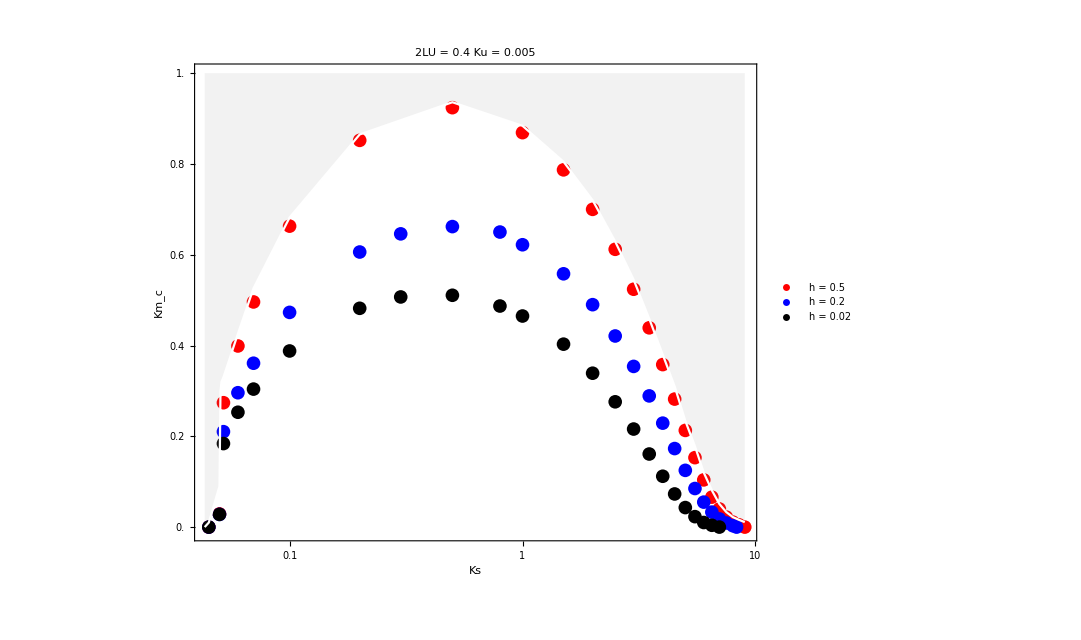

```mathematica
ma11 = Show[ListLogLinearPlot[{Transpose[{{0.045,0.05,0.052,0.06,0.07,0.1,0.2,0.5,1.0,1.5,2.0,2.5,3.0,3.5,4.0,4.5,5.0,5.5,6.0,6.5,7.0,7.5,8.0,8.5,9.0},{0,0.029,0.274,0.399,0.496,0.663,0.852,0.924, 0.869,0.787,0.7,0.612,0.524,0.439,0.358,0.282,0.213,0.153,0.104,0.066,0.04,0.022,0.011,0.005,0}}],Transpose[{{0.045,0.05,0.052,0.06,0.07,0.1,0.2,0.3,0.5,0.8,1.0,1.5,2.0,2.5,3.0,3.5,4.0,4.5,5.0,5.5,6.0,6.5,7.0,7.5,8.0,8.3},{0,0.028,0.2102,0.296,0.361,0.473,0.606,0.646,0.662,0.65,0.622,0.558,0.49,0.421,0.354,0.289, 0.229,0.173,0.125,0.085,0.055,0.033,0.018,0.009,0.003,0}}],Transpose[{{0.045,0.05,0.052,0.06,0.07,0.1,0.2,0.3,0.5,0.8,1.0,1.5,2.0,2.5,3.0,3.5,4.0,4.5,5.0,5.5,6.0,6.5,7.0},{0,0.028,0.184,0.253,0.304,0.388,0.482,0.507,0.5107,0.487,0.465, 0.403,0.339,0.276,0.216,0.161,0.112,0.073,0.043,0.023,0.0101,0.004,0}}]},PlotRange->{{0.0435,9.1},{-0.01,1.0}},PlotLegends->Placed[{Style["h = 0.5",24,FontFamily->"Times"],Style["h = 0.2",24,FontFamily->"Times"],Style["h = 0.02",24,FontFamily->"Times"]},{Right,Top}],PlotLabel->Style["2LU = 0.4       Ku = 0.005",28],PlotStyle->{Red,Blue,Black},PlotMarkers->{{"●",14}},Frame->True,FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1.0},None},{{0.05,0.10,0.5,1,5,10},None}},FrameTicksStyle->Directive[Times,24],FrameLabel->{Row[{Style["",20,Black,Bold],Style["   Ks",28]},""],Row[{Style["   ",20,Black,Bold],Style["Km_c",30,Black, Bold]},""]},AspectRatio->0.8,ImageSize->800],ListLogLinearPlot[Transpose[{{0.0432,0.045,0.05,0.0505,0.051,0.0515,0.052,0.06,0.07,0.1,0.2,0.5,1.0,1.5,2.0,2.5,3.0,3.5,4.0,4.5,5.0,5.5,6.0,6.5,7.0,7.5,8.0,8.5,9.0},{0,0.01,0.09,0.3,0.32,0.325,0.33,0.426,0.526,0.682,0.865,0.936, 0.884,0.805,0.720,0.629,0.545,0.459,0.380,0.31,0.234,0.178,0.12,0.081,0.051,0.033,0.022,0.016,0.011}}],Joined->True,PlotRange->{{-0.1,9.1},{-0.1,1.0}},PlotStyle->White,Filling->{1->{Top,Directive[Gray,Opacity[0.1]]}},AspectRatio->0.8,ImageSize->800]]
```

```mathematica
Export["ma11.pdf",ma11,"PDF","AllowRasterization"->False];
```

#### LU = 0.4 so that 2LU = 0.8

h = 0.5

```mathematica
critKmvsKsh05a001LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.01,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,1,3,3.3,3.5,3.6,3.605,3.607,3.608,3.61,3.63,3.7,4}}]
```

{{0,0.602353},{0.1,0.621415},{0.2,0.634519},{0.3,0.643873},{0.5,0.656124},{0.6,0.660313},{0.7,0.663692},{0.8,0.666472},{0.9,0.668797},{1,0.670768},{3,0.685149},{3.3,0.685926},{3.5,0.686376},{3.6,0.686584},{3.605,0.686594},{3.607,0.686598},{3.608,0.6866},{3.61,0.686604},{3.63,0.686644},{3.7,0.686781},{4,0.687317}}

```mathematica
critKmvsKsh05a001bLU04=Table[{Km,fxptHardmeta[1,0,0.005,0.03,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,1,1.2,1.21,1.212,1.213,1.216,1.217,1.22,1.23,1.3,2,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1,0},{1.2,0},{1.21,0},{1.212,0},{1.213,0.170519},{1.216,0.178892},{1.217,0.180556},{1.22,0.184625},{1.23,0.194103},{1.3,0.227765},{2,0.326538},{3,0.369493}}

```mathematica
critKmvsKsh05a00LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.05,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,1,3,3.3,3.5,3.6,3.605,3.607,3.608,3.61,3.63,3.7,4}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1,0},{3,0},{3.3,0},{3.5,0},{3.6,0},{3.605,0},{3.607,0},{3.608,0.168774},{3.61,0.171903},{3.63,0.181439},{3.7,0.195704},{4,0.22385}}

```mathematica
critKmvsKsh05a001LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.06,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,1,3,4,4.5,4.6,4.65,4.66,4.67,4.674,4.675,4.676,4.68,4.7,5}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1,0},{3,0},{4,0},{4.5,0},{4.6,0},{4.65,0},{4.66,0},{4.67,0},{4.674,0},{4.675,0.160439},{4.676,0.161849},{4.68,0.164641},{4.7,0.171202},{5,0.201465}}

```mathematica
critKmvsKsh05a002LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.07,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,1,3,4,5,5.5,5.6,5.64,5.641,5.642,5.643,5.65,5.7,5.8,6,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{1,0},{3,0},{4,0},{5,0},{5.5,0},{5.6,0},{5.64,0},{5.641,0},{5.642,0.153809},{5.643,0.154765},{5.65,0.158165},{5.7,0.167888},{5.8,0.177912},{6,0.19036},{7,0.221441}}

```mathematica
critKmvsKsh05a0LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.1,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,1,3,5,7,7.3,7.9,7.99,7.996,7.997,7.998,8}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1,0},{3,0},{5,0},{7,0},{7.3,0},{7.9,0},{7.99,0},{7.996,0},{7.997,0.138344},{7.998,0.139452},{8,0.140555}}

```mathematica
critKmvsKsh05a1LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.2,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,1,3,5,7,10,12,12.3,12.325,12.326,12.33,12.5,13}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1,0},{3,0},{5,0},{7,0},{10,0},{12,0},{12.3,0},{12.325,0},{12.326,0.120148},{12.33,0.121734},{12.5,0.133611},{13,0.146743}}

```mathematica
critKmvsKsh05a2LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.5,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,0.91,0.92,0.93,1,3,5,6,7,12,15,16,16.2,16.21,16.217,16.218,16.22}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{0.91,0},{0.92,0},{0.93,0},{1,0},{3,0},{5,0},{6,0},{7,0},{12,0},{15,0},{16,0},{16.2,0},{16.21,0},{16.217,0},{16.218,0.108179},{16.22,0.109186}}

```mathematica
critKmvsKsh05a3LU04=Table[{Km,fxptHardmeta[1,0,0.005,1.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,13,15,16,17,17.7,17.701,17.702,17.703,17.71,17.72,17.73,17.8,18,20}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{13,0},{15,0},{16,0},{17,0},{17.7,0},{17.701,0.104401},{17.702,0.104974},{17.703,0.105285},{17.71,0.106497},{17.72,0.107543},{17.73,0.108334},{17.8,0.111842},{18,0.117426},{20,0.139054}}

```mathematica
critKmvsKsh05a4LU04=Table[{Km,fxptHardmeta[1,0,0.005,1.5,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,13,15,16,17,18,18.1,18.108,18.109,18.11,18.13,18.15,18.2,18.3,19}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{13,0},{15,0},{16,0},{17,0},{18,0},{18.1,0},{18.108,0},{18.109,0},{18.11,0.103625},{18.13,0.106381},{18.15,0.107749},{18.2,0.110095},{18.3,0.113275},{19,0.124833}}

```mathematica
critKmvsKsh05a5LU04=Table[{Km,fxptHardmeta[1,0,0.005,2.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,13,15,16,17,18,18.2,18.22,18.223,18.224,18.225,18.23,18.3,19,20}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{13,0},{15,0},{16,0},{17,0},{18,0},{18.2,0},{18.22,0},{18.223,0},{18.224,0.103143},{18.225,0.10345},{18.23,0.104362},{18.3,0.108883},{19,0.122596},{20,0.132174}}

```mathematica
critKmvsKsh05a6LU04=Table[{Km,fxptHardmeta[1,0,0.005,3.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,13,15,16,17,18,18.1,18.14,18.143,18.144,18.145,18.15,18.2,19,20}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{13,0},{15,0},{16,0},{17,0},{18,0},{18.1,0},{18.14,0},{18.143,0},{18.144,0.102399},{18.145,0.102808},{18.15,0.103793},{18.2,0.107418},{19,0.122791},{20,0.131867}}

```mathematica
critKmvsKsh05a7LU04=Table[{Km,fxptHardmeta[1,0,0.005,3.5,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,15,16,17,18,18.03,18.036,18.037,18.04,18.07,18.1,18.2,19.1,19.2,18.3,19,20}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{15,0},{16,0},{17,0},{18,0},{18.03,0},{18.036,0},{18.037,0.102328},{18.04,0.103207},{18.07,0.10606},{18.1,0.107638},{18.2,0.111103},{19.1,0.124861},{19.2,0.125856},{18.3,0.11356},{19,0.12381},{20,0.132414}}

```mathematica
critKmvsKsh05a8LU04=Table[{Km,fxptHardmeta[1,0,0.005,4.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,15,16,17,17.9,17.906,17.907,17.91,17.93,18,20}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{15,0},{16,0},{17,0},{17.9,0},{17.906,0},{17.907,0.102163},{17.91,0.103127},{17.93,0.105314},{18,0.108797},{20,0.133161}}

```mathematica
critKmvsKsh05a9LU04=Table[{Km,fxptHardmeta[1,0,0.005,4.5,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,15,16,17,17.3,17.7,17.76,17.761,17.762,17.77,17.8,18,20}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{15,0},{16,0},{17,0},{17.3,0},{17.7,0},{17.76,0},{17.761,0},{17.762,0.102223},{17.77,0.103903},{17.8,0.106287},{18,0.112888},{20,0.134017}}

```mathematica
critKmvsKsh05a10LU04=Table[{Km,fxptHardmeta[1,0,0.005,5.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,15,16,17,17.3,17.6,17.605,17.606,17.61,17.62,17.7,17.8,18,20}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{15,0},{16,0},{17,0},{17.3,0},{17.6,0},{17.605,0},{17.606,0.102114},{17.61,0.103306},{17.62,0.104548},{17.7,0.10881},{17.8,0.111818},{18,0.115975},{20,0.134931}}

```mathematica
critKmvsKsh05a11LU04=Table[{Km,fxptHardmeta[1,0,0.005,5.5,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,15,16,17,17.3,17.4,17.44,17.442,17.443,17.45,17.5,18,20}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{15,0},{16,0},{17,0},{17.3,0},{17.4,0},{17.44,0},{17.442,0},{17.443,0.102522},{17.45,0.103882},{17.5,0.107331},{18,0.118581},{20,0.135872}}

```mathematica
critKmvsKsh05a12LU04=Table[{Km,fxptHardmeta[1,0,0.005,6.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,15,16,17,17.2,17.27,17.272,17.273,17.28,17.3,18,20}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{15,0},{16,0},{17,0},{17.2,0},{17.27,0},{17.272,0},{17.273,0.102362},{17.28,0.103867},{17.3,0.105672},{18,0.120877},{20,0.136821}}

```mathematica
critKmvsKsh05a13LU04=Table[{Km,fxptHardmeta[1,0,0.005,7.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,15,16,16.9,16.92,16.9208,16.9209,16.921,16.923,16.925,16.926,17,18,20}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{15,0},{16,0},{16.9,0},{16.92,0},{16.9208,0},{16.9209,0.102191},{16.921,0.102307},{16.923,0.10308},{16.925,0.10349},{16.926,0.103656},{17,0.108391},{18,0.124844},{20,0.138697}}

```mathematica
critKmvsKsh05a13bLU04=Table[{Km,fxptHardmeta[1,0,0.005,7.5,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,15,16,16.7,16.74,16.7403,16.7404,16.741,16.742,16.743,16.75,16.8,16.9,17}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{15,0},{16,0},{16.7,0},{16.74,0},{16.7403,0},{16.7404,0.102274},{16.741,0.102678},{16.742,0.103019},{16.743,0.103265},{16.75,0.104323},{16.8,0.107619},{16.9,0.1111},{17,0.113541}}

```mathematica
critKmvsKsh05a14LU04=Table[{Km,fxptHardmeta[1,0,0.005,8.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,15,16,16.55,16.554,16.557,16.558,16.56,16.6,16.7,17,18,20}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{15,0},{16,0},{16.55,0},{16.554,0},{16.557,0},{16.558,0.102665},{16.56,0.103296},{16.6,0.106829},{16.7,0.110672},{17,0.117012},{18,0.128232},{20,0.140509}}

```mathematica
critKmvsKsh05a15LU04=Table[{Km,fxptHardmeta[1,0,0.005,9.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,15,16,16.1,16.15,16.18,16.186,16.187,16.19,16.2,16.3,17}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{15,0},{16,0},{16.1,0},{16.15,0},{16.18,0},{16.186,0},{16.187,0.102827},{16.19,0.103662},{16.2,0.104951},{16.3,0.109912},{17,0.122199}}

```mathematica
critKmvsKsh05a16LU04=Table[{Km,fxptHardmeta[1,0,0.005,10.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,15,15.8,15.81,15.8101,15.8102,15.811,15.813,15.82,15.83,15.9,16,17}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{15,0},{15.8,0},{15.81,0},{15.8101,0},{15.8102,0.102648},{15.811,0.10315},{15.813,0.103699},{15.82,0.104735},{15.83,0.105675},{15.9,0.109243},{16,0.112268},{17,0.126236}}

```mathematica
critKmvsKsh05a17LU04=Table[{Km,fxptHardmeta[1,0,0.005,11.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,14,15,15.3,15.4,15.42,15.429,15.43,15.5,16}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{14,0},{15,0},{15.3,0},{15.4,0},{15.42,0},{15.429,0},{15.43,0.102812},{15.5,0.10863},{16,0.11938}}

```mathematica
critKmvsKsh05a18LU04=Table[{Km,fxptHardmeta[1,0,0.005,12.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,14,14.8,15,15.04,15.046,15.047,15.05,15.07,15.1,16}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{14,0},{14.8,0},{15,0},{15.04,0},{15.046,0},{15.047,0.103042},{15.05,0.104107},{15.07,0.106282},{15.1,0.108044},{16,0.124186}}

```mathematica
critKmvsKsh05a19LU04=Table[{Km,fxptHardmeta[1,0,0.005,13.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,14,14.6,14.66,14.661,14.662,14.663,14.67,14.7,15}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{14,0},{14.6,0},{14.66,0},{14.661,0},{14.662,0.103394},{14.663,0.103841},{14.67,0.105095},{14.7,0.107452},{15,0.11599}}

```mathematica
critKmvsKsh05a20LU04=Table[{Km,fxptHardmeta[1,0,0.005,14.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,14,14.2,14.27,14.274,14.275,14.278,14.28,14.3,15}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{14,0},{14.2,0},{14.27,0},{14.274,0},{14.275,0.103388},{14.278,0.104489},{14.28,0.104846},{14.3,0.10681},{15,0.121932}}

```mathematica
critKmvsKsh05a20bLU04=Table[{Km,fxptHardmeta[1,0,0.005,15.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,13.8,13.88,13.886,13.887,13.89,13.9,14,15}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{13.8,0},{13.88,0},{13.886,0},{13.887,0.103685},{13.89,0.104704},{13.9,0.106027},{14,0.110985},{15,0.126298}}

```mathematica
critKmvsKsh05a21LU04=Table[{Km,fxptHardmeta[1,0,0.005,16.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,13,13.4,13.48,13.49,13.497,13.498,13.5,13.6,14,14.3,15}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{13,0},{13.4,0},{13.48,0},{13.49,0},{13.497,0},{13.498,0.103947},{13.5,0.104702},{13.6,0.110816},{14,0.119286},{14.3,0.123215},{15,0.129861}}

```mathematica
critKmvsKsh05a22LU04=Table[{Km,fxptHardmeta[1,0,0.005,17.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,12,13,13.1,13.107,13.108,13.11,13.12,13.13,13.2,13.5,13.6,14}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{12,0},{13,0},{13.1,0},{13.107,0},{13.108,0.103899},{13.11,0.104869},{13.12,0.106328},{13.13,0.107199},{13.2,0.110659},{13.5,0.117717},{13.6,0.119327},{14,0.124407}}

```mathematica
critKmvsKsh05a23LU04=Table[{Km,fxptHardmeta[1,0,0.005,18.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,12,12.7,12.71,12.717,12.718,12.72,12.8,13,14,14.3,15}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{12,0},{12.7,0},{12.71,0},{12.717,0},{12.718,0.104542},{12.72,0.105185},{12.8,0.110508},{13,0.115876},{14,0.12838},{14.3,0.130834},{15,0.135588}}

```mathematica
critKmvsKsh05a24LU04=Table[{Km,fxptHardmeta[1,0,0.005,19.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,12,12.3,12.32,12.326,12.327,12.33,12.4,12.6,12.71,13,14}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{12,0},{12.3,0},{12.32,0},{12.326,0},{12.327,0.104698},{12.33,0.105589},{12.4,0.110359},{12.6,0.115895},{12.71,0.117972},{13,0.122231},{14,0.131694}}

```mathematica
critKmvsKsh05a25LU04=Table[{Km,fxptHardmeta[1,0,0.005,20.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,11.9,11.93,11.935,11.936,11.94,12,13}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{11.9,0},{11.93,0},{11.935,0},{11.936,0.10505},{11.94,0.106032},{12,0.110204},{13,0.126748}}

```mathematica
critKmvsKsh05a26LU04=Table[{Km,fxptHardmeta[1,0,0.005,21.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,11.5,11.54,11.543,11.544,11.55,11.55,11.6,11.7,12,13}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{11.5,0},{11.54,0},{11.543,0},{11.544,0.104941},{11.55,0.106486},{11.55,0.106486},{11.6,0.110039},{11.7,0.113536},{12,0.119586},{13,0.130385}}

```mathematica
critKmvsKsh05a27LU04=Table[{Km,fxptHardmeta[1,0,0.005,22.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,11,11.1,11.15,11.152,11.153,11.154,11.16,11.2,11.3,12,13}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{11,0},{11.1,0},{11.15,0},{11.152,0},{11.153,0.105584},{11.154,0.105905},{11.16,0.10694},{11.2,0.109856},{11.3,0.113522},{12,0.124897},{13,0.133473}}

```mathematica
critKmvsKsh05a28LU04=Table[{Km,fxptHardmeta[1,0,0.005,23.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,9,10,10.7,10.76,10.7604,10.7605,10.761,10.77,10.78,11,12,13}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{9,0},{10,0},{10.7,0},{10.76,0},{10.7604,0},{10.7605,0.105396},{10.761,0.105729},{10.77,0.107385},{10.78,0.108327},{11,0.116033},{12,0.128949},{13,0.136173}}

```mathematica
critKmvsKsh05a29LU04=Table[{Km,fxptHardmeta[1,0,0.005,24.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,10,10.3,10.36,10.368,10.369,10.37,10.38,10.4,10.6,11}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{10,0},{10.3,0},{10.36,0},{10.368,0},{10.369,0.105895},{10.37,0.106273},{10.38,0.10782},{10.4,0.109392},{10.6,0.116074},{11,0.122722}}

```mathematica
critKmvsKsh05a30LU04=Table[{Km,fxptHardmeta[1,0,0.005,25.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,9,9.5,9.9,9.97,9.976,9.977,9.98,10,11}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{9,0},{9.5,0},{9.9,0},{9.97,0},{9.976,0},{9.977,0.106058},{9.98,0.106946},{10,0.109075},{11,0.127339}}

```mathematica
critKmvsKsh05a31LU04=Table[{Km,fxptHardmeta[1,0,0.005,26.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,9,9.5,9.58,9.584,9.585,9.59,9.6,9.8,10,11}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{9,0},{9.5,0},{9.58,0},{9.584,0},{9.585,0.106176},{9.59,0.107501},{9.6,0.10865},{9.8,0.116155},{10,0.120014},{11,0.131018}}

```mathematica
critKmvsKsh05a32LU04=Table[{Km,fxptHardmeta[1,0,0.005,27.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,9,9.1,9.19,9.193,9.194,9.2,9.3,10,11}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{9,0},{9.1,0},{9.19,0},{9.193,0},{9.194,0.106808},{9.2,0.107994},{9.3,0.113406},{10,0.125486},{11,0.134124}}

```mathematica
critKmvsKsh05a33LU04=Table[{Km,fxptHardmeta[1,0,0.005,28.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,7,8,8.8,8.801,8.802,8.81,8.82,8.9,9,9.1,10,11}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{7,0},{8,0},{8.8,0},{8.801,0},{8.802,0.106899},{8.81,0.108445},{8.82,0.109423},{8.9,0.113358},{9,0.116227},{9.1,0.118392},{10,0.129595},{11,0.136828}}

```mathematica
critKmvsKsh05a34LU04=Table[{Km,fxptHardmeta[1,0,0.005,29.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,7,8,8.4,8.405,8.409,8.41,8.42,8.5,9,9.1,10,11}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{7,0},{8,0},{8.4,0},{8.405,0},{8.409,0},{8.41,0.106751},{8.42,0.108863},{8.5,0.113295},{9,0.123273},{9.1,0.124554},{10,0.132968},{11,0.139231}}

```mathematica
critKmvsKsh05a35LU04=Table[{Km,fxptHardmeta[1,0,0.005,30.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,7,8,8.01,8.018,8.019,8.02,8.03,8.1}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{7,0},{8,0},{8.01,0},{8.018,0},{8.019,0.107267},{8.02,0.107681},{8.03,0.109251},{8.1,0.113214}}

```mathematica
critKmvsKsh05a36LU04=Table[{Km,fxptHardmeta[1,0,0.005,31.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,7,7.6,7.62,7.627,7.628,7.63,7.7,8,8.4,8.5,9}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{7,0},{7.6,0},{7.62,0},{7.627,0},{7.628,0.107555},{7.63,0.108213},{7.7,0.113108},{8,0.120454},{8.4,0.125979},{8.5,0.127081},{9,0.131694}}

```mathematica
critKmvsKsh05a37LU04=Table[{Km,fxptHardmeta[1,0,0.005,32.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,7,7.2,7.23,7.235,7.236,7.237,7.24,7.25,7.3,8}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{7,0},{7.2,0},{7.23,0},{7.235,0},{7.236,0},{7.237,0.107668},{7.24,0.10864},{7.25,0.109947},{7.3,0.112973},{8,0.126102}}

```mathematica
critKmvsKsh05a38LU04=Table[{Km,fxptHardmeta[1,0,0.005,33.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,6,6.8,6.84,6.845,6.846,6.847,6.85,6.9,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{6,0},{6.8,0},{6.84,0},{6.845,0},{6.846,0},{6.847,0.108215},{6.85,0.108995},{6.9,0.112797},{7,0.116296}}

```mathematica
critKmvsKsh05a39LU04=Table[{Km,fxptHardmeta[1,0,0.005,34.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,6,6.4,6.45,6.456,6.457,6.46,6.5,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{6,0},{6.4,0},{6.45,0},{6.456,0},{6.457,0.108544},{6.46,0.109289},{6.5,0.112567},{7,0.123817}}

```mathematica
critKmvsKsh05a40LU04=Table[{Km,fxptHardmeta[1,0,0.005,35.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,6,6.05,6.06,6.066,6.067,6.07,6.1,6.2,6.5,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{6,0},{6.05,0},{6.06,0},{6.066,0},{6.067,0.108718},{6.07,0.109517},{6.1,0.11226},{6.2,0.116243},{6.5,0.122441},{7,0.128631}}

```mathematica
critKmvsKsh05a41LU04=Table[{Km,fxptHardmeta[1,0,0.005,36.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,5,5.5,5.6,5.67,5.677,5.678,5.68,5.7,6,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{5,0},{5.5,0},{5.6,0},{5.67,0},{5.677,0},{5.678,0.109138},{5.68,0.109666},{5.7,0.11183},{6,0.120821},{7,0.13238}}

```mathematica
critKmvsKsh05a42LU04=Table[{Km,fxptHardmeta[1,0,0.005,37.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,5,5.2,5.28,5.288,5.289,5.29,5.3,5.4,5.5,6,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{5,0},{5.2,0},{5.28,0},{5.288,0},{5.289,0.109374},{5.29,0.109688},{5.3,0.111161},{5.4,0.116111},{5.5,0.118808},{6,0.1267},{7,0.135506}}

```mathematica
critKmvsKsh05a43LU04=Table[{Km,fxptHardmeta[1,0,0.005,38.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,4,4.8,4.89,4.899,4.9,5,5.2,5.5,6,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{4,0},{4.8,0},{4.89,0},{4.899,0},{4.9,0.109316},{5,0.116003},{5.2,0.120926},{5.5,0.125575},{6,0.130934},{7,0.138206}}

```mathematica
critKmvsKsh05a44LU04=Table[{Km,fxptHardmeta[1,0,0.005,39.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,4,4.5,4.51,4.512,4.513,4.52,4.6,4.7,5,5.2,5.5,6,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{4,0},{4.5,0},{4.51,0},{4.512,0},{4.513,0.110003},{4.52,0.111306},{4.6,0.115858},{4.7,0.118795},{5,0.1243},{5.2,0.126925},{5.5,0.13013},{6,0.13435},{7,0.140593}}

```mathematica
critKmvsKsh05a45LU04=Table[{Km,fxptHardmeta[1,0,0.005,40.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,4,4.1,4.12,4.124,4.125,4.13,4.2,4.3,5,6,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{4,0},{4.1,0},{4.12,0},{4.124,0},{4.125,0.109773},{4.13,0.111206},{4.2,0.115662},{4.3,0.118761},{5,0.129257},{6,0.137248},{7,0.142734}}

```mathematica
critKmvsKsh05a46LU04=Table[{Km,fxptHardmeta[1,0,0.005,41.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,3,3.7,3.73,3.738,3.739,3.74,3.75,3.8,3.9,4,5,6,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{3,0},{3.7,0},{3.73,0},{3.738,0},{3.739,0.11038},{3.74,0.110768},{3.75,0.112308},{3.8,0.115399},{3.9,0.118705},{4,0.121009},{5,0.133055},{6,0.139779},{7,0.144678}}

```mathematica
critKmvsKsh05a47LU04=Table[{Km,fxptHardmeta[1,0,0.005,42.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,2,3,3.35,3.353,3.354,3.36,3.4,3.5,4,5,6,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{2,0},{3,0},{3.35,0},{3.353,0},{3.354,0.110921},{3.36,0.112102},{3.4,0.115034},{3.5,0.118619},{4,0.127238},{5,0.136196},{6,0.142031},{7,0.146458}}

```mathematica
critKmvsKsh05a48LU04=Table[{Km,fxptHardmeta[1,0,0.005,43.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,2,2.5,2.9,2.95,2.96,2.968,2.969,2.97,3,3.5,4,5,6,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{2,0},{2.5,0},{2.9,0},{2.95,0},{2.96,0},{2.968,0},{2.969,0.111017},{2.97,0.111414},{3,0.114503},{3.5,0.126036},{4,0.131572},{5,0.138897},{6,0.144061},{7,0.148098}}

```mathematica
critKmvsKsh05a49LU04=Table[{Km,fxptHardmeta[1,0,0.005,44.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,2,2.5,2.58,2.585,2.586,2.59,2.6,2.7,2.8,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{2,0},{2.5,0},{2.58,0},{2.585,0},{2.586,0.111499},{2.59,0.112453},{2.6,0.11362},{2.7,0.118323},{2.8,0.120945},{3,0.124642}}

```mathematica
critKmvsKsh05a50LU04=Table[{Km,fxptHardmeta[1,0,0.005,45.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,1,2,2.1,2.2,2.203,2.204,2.21,2.22,2.3,2.6,2.7,2.8,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{1,0},{2,0},{2.1,0},{2.2,0},{2.203,0},{2.204,0.111743},{2.21,0.113084},{2.22,0.114141},{2.3,0.11808},{2.6,0.124681},{2.7,0.126175},{2.8,0.127506},{3,0.129822}}

```mathematica
critKmvsKsh05a51LU04=Table[{Km,fxptHardmeta[1,0,0.005,46.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,1,1.8,1.82,1.823,1.824,1.83,1.9,2,2.1,2.2,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{1,0},{1.8,0},{1.82,0},{1.823,0},{1.824,0.111973},{1.83,0.113448},{1.9,0.117728},{2,0.120753},{2.1,0.12293},{2.2,0.124703},{3,0.133696}}

```mathematica
critKmvsKsh05a52LU04=Table[{Km,fxptHardmeta[1,0,0.005,47.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,1,1.4,1.44,1.445,1.446,1.447,1.45,1.5,2}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{1,0},{1.4,0},{1.44,0},{1.445,0},{1.446,0},{1.447,0.11237},{1.45,0.113389},{1.5,0.117185},{2,0.127644}}

```mathematica
critKmvsKsh05a53LU04=Table[{Km,fxptHardmeta[1,0,0.005,48.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,1,1.07,1.072,1.074,1.075,1.08,1.1,1.2,1.3,1.5,2,2.1,2.2,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{1,0},{1.07,0},{1.072,0},{1.074,0},{1.075,0.11319},{1.08,0.114319},{1.1,0.116175},{1.2,0.120288},{1.3,0.122758},{1.5,0.126286},{2,0.132145},{2.1,0.133067},{2.2,0.133936},{3,0.139574}}

```mathematica
critKmvsKsh05a54LU04=Table[{Km,fxptHardmeta[1,0,0.005,49.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.7,0.71,0.7108,0.7109,0.711,0.712,0.72,0.8,1}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.7,0},{0.71,0},{0.7108,0},{0.7109,0.113449},{0.711,0.11359},{0.712,0.114088},{0.72,0.115452},{0.8,0.119768},{1,0.124594}}

```mathematica
critKmvsKsh05a55LU04=Table[{Km,fxptHardmeta[1,0,0.005,50.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.37,0.371,0.372,0.38,0.39,0.4,0.5,0.7,0.8,1}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.37,0},{0.371,0},{0.372,0.114912},{0.38,0.116509},{0.39,0.117472},{0.4,0.118179},{0.5,0.122067},{0.7,0.126194},{0.8,0.127711},{1,0.130236}}

```mathematica
critKmvsKsh05a56LU04=Table[{Km,fxptHardmeta[1,0,0.005,51.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.12,0.122,0.123,0.13,0.15,0.2}}]
```

{{0,0},{0.1,0},{0.12,0},{0.122,0},{0.123,0.117753},{0.13,0.119339},{0.15,0.121176},{0.2,0.12339}}

```mathematica
critKmvsKsh05a57LU04=Table[{Km,fxptHardmeta[1,0,0.005,52.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.03,0.032,0.033,0.037,0.04,0.05,0.1,0.12,0.122,0.123,0.13,0.15,0.2,0.3,0.4}}]
```

{{0,0},{0.03,0},{0.032,0},{0.033,0.122074},{0.037,0.124036},{0.04,0.12473},{0.05,0.126033},{0.1,0.128269},{0.12,0.128732},{0.122,0.128774},{0.123,0.128794},{0.13,0.128934},{0.15,0.129299},{0.2,0.130075},{0.3,0.131347},{0.4,0.13244}}

```mathematica
critKmvsKsh05a58LU04=Table[{Km,fxptHardmeta[1,0,0.005,53.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.009,0.01,0.02,0.05,0.1,0.12,0.122,0.123,0.13,0.15,0.2}}]
```

{{0,0},{0.009,0},{0.01,0.126769},{0.02,0.130622},{0.05,0.132322},{0.1,0.133231},{0.12,0.133487},{0.122,0.133511},{0.123,0.133523},{0.13,0.133605},{0.15,0.13383},{0.2,0.134341}}

```mathematica
critKmvsKsh05a59LU04=Table[{Km,fxptHardmeta[1,0,0.005,54.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.001,0.0016,0.0017,0.002,0.01,0.02,0.05,0.1,0.2}}]
```

{{0,0},{0.001,0},{0.0016,0},{0.0017,0.129049},{0.002,0.13044},{0.01,0.13471},{0.02,0.135529},{0.05,0.136276},{0.1,0.136841},{0.2,0.137665}}

```mathematica
critKmvsKsh05a60LU04=Table[{Km,fxptHardmeta[1,0,0.005,55.0,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.005,0.01,0.02,0.05,0.1,0.12,0.122,0.123,0.13,0.15,0.2}}]
```

{{0,0.13629},{0.005,0.138072},{0.01,0.138543},{0.02,0.138927},{0.05,0.139364},{0.1,0.139774},{0.12,0.139915},{0.122,0.139929},{0.123,0.139936},{0.13,0.139984},{0.15,0.140117},{0.2,0.140439}}

h = 0.2

```mathematica
critKmvsKsh02a001LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.01,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,1,1.3,1.4,1.42,1.4201,1.4202,1.5,2,2.3,2.5,3}}]
```

{{0,0.605203},{0.1,0.648646},{0.2,0.678896},{0.3,0.700072},{0.5,0.726719},{0.6,0.735468},{0.7,0.742374},{0.8,0.747949},{0.9,0.752537},{1,0.756374},{1.3,0.764841},{1.4,0.76696},{1.42,0.767353},{1.4201,0.767355},{1.4202,0.767357},{1.5,0.76883},{2,0.775621},{2.3,0.778385},{2.5,0.779884},{3,0.782806}}

```mathematica
critKmvsKsh02a001BLU04=Table[{Km,fxptHardmeta[1,0,0.005,0.03,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.63,0.633,0.638,0.639,0.64,0.65,0.68,0.7,0.8,0.9,1}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.63,0},{0.633,0},{0.638,0},{0.639,0.237457},{0.64,0.242901},{0.65,0.269528},{0.68,0.308748},{0.7,0.326548},{0.8,0.384548},{0.9,0.42049},{1,0.446178}}

```mathematica
critKmvsKsh02a00LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.05,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,1,1.3,1.4,1.42,1.4201,1.4202,1.5,2,2.3,2.5,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1,0},{1.3,0},{1.4,0},{1.42,0},{1.4201,0},{1.4202,0.258326},{1.5,0.320503},{2,0.407736},{2.3,0.4306},{2.5,0.441652},{3,0.46115}}

```mathematica
critKmvsKsh02a00LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.06,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,1,1.3,1.4,1.5,1.7,1.71,1.713,1.719,1.72,1.8,2,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1,0},{1.3,0},{1.4,0},{1.5,0},{1.7,0},{1.71,0},{1.713,0},{1.719,0},{1.72,0.253833},{1.8,0.305851},{2,0.348764},{3,0.421958}}

```mathematica
critKmvsKsh02a001LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.07,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,1,1.3,1.4,1.5,1.7,1.8,1.9,1.98,1.982,1.983,2,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1,0},{1.3,0},{1.4,0},{1.5,0},{1.7,0},{1.8,0},{1.9,0},{1.98,0},{1.982,0},{1.983,0.246927},{2,0.267167},{3,0.388555}}

```mathematica
critKmvsKsh02a0LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.1,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,1,2,2.3,2.5,2.6,2.61,2.613,2.619,2.62,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1,0},{2,0},{2.3,0},{2.5,0},{2.6,0},{2.61,0},{2.613,0},{2.619,0},{2.62,0.229998},{3,0.305722}}

```mathematica
critKmvsKsh02a1LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.2,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,0.8,0.9,1,3,3.3,3.8,3.83,3.89,3.898,3.899,3.9,4,5}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{0.8,0},{0.9,0},{1,0},{3,0},{3.3,0},{3.8,0},{3.83,0},{3.89,0},{3.898,0},{3.899,0.194669},{3.9,0.197343},{4,0.223597},{5,0.278277}}

```mathematica
critKmvsKsh02a2LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.3,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,1,3,4,4.6,4.605,4.606,4.61,4.62,4.63,4.7,4.8,5}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{1,0},{3,0},{4,0},{4.6,0},{4.605,0},{4.606,0.181628},{4.61,0.18476},{4.62,0.18881},{4.63,0.19157},{4.7,0.202945},{4.8,0.212639},{5,0.225398}}

```mathematica
critKmvsKsh02a3LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.5,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,1,3,5,5.3,5.36,5.367,5.368,5.37,5.38,5.4,5.5,6}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{1,0},{3,0},{5,0},{5.3,0},{5.36,0},{5.367,0},{5.368,0.165548},{5.37,0.167792},{5.38,0.171945},{5.4,0.176386},{5.5,0.187891},{6,0.212024}}

```mathematica
critKmvsKsh02a4LU04=Table[{Km,fxptHardmeta[1,0,0.005,1.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.8,0.9,1,3,5,6,6.07,6.078,6.079,6.08,6.1,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.8,0},{0.9,0},{1,0},{3,0},{5,0},{6,0},{6.07,0},{6.078,0},{6.079,0.153024},{6.08,0.154009},{6.1,0.159979},{7,0.198527}}

```mathematica
critKmvsKsh02a5LU04=Table[{Km,fxptHardmeta[1,0,0.005,1.5,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,1,2,4,6,6.3,6.302,6.303,6.31,6.8,7,9}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{1,0},{2,0},{4,0},{6,0},{6.3,0},{6.302,0},{6.303,0.150866},{6.31,0.15288},{6.8,0.181002},{7,0.18622},{9,0.210735}}

```mathematica
critKmvsKsh05cLU04=Table[{Km,fxptHardmeta[1,0,0.005,2.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,1,3,5,6,6.3,6.37,6.371,6.372,6.38,6.8,7,8,9}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{1,0},{3,0},{5,0},{6,0},{6.3,0},{6.37,0},{6.371,0},{6.372,0.149761},{6.38,0.15147},{6.8,0.175501},{7,0.180944},{8,0.197016},{9,0.205643}}

```mathematica
critKmvsKsh02dLU04=Table[{Km,fxptHardmeta[1,0,0.005,2.5,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,1,3,5,6,6.3,6.36,6.369,6.37,6.4,6.5,6.6,6.7,7}}]
```

{{0,0},{0.1,0},{0.2,0},{1,0},{3,0},{5,0},{6,0},{6.3,0},{6.36,0},{6.369,0},{6.37,0.148863},{6.4,0.153377},{6.5,0.161275},{6.6,0.166335},{6.7,0.17026},{7,0.178804}}

```mathematica
critKmvsKsh02eLU04=Table[{Km,fxptHardmeta[1,0,0.005,3.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,1,3,5,6,6.3,6.32,6.329,6.33,6.34,6.4,7}}]
```

{{0,0},{0.1,0},{0.2,0},{1,0},{3,0},{5,0},{6,0},{6.3,0},{6.32,0},{6.329,0},{6.33,0.14814},{6.34,0.149881},{6.4,0.156133},{7,0.178236}}

```mathematica
critKmvsKsh02fLU04=Table[{Km,fxptHardmeta[1,0,0.005,3.5,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.9,1,3,5,6,6.2,6.26,6.267,6.268,6.27,6.3,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.9,0},{1,0},{3,0},{5,0},{6,0},{6.2,0},{6.26,0},{6.267,0},{6.268,0.147666},{6.27,0.148037},{6.3,0.152042},{7,0.178492}}

```mathematica
critKmvsKsh02gLU04=Table[{Km,fxptHardmeta[1,0,0.005,4.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,1,4,6,6.1,6.18,6.189,6.19,6.2,6.3,7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{1,0},{4,0},{6,0},{6.1,0},{6.18,0},{6.189,0},{6.19,0.146995},{6.2,0.148689},{6.3,0.15753},{7,0.179184}}

```mathematica
critKmvsKsh02hLU04=Table[{Km,fxptHardmeta[1,0,0.005,4.5,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,1,3,5,6,6.1,6.101,6.102,6.12,6.2}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{1,0},{3,0},{5,0},{6,0},{6.1,0},{6.101,0},{6.102,0.146356},{6.12,0.149229},{6.2,0.15624}}

```mathematica
critKmvsKsh02iLU04=Table[{Km,fxptHardmeta[1,0,0.005,5.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,1,3,4,5,6,6.01,6.1}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{1,0},{3,0},{4,0},{5,0},{6,0},{6.01,0.146363},{6.1,0.155474}}

```mathematica
critKmvsKsh02jLU04=Table[{Km,fxptHardmeta[1,0,0.005,5.5,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,1,3,4,5,5.9,5.907,5.908,5.91,6}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{1,0},{3,0},{4,0},{5,0},{5.9,0},{5.907,0},{5.908,0.1454},{5.91,0.145831},{6,0.155115}}

```mathematica
critKmvsKsh02kLU04=Table[{Km,fxptHardmeta[1,0,0.005,6.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,1,3,4,5,5.3,5.8,5.803,5.804,5.81,5.82}}]
```

{{0,0},{0.1,0},{0.2,0},{1,0},{3,0},{4,0},{5,0},{5.3,0},{5.8,0},{5.803,0},{5.804,0.1448},{5.81,0.146096},{5.82,0.147734}}

```mathematica
critKmvsKsh02lLU04=Table[{Km,fxptHardmeta[1,0,0.005,6.5,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,1,3,5,5.69,5.697,5.698,5.7}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{1,0},{3,0},{5,0},{5.69,0},{5.697,0},{5.698,0.144431},{5.7,0.144934}}

```mathematica
critKmvsKsh02mLU04=Table[{Km,fxptHardmeta[1,0,0.005,7.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,1,3,5,5.5,5.58,5.588,5.589,5.59,5.6}}]
```

{{0,0},{0.1,0},{0.2,0},{1,0},{3,0},{5,0},{5.5,0},{5.58,0},{5.588,0},{5.589,0.143858},{5.59,0.144154},{5.6,0.146319}}

```mathematica
critKmvsKsh02nLU04=Table[{Km,fxptHardmeta[1,0,0.005,7.5,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,1,3,5,5.4,5.47,5.478,5.479,5.48,5.5,5.6}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{1,0},{3,0},{5,0},{5.4,0},{5.47,0},{5.478,0},{5.479,0.143511},{5.48,0.143834},{5.5,0.147672},{5.6,0.156065}}

```mathematica
critKmvsKsh02oLU04=Table[{Km,fxptHardmeta[1,0,0.005,8.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,1,2,3,4,5,5.3,5.366,5.367,5.37,5.4}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{1,0},{2,0},{3,0},{4,0},{5,0},{5.3,0},{5.366,0},{5.367,0.142936},{5.37,0.143971},{5.4,0.14897}}

```mathematica
critKmvsKsh02pLU04=Table[{Km,fxptHardmeta[1,0,0.005,9.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,1,2,3,4,5,5.1,5.14,5.141,5.142,5.15,5.2,5.3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{1,0},{2,0},{3,0},{4,0},{5,0},{5.1,0},{5.14,0},{5.141,0.142163},{5.142,0.142701},{5.15,0.145096},{5.2,0.151388},{5.3,0.157863}}

```mathematica
critKmvsKsh02qLU04=Table[{Km,fxptHardmeta[1,0,0.005,10.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.13,0.2,1,2,3,4,4.8,4.9,4.91,4.911,4.912,4.92,5}}]
```

{{0,0},{0.1,0},{0.13,0},{0.2,0},{1,0},{2,0},{3,0},{4,0},{4.8,0},{4.9,0},{4.91,0},{4.911,0},{4.912,0.140786},{4.92,0.144642},{5,0.153589}}

```mathematica
critKmvsKsh02rLU04=Table[{Km,fxptHardmeta[1,0,0.005,11.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,1,2,3,4,4.3,4.5,4.6,4.68,4.681,4.682,4.683,4.69,4.7}}]
```

{{0,0},{0.1,0},{0.2,0},{1,0},{2,0},{3,0},{4,0},{4.3,0},{4.5,0},{4.6,0},{4.68,0},{4.681,0},{4.682,0.141144},{4.683,0.142238},{4.69,0.144774},{4.7,0.146731}}

```mathematica
critKmvsKsh02sLU04=Table[{Km,fxptHardmeta[1,0,0.005,12.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.03,0.1,1,2,3,4,4.4,4.45,4.4502,4.4503,4.451,4.452,4.46,4.47,4.5}}]
```

{{0,0},{0.03,0},{0.1,0},{1,0},{2,0},{3,0},{4,0},{4.4,0},{4.45,0},{4.4502,0},{4.4503,0.14133},{4.451,0.142185},{4.452,0.14282},{4.46,0.145323},{4.47,0.147144},{4.5,0.150684}}

```mathematica
critKmvsKsh02tLU04=Table[{Km,fxptHardmeta[1,0,0.005,13.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.03,1,2,3,4,4.2,4.21,4.217,4.218,4.22,4.3}}]
```

{{0,0},{0.03,0},{1,0},{2,0},{3,0},{4,0},{4.2,0},{4.21,0},{4.217,0},{4.218,0.14227},{4.22,0.143421},{4.3,0.153531}}

```mathematica
critKmvsKsh02tLU04=Table[{Km,fxptHardmeta[1,0,0.005,14.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.02,1,2,3,3.9,3.98,3.983,3.984,3.986,3.99,4}}]
```

{{0,0},{0.02,0},{1,0},{2,0},{3,0},{3.9,0},{3.98,0},{3.983,0},{3.984,0.142156},{3.986,0.14349},{3.99,0.144863},{4,0.146958}}

```mathematica
critKmvsKsh02uLU04=Table[{Km,fxptHardmeta[1,0,0.005,15.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.01,1,2,3,3.747,3.749,3.75,3.8,4}}]
```

{{0,0},{0.01,0},{1,0},{2,0},{3,0},{3.747,0},{3.749,0},{3.75,0.14261},{3.8,0.151296},{4,0.16229}}

```mathematica
critKmvsKsh02vLU04=Table[{Km,fxptHardmeta[1,0,0.005,16.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.01,1,2,3,3.5,3.51,3.514,3.515,3.6,3.7,4}}]
```

{{0,0},{0.01,0},{1,0},{2,0},{3,0},{3.5,0},{3.51,0},{3.514,0},{3.515,0.142014},{3.6,0.154273},{3.7,0.159775},{4,0.169492}}

```mathematica
critKmvsKsh02wLU04=Table[{Km,fxptHardmeta[1,0,0.005,17.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.001,1,2,3,3.2,3.28,3.2803,3.2804,3.281,3.29,3.3,4}}]
```

{{0,0},{0.001,0},{1,0},{2,0},{3,0},{3.2,0},{3.28,0},{3.2803,0},{3.2804,0.142223},{3.281,0.143234},{3.29,0.14642},{3.3,0.148216},{4,0.174593}}

```mathematica
critKmvsKsh02xLU04=Table[{Km,fxptHardmeta[1,0,0.005,19.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.001,1,2,2.8,2.81,2.811,2.812,2.82,2.9,3,3.1,3.2}}]
```

{{0,0},{0.001,0},{1,0},{2,0},{2.8,0},{2.81,0},{2.811,0},{2.812,0.143667},{2.82,0.146762},{2.9,0.155276},{3,0.160601},{3.1,0.164416},{3.2,0.167474}}

```mathematica
critKmvsKsh02xLU04=Table[{Km,fxptHardmeta[1,0,0.005,21.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.001,1,2,2.3,2.34,2.344,2.345,2.35,2.4,2.8,3}}]
```

{{0,0},{0.001,0},{1,0},{2,0},{2.3,0},{2.34,0},{2.344,0},{2.345,0.144538},{2.35,0.146747},{2.4,0.153444},{2.8,0.169679},{3,0.174011}}

```mathematica
critKmvsKsh02yLU04=Table[{Km,fxptHardmeta[1,0,0.005,23.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.001,1,1.8,1.88,1.8806,1.8807,1.881,1.89,2,2.3,2.4,2.8,3}}]
```

{{0,0},{0.001,0},{1,0},{1.8,0},{1.88,0},{1.8806,0},{1.8807,0.144722},{1.881,0.145236},{1.89,0.14855},{2,0.158522},{2.3,0.169303},{2.4,0.171681},{2.8,0.178796},{3,0.181475}}

```mathematica
critKmvsKsh02yLU04=Table[{Km,fxptHardmeta[1,0,0.005,25.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.001,1,1.4,1.42,1.422,1.423,1.43,1.45,1.5,1.6,1.8,2}}]
```

{{0,0},{0.001,0},{1,0},{1.4,0},{1.42,0},{1.422,0},{1.423,0.146288},{1.43,0.149144},{1.45,0.152415},{1.5,0.156869},{1.6,0.162216},{1.8,0.168893},{2,0.173509}}

```mathematica
critKmvsKsh02y1LU04=Table[{Km,fxptHardmeta[1,0,0.005,27.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.9,0.97,0.975,0.976,0.98,1,1.1,1.4,2}}]
```

{{0,0},{0.1,0},{0.9,0},{0.97,0},{0.975,0},{0.976,0.147603},{0.98,0.149715},{1,0.15341},{1.1,0.160914},{1.4,0.171005},{2,0.181233}}

```mathematica
critKmvsKsh02y2LU04=Table[{Km,fxptHardmeta[1,0,0.005,29.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.5,0.55,0.554,0.555,0.56,0.57,0.6,0.7,0.8,0.9,0.97}}]
```

{{0,0},{0.1,0},{0.5,0},{0.55,0},{0.554,0},{0.555,0.150276},{0.56,0.152377},{0.57,0.15441},{0.6,0.157852},{0.7,0.163872},{0.8,0.167632},{0.9,0.170511},{0.97,0.172215}}

```mathematica
critKmvsKsh02y3LU04=Table[{Km,fxptHardmeta[1,0,0.005,31.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.21,0.2109,0.211,0.22,0.23,0.3,0.5,0.6,0.7,0.8,0.9,0.97}}]
```

{{0,0},{0.1,0},{0.2,0},{0.21,0},{0.2109,0},{0.211,0.153767},{0.22,0.157885},{0.23,0.159661},{0.3,0.16537},{0.5,0.172278},{0.6,0.174535},{0.7,0.176451},{0.8,0.178131},{0.9,0.179634},{0.97,0.180602}}

```mathematica
critKmvsKsh02y4LU04=Table[{Km,fxptHardmeta[1,0,0.005,33.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.04,0.049,0.0494,0.0495,0.05,0.1,0.11,0.2}}]
```

{{0,0},{0.02,0},{0.04,0},{0.049,0},{0.0494,0},{0.0495,0.161622},{0.05,0.162785},{0.1,0.172072},{0.11,0.172621},{0.2,0.175624}}

```mathematica
critKmvsKsh02y5LU04=Table[{Km,fxptHardmeta[1,0,0.005,35.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.009,0.0097,0.0098,0.01,0.02,0.04,0.2}}]
```

{{0,0},{0.009,0},{0.0097,0},{0.0098,0.168753},{0.01,0.170169},{0.02,0.17744},{0.04,0.179696},{0.2,0.183055}}

```mathematica
critKmvsKsh02y6LU04=Table[{Km,fxptHardmeta[1,0,0.005,36.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.003,0.0032,0.0033,0.004,0.009}}]
```

{{0,0},{0.003,0},{0.0032,0},{0.0033,0.172414},{0.004,0.175658},{0.009,0.180214}}

```mathematica
critKmvsKsh02y7LU04=Table[{Km,fxptHardmeta[1,0,0.005,37.0,Km,0.2,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.003,0.0032,0.0033,0.004,0.009}}]
```

{{0,0.177175},{0.003,0.182582},{0.0032,0.182711},{0.0033,0.182773},{0.004,0.183149},{0.009,0.184537}}

h = 0.02

```mathematica
critKmvsKsh002aa0LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.01,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.1,0.2,0.3,0.4,0.45,0.5,0.8,0.9,0.91,0.913,0.914,0.92,0.93,1,2}}]
```

{{0,0.606929},{0.02,0.620244},{0.1,0.665889},{0.2,0.707326},{0.3,0.736057},{0.4,0.7565},{0.45,0.764571},{0.5,0.771559},{0.8,0.799205},{0.9,0.805103},{0.91,0.805634},{0.913,0.805791},{0.914,0.805844},{0.92,0.806156},{0.93,0.806668},{1,0.810015},{2,0.834399}}

```mathematica
critKmvsKsh002aa01LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.03,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.1,0.2,0.3,0.4,0.48,0.4801,0.4802,0.4803,0.481,0.483,0.49,0.5}}]
```

{{0,0},{0.02,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.48,0},{0.4801,0},{0.4802,0.261373},{0.4803,0.265865},{0.481,0.275803},{0.483,0.289476},{0.49,0.315575},{0.5,0.339499}}

```mathematica
critKmvsKsh002aaLU04=Table[{Km,fxptHardmeta[1,0,0.005,0.05,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.1,0.2,0.3,0.4,0.5,0.8,0.9,0.91,0.913,0.914,0.92,0.93,1,2}}]
```

{{0,0},{0.02,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{0.8,0},{0.9,0},{0.91,0},{0.913,0},{0.914,0.328062},{0.92,0.35339},{0.93,0.371592},{1,0.4315},{2,0.604959}}

```mathematica
critKmvsKsh002aabLU04=Table[{Km,fxptHardmeta[1,0,0.005,0.06,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.03,0.1,0.4,0.9,1,1.05,1.051,1.052,1.06,1.07,1.1,1.2,1.5,2}}]
```

{{0,0},{0.02,0},{0.03,0},{0.1,0},{0.4,0},{0.9,0},{1,0},{1.05,0},{1.051,0},{1.052,0.335422},{1.06,0.358597},{1.07,0.373361},{1.1,0.401278},{1.2,0.45251},{1.5,0.524618},{2,0.578327}}

```mathematica
critKmvsKsh002abLU04=Table[{Km,fxptHardmeta[1,0,0.005,0.07,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.05,0.1,0.2,0.3,0.4,0.8,1,1.1,1.16,1.161,1.1618,1.1619,1.162,1.163,1.17,1.2,2}}]
```

{{0,0},{0.05,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.8,0},{1,0},{1.1,0},{1.16,0},{1.161,0},{1.1618,0},{1.1619,0.329112},{1.162,0.330816},{1.163,0.337758},{1.17,0.355691},{1.2,0.388599},{2,0.556227}}

```mathematica
critKmvsKsh002a0LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.1,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,0.7,1,1.3,1.39,1.396,1.397,1.4,1.8,2}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{0.7,0},{1,0},{1.3,0},{1.39,0},{1.396,0},{1.397,0.33049},{1.4,0.33993},{1.8,0.480957},{2,0.50672}}

```mathematica
critKmvsKsh002a01LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.2,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.4,0.5,1,1.7,1.76,1.7602,1.7603,1.763,1.8,2,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{1,0},{1.7,0},{1.76,0},{1.7602,0},{1.7603,0.310722},{1.763,0.321865},{1.8,0.35548},{2,0.416366},{3,0.508256}}

```mathematica
critKmvsKsh002a1LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.3,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,1,1.8,1.9,1.92,1.928,1.929,1.93,2,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{1,0},{1.8,0},{1.9,0},{1.92,0},{1.928,0},{1.929,0.328503},{1.93,0.329348},{2,0.363661},{3,0.479989}}

```mathematica
critKmvsKsh002a2LU04=Table[{Km,fxptHardmeta[1,0,0.005,0.5,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,1,1.9,2,2.1,2.11,2.112,2.113,2.12,2.13,2.2,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{1,0},{1.9,0},{2,0},{2.1,0},{2.11,0},{2.112,0},{2.113,0.345811},{2.12,0.348206},{2.13,0.351426},{2.2,0.369595},{3,0.452395}}

```mathematica
critKmvsKsh002a3LU04=Table[{Km,fxptHardmeta[1,0,0.005,1.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,0.6,1,2,2.2,2.26,2.266,2.267,2.27,2.3,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{0.6,0},{1,0},{2,0},{2.2,0},{2.26,0},{2.266,0},{2.267,0.359326},{2.27,0.359896},{2.3,0.365288},{3,0.429522}}

```mathematica
critKmvsKsh002a4LU04=Table[{Km,fxptHardmeta[1,0,0.005,2.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.5,1,2,2.2,2.206,2.207,2.21,2.22,2.23,2.27,2.3,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.5,0},{1,0},{2,0},{2.2,0},{2.206,0},{2.207,0.361171},{2.21,0.361612},{2.22,0.363057},{2.23,0.364463},{2.27,0.369739},{2.3,0.373376},{3,0.422362}}

```mathematica
critKmvsKsh002a5LU04=Table[{Km,fxptHardmeta[1,0,0.005,2.5,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,1,2,2.1,2.11,2.112,2.113,2.12,2.2,2.3,2.5,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{1,0},{2,0},{2.1,0},{2.11,0},{2.112,0},{2.113,0.35835},{2.12,0.359377},{2.2,0.369852},{2.3,0.380523},{2.5,0.396884},{3,0.422891}}

```mathematica
critKmvsKsh002a6LU04=Table[{Km,fxptHardmeta[1,0,0.005,3.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.4,1,2,2.002,2.003,2.01,2.02,2.1,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{1,0},{2,0},{2.002,0},{2.003,0.354708},{2.01,0.355776},{2.02,0.357261},{2.1,0.367778},{3,0.424151}}

```mathematica
critKmvsKsh002a7LU04=Table[{Km,fxptHardmeta[1,0,0.005,3.5,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,0.4,1,1.88,1.882,1.883,1.89,1.9,2,3}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{1,0},{1.88,0},{1.882,0},{1.883,0.350329},{1.89,0.35147},{1.9,0.353053},{2,0.366558},{3,0.425708}}

```mathematica
critKmvsKsh002a8LU04=Table[{Km,fxptHardmeta[1,0,0.005,4.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,0.3,1,1.6,1.7,1.75,1.758,1.759,1.76,1.78,1.8,2}}]
```

{{0,0},{0.1,0},{0.2,0},{0.3,0},{1,0},{1.6,0},{1.7,0},{1.75,0},{1.758,0},{1.759,0.345628},{1.76,0.345807},{1.78,0.349256},{1.8,0.352463},{2,0.376388}}

```mathematica
critKmvsKsh002a9LU04=Table[{Km,fxptHardmeta[1,0,0.005,4.5,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,1,1.5,1.6,1.63,1.632,1.633,1.64,1.65,1.7}}]
```

{{0,0},{0.1,0},{0.2,0},{1,0},{1.5,0},{1.6,0},{1.63,0},{1.632,0},{1.633,0.340575},{1.64,0.341954},{1.65,0.343851},{1.7,0.352272}}

```mathematica
critKmvsKsh002b1LU04=Table[{Km,fxptHardmeta[1,0,0.005,5.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,1,1.5,1.506,1.507,1.51,1.52,1.6}}]
```

{{0,0},{0.1,0},{0.2,0},{1,0},{1.5,0},{1.506,0},{1.507,0.335249},{1.51,0.335926},{1.52,0.338104},{1.6,0.352351}}

```mathematica
critKmvsKsh002b2LU04=Table[{Km,fxptHardmeta[1,0,0.005,5.5,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.2,1,1.3,1.38,1.382,1.383,1.39,1.4,1.5}}]
```

{{0,0},{0.1,0},{0.2,0},{1,0},{1.3,0},{1.38,0},{1.382,0},{1.383,0.329856},{1.39,0.331661},{1.4,0.334094},{1.5,0.352618}}

```mathematica
critKmvsKsh002b3LU04=Table[{Km,fxptHardmeta[1,0,0.005,6.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.3,1,1.2,1.26,1.2605,1.2606,1.261,1.262,1.27,1.3}}]
```

{{0,0},{0.1,0},{0.3,0},{1,0},{1.2,0},{1.26,0},{1.2605,0},{1.2606,0.324064},{1.261,0.324191},{1.262,0.324508},{1.27,0.326929},{1.3,0.33471}}

```mathematica
critKmvsKsh002b4LU04=Table[{Km,fxptHardmeta[1,0,0.005,6.5,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.4,1,1.1,1.14,1.142,1.143,1.15,1.2}}]
```

{{0,0},{0.1,0},{0.4,0},{1,0},{1.1,0},{1.14,0},{1.142,0},{1.143,0.318676},{1.15,0.321304},{1.2,0.335414}}

```mathematica
critKmvsKsh002b5LU04=Table[{Km,fxptHardmeta[1,0,0.005,7.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.03,1,1.02,1.026,1.027,1.028,1.03,1.1}}]
```

{{0,0},{0.03,0},{1,0},{1.02,0},{1.026,0},{1.027,0},{1.028,0.312727},{1.03,0.313761},{1.1,0.336162}}

```mathematica
critKmvsKsh002b6LU04=Table[{Km,fxptHardmeta[1,0,0.005,7.5,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.03,0.05,0.8,0.9,0.91,0.917,0.918,0.92,0.93,1.0}}]
```

{{0,0},{0.03,0},{0.05,0},{0.8,0},{0.9,0},{0.91,0},{0.917,0},{0.918,0.306974},{0.92,0.30848},{0.93,0.314474},{1.,0.336918}}

```mathematica
critKmvsKsh020b7LU04=Table[{Km,fxptHardmeta[1,0,0.005,8.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.01,0.03,0.04,0.5,0.8,0.81,0.812,0.813,0.82,0.83,0.9}}]
```

{{0,0},{0.01,0},{0.03,0},{0.04,0},{0.5,0},{0.8,0},{0.81,0},{0.812,0},{0.813,0.301333},{0.82,0.308594},{0.83,0.314943},{0.9,0.33765}}

```mathematica
critKmvsKsh002b8LU04=Table[{Km,fxptHardmeta[1,0,0.005,8.5,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.2,0.4,0.6,0.71,0.713,0.714,0.715,0.72,0.73,0.8}}]
```

{{0,0},{0.2,0},{0.4,0},{0.6,0},{0.71,0},{0.713,0},{0.714,0.299348},{0.715,0.301621},{0.72,0.307859},{0.73,0.31499},{0.8,0.338321}}

```mathematica
critKmvsKsh002b9LU04=Table[{Km,fxptHardmeta[1,0,0.005,9.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.5,0.6,0.61,0.617,0.618,0.62,0.63,0.7}}]
```

{{0,0},{0.5,0},{0.6,0},{0.61,0},{0.617,0},{0.618,0.300587},{0.62,0.304888},{0.63,0.314261},{0.7,0.338888}}

```mathematica
critKmvsKsh002b9LU04=Table[{Km,fxptHardmeta[1,0,0.005,10.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.2,0.4,0.43,0.432,0.433,0.44,0.45,0.5,0.6}}]
```

{{0,0},{0.2,0},{0.4,0},{0.43,0},{0.432,0},{0.433,0.306331},{0.44,0.315551},{0.45,0.322137},{0.5,0.339392},{0.6,0.35752}}

```mathematica
critKmvsKsh002b10LU04=Table[{Km,fxptHardmeta[1,0,0.005,11.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.2,0.26,0.262,0.263,0.27,0.3,0.4,0.5,0.6}}]
```

{{0,0},{0.2,0},{0.26,0},{0.262,0},{0.263,0.31399},{0.27,0.322814},{0.3,0.337329},{0.4,0.358172},{0.5,0.37025},{0.6,0.379241}}

```mathematica
critKmvsKsh002b11LU04=Table[{Km,fxptHardmeta[1,0,0.005,12.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.1,0.12,0.123,0.124,0.125,0.13,0.2,0.24}}]
```

{{0,0},{0.1,0},{0.12,0},{0.123,0},{0.124,0.322053},{0.125,0.325675},{0.13,0.332739},{0.2,0.357112},{0.24,0.363517}}

```mathematica
critKmvsKsh002b12LU04=Table[{Km,fxptHardmeta[1,0,0.005,13.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.02,0.04,0.041,0.042,0.045,0.05,0.1,0.08,0.12,0.123}}]
```

{{0,0},{0.02,0},{0.04,0},{0.041,0},{0.042,0.33713},{0.045,0.34666},{0.05,0.352499},{0.1,0.368979},{0.08,0.365021},{0.12,0.37196},{0.123,0.372356}}

```mathematica
critKmvsKsh002b13LU04=Table[{Km,fxptHardmeta[1,0,0.005,14.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.005,0.01,0.0102,0.0103,0.011,0.012,0.02,0.04}}]
```

{{0,0},{0.005,0},{0.01,0},{0.0102,0},{0.0103,0.351253},{0.011,0.359465},{0.012,0.363596},{0.02,0.374291},{0.04,0.381026}}

```mathematica
critKmvsKsh002b14LU04=Table[{Km,fxptHardmeta[1,0,0.005,15.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.01,0.0101,0.0102}}]
```

{{0,0},{0.0001,0},{0.0002,0.366061},{0.0005,0.373259},{0.001,0.377781},{0.002,0.382305},{0.005,0.387784},{0.01,0.391088},{0.0101,0.391129},{0.0102,0.39117}}

```mathematica
critKmvsKsh002b15LU04=Table[{Km,fxptHardmeta[1,0,0.005,16.0,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0,0.0001,0.0002,0.0005,0.001,0.002,0.005,0.01}}]
```

{{0,0.399669},{0.0001,0.399785},{0.0002,0.399896},{0.0005,0.400202},{0.001,0.400637},{0.002,0.401304},{0.005,0.402487},{0.01,0.403461}}

plot

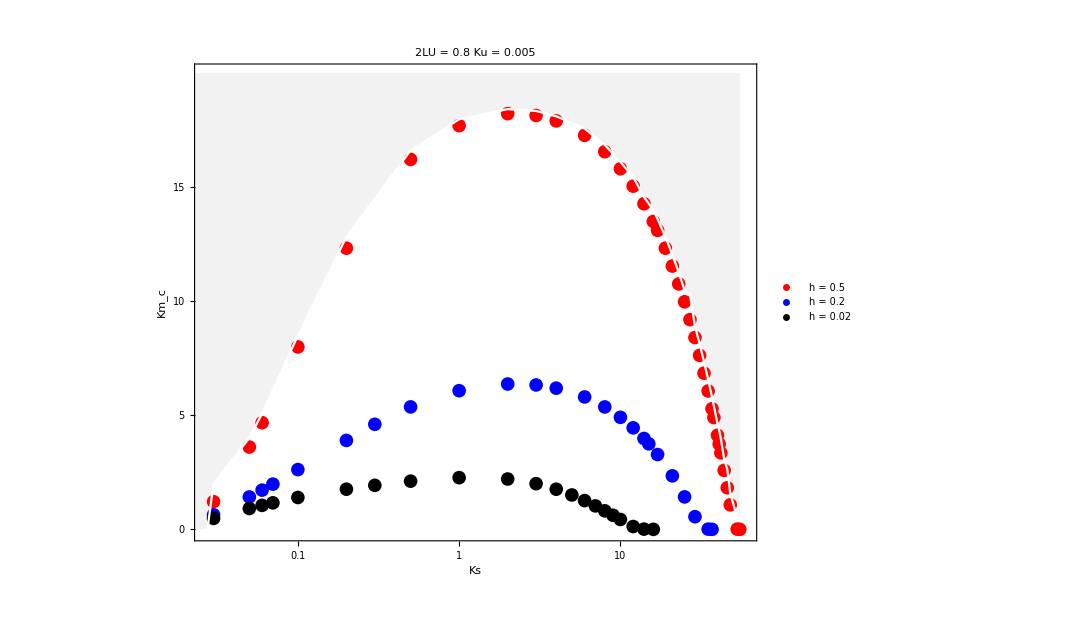

```mathematica
ma12=Show[ListLogLinearPlot[{Transpose[{{0.01,0.03,0.05,0.06,0.1,0.2,0.5,1.0,2.0,3.0,4.0,6.0,8.0,10.0,12.0,14.0,16.0,17.0,19.0,21.0,23.0,25.0,27.0,29.0,31.0,33.0,35.0,37.0,38.0,40.0,41.0,42.0,44.0,46.0,48.0,53.0,55.0},{0,1.213,3.608,4.675,7.997,12.326,16.218,17.701,18.225,18.144,17.907,17.273,16.558,15.8102,15.047,14.275,13.498,13.108,12.327,11.544,10.7604,9.977,9.194,8.41,7.628,6.847,6.067,5.289,4.9,4.125,3.739,3.354,2.586,1.824,1.075,0.01,0}}],Transpose[{{0.01,0.03,0.05,0.06,0.07,0.1,0.2,0.3,0.5,1.0,2.0,3.0,4.0,6.0,8.0,10.0,12.0,14.0,15.0,17.0,21.0,25.0,29,35.0,37.0},{0,0.639,1.4202,1.72,1.983,2.62,3.899, 4.606,5.368,6.079,6.372, 6.33,6.19,5.804,5.367,4.912,4.4503,3.984,3.75,3.2804,2.345,1.423,0.555,0.0098,0}}],Transpose[{{0.01,0.03,0.05,0.06,0.07,0.1,0.2,0.3,0.5,1.0,2.0,3.0,4.0,5.0,6.0,7.0,8.0,9.0,10.0,12.0,14.0,16.0},{0,0.4802,0.914,1.052,1.1619,1.397,1.7603,1.929,2.113,2.267,2.207,2.003,1.759,1.507,1.2606,1.028,0.813,0.618,0.433,0.124,0.0103, 0}}]},PlotRange->{{0.0267,60},{-0.1,20}},PlotMarkers->{{"●",14}},PlotLegends->Placed[{Style["h = 0.5",24,FontFamily->"Times"],Style["h = 0.2",24,FontFamily->"Times"],Style["h = 0.02",24,FontFamily->"Times"]},{Right,Top}],PlotLabel->Style["2LU = 0.8       Ku = 0.005",28],PlotStyle->{Red,Blue,Black},Frame->True,FrameTicks->{{{0,5,10,15},None},{{0.05,0.10,0.5,1,5,20,40},None}},FrameTicksStyle->Directive[Times,24],FrameLabel->{Row[{Style["",20,Black,Bold],Style["   Ks",28]},""],Row[{Style["   ",20,Black,Bold],Style["Km_c",30,Black,Bold]},""]},AspectRatio->0.8,ImageSize->800],ListLogLinearPlot[Transpose[{{0,0.01,0.02,0.025,0.0275,0.03,0.05,0.06,0.1,0.2,0.5,1.0,2.0,3.0,4.0,6.0,8.0,10.0,12.0,14.0,16.0,17.0,19.0,21.0,23.0,25.0,27.0,29.0,31.0,33.0,35.0,37.0,38.0,40.0,41.0,42.0,44.0,46.0,48.0,53.0,55.0},{0,0,0,0,0,2.013,4.008,5.075,8.497,12.826,16.618,17.98,18.425,18.344,18.107,17.573,16.858,16.1102,15.447,14.575,13.998,13.608,12.827,12.044,11.2604,10.477,10.294,8.91,8.128,7.347,6.567,5.789,5.4,4.625,4.339,3.954,3.086,2.624,1.575,0.51,0.5}}],Joined->True,PlotRange->{{0.03,60},{0.01,20}},PlotStyle->White,Filling->{1->{Top,Directive[Gray,Opacity[0.1]]}},AspectRatio->0.8,ImageSize->800,Frame->True]]
```

```mathematica
Export["ma12.pdf",ma12,"PDF","AllowRasterization"->False];
```

### Critical thresholds for metapopulation persistence Vs 2LU given Ku = 0.005

#### Ks = 1

h = 0.5

```mathematica
ll1ah05N1p0KmaA=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.5,0.05,80]⟦1⟧⟦1⟧},{Km,{0.05,0.06,0.066,0.067,0.07,0.08,0.09,0.1,0.5}}]
```

{{0.05,0},{0.06,0},{0.066,0},{0.067,0.573506},{0.07,0.619515},{0.08,0.684885},{0.09,0.719236},{0.1,0.742222},{0.5,0.864805}}

```mathematica
ll1ah05N1p0KmbA=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.5,0.1,80]⟦1⟧⟦1⟧},{Km,{0.05,0.06,0.07,0.08,0.1,0.2,0.201,0.202,0.3,0.5}}]
```

{{0.05,0},{0.06,0},{0.07,0},{0.08,0},{0.1,0},{0.2,0},{0.201,0},{0.202,0.474992},{0.3,0.64597},{0.5,0.71058}}

```mathematica
ll1ah05N1p0KmcA=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.5,0.15,80]⟦1⟧⟦1⟧},{Km,{0.05,0.06,0.1,0.2,0.3,0.4,0.43,0.44,0.441,0.442,0.443,0.45,0.5,0.6,0.8}}]
```

{{0.05,0},{0.06,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.43,0},{0.44,0},{0.441,0},{0.442,0.396302},{0.443,0.402826},{0.45,0.42654},{0.5,0.4887},{0.6,0.540136},{0.8,0.586933}}

```mathematica
ll1ah05N1p0KmdA=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0.05,0.06,0.1,0.2,0.3,0.4,0.5,0.7,0.8,0.86,0.869,0.87,0.9,1,2}}]
```

{{0.05,0},{0.06,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{0.7,0},{0.8,0},{0.86,0},{0.869,0},{0.87,0.324091},{0.9,0.369297},{1,0.417536},{2,0.524896}}

```mathematica
ll1ah05N1p0KmeA=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.5,0.25,80]⟦1⟧⟦1⟧},{Km,{0.05,0.06,0.1,0.2,0.3,0.4,0.5,1,1.3,1.6,1.66,1.663,1.664,1.665,1.666,1.67,1.7,1.8,2}}]
```

{{0.05,0},{0.06,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{1,0},{1.3,0},{1.6,0},{1.66,0},{1.663,0},{1.664,0},{1.665,0.263122},{1.666,0.266779},{1.67,0.273632},{1.7,0.294495},{1.8,0.325141},{2,0.356909}}

```mathematica
ll1ah05N1p0KmfA=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.5,0.3,80]⟦1⟧⟦1⟧},{Km,{0.05,0.06,0.1,0.2,0.3,0.4,0.5,1,2,3,3.2,3.25,3.258,3.259,3.26,3.28,3.3,3.4,3.5}}]
```

{{0.05,0},{0.06,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{1,0},{2,0},{3,0},{3.2,0},{3.25,0},{3.258,0},{3.259,0.209392},{3.26,0.210856},{3.28,0.22208},{3.3,0.228109},{3.4,0.245913},{3.5,0.257288}}

```mathematica
ll1ah05N1p0KmgA=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.5,0.35,80]⟦1⟧⟦1⟧},{Km,{0.05,0.06,0.1,0.2,0.3,0.4,0.5,1,3,5,6,6.9,6.91,6.915,6.916,6.92,7,8}}]
```

{{0.05,0},{0.06,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{1,0},{3,0},{5,0},{6,0},{6.9,0},{6.91,0},{6.915,0},{6.916,0.155554},{6.92,0.158225},{7,0.170916},{8,0.209633}}

```mathematica
ll1ah05N1p0KmhA=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0.05,0.06,0.1,0.2,0.3,0.4,0.5,1,3,7,8,10,17,17.7,17.701,17.703,17.713,17.74,17.8,18,19,20}}]
```

{{0.05,0},{0.06,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{1,0},{3,0},{7,0},{8,0},{10,0},{17,0},{17.7,0},{17.701,0.104401},{17.703,0.105285},{17.713,0.106854},{17.74,0.108996},{17.8,0.111842},{18,0.117426},{19,0.131067},{20,0.139054}}

```mathematica
ll1ah05N1p0KmiA=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.5,0.45,80]⟦1⟧⟦1⟧},{Km,{70,73,73.7,73.8,73.9,74,75,80,90}}]
```

{{70,0},{73,0},{73.7,0},{73.8,0.05598},{73.9,0.0569866},{74,0.0576882},{75,0.0615285},{80,0.0696959},{90,0.0776021}}

```mathematica
ll1ah05N1p0KmjA=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.5,0.5,80]⟦1⟧⟦1⟧},{Km,{0.05,19,20,25,30,80,100,150,250,350,500}}]
```

{{0.05,0},{19,0},{20,0},{25,0},{30,0},{80,0},{100,0},{150,0},{250,0},{350,0},{500,0}}

h = 0.02

```mathematica
ll1ah002N1p0Kma1AAKs1=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.02,0.05,80]⟦1⟧⟦1⟧},{Km,{0,0.0001,0.001,0.01,0.05,0.057,0.058,0.06,0.1,0.2,0.3,0.5,5}}]
```

{{0,0},{0.0001,0},{0.001,0},{0.01,0},{0.05,0},{0.057,0},{0.058,0.609405},{0.06,0.646844},{0.1,0.804513},{0.2,0.871981},{0.3,0.89284},{0.5,0.910413},{5,0.93862}}

```mathematica
ll1ah002N1p0KmaAAKs1=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.02,0.1,80]⟦1⟧⟦1⟧},{Km,{0.007,0.008,0.01,0.05,0.06,0.1,0.15,0.151,0.152,0.153,0.16,0.2,0.3}}]
```

{{0.007,0},{0.008,0},{0.01,0},{0.05,0},{0.06,0},{0.1,0},{0.15,0},{0.151,0},{0.152,0.528614},{0.153,0.546654},{0.16,0.59709},{0.2,0.690433},{0.3,0.763547}}

```mathematica
ll1ah002N1p0KmbAAKs1=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.02,0.15,80]⟦1⟧⟦1⟧},{Km,{0.02,0.03,0.1,0.2,0.28,0.283,0.284,0.29,0.3,0.5}}]
```

{{0.02,0},{0.03,0},{0.1,0},{0.2,0},{0.28,0},{0.283,0},{0.284,0.471744},{0.29,0.517151},{0.3,0.547871},{0.5,0.694187}}

```mathematica
ll1ah002N1p0KmcAAKs1=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0.05,0.06,0.1,0.2,0.3,0.4,0.45,0.46,0.464,0.465,0.47,0.5}}]
```

{{0.05,0},{0.06,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.45,0},{0.46,0},{0.464,0},{0.465,0.435054},{0.47,0.460512},{0.5,0.514114}}

```mathematica
ll1ah002N1p0KmdAAKs1=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.02,0.25,80]⟦1⟧⟦1⟧},{Km,{0.05,0.06,0.1,0.2,0.4,0.5,0.7,0.708,0.709,0.71,0.8,1,3,5}}]
```

{{0.05,0},{0.06,0},{0.1,0},{0.2,0},{0.4,0},{0.5,0},{0.7,0},{0.708,0},{0.709,0.397169},{0.71,0.402375},{0.8,0.495061},{1,0.559452},{3,0.670088},{5,0.68703}}

```mathematica
ll1ah002N1p0KmeAAKs1=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.02,0.3,80]⟦1⟧⟦1⟧},{Km,{0.05,0.06,0.1,0.2,1,1.03,1.036,1.037,1.04,1.1,1.2,2,3,5,7}}]
```

{{0.05,0},{0.06,0},{0.1,0},{0.2,0},{1,0},{1.03,0},{1.036,0},{1.037,0.358894},{1.04,0.369165},{1.1,0.424451},{1.2,0.463404},{2,0.562224},{3,0.597435},{5,0.62139},{7,0.630277}}

```mathematica
ll1ah002N1p0KmfAAKs1=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.02,0.35,80]⟦1⟧⟦1⟧},{Km,{0.05,0.06,0.1,0.2,1,1.5,1.507,1.508,1.51,1.52,1.6,1.7,2,3,5}}]
```

{{0.05,0},{0.06,0},{0.1,0},{0.2,0},{1,0},{1.5,0},{1.507,0},{1.508,0.356305},{1.51,0.357674},{1.52,0.363853},{1.6,0.395837},{1.7,0.420189},{2,0.462572},{3,0.519208},{5,0.553588}}

```mathematica
ll1ah002N1p0KmgAAKs1=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0.05,0.06,0.1,0.2,0.3,0.4,0.5,1,1.7,1.8,2,2.2,2.26,2.266,2.267,2.27,2.3,3,4}}]
```

{{0.05,0},{0.06,0},{0.1,0},{0.2,0},{0.3,0},{0.4,0},{0.5,0},{1,0},{1.7,0},{1.8,0},{2,0},{2.2,0},{2.26,0},{2.266,0},{2.267,0.359326},{2.27,0.359896},{2.3,0.365288},{3,0.429522},{4,0.464808}}

```mathematica
ll1ah002N1p0KmhAAKs1=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.02,0.45,80]⟦1⟧⟦1⟧},{Km,{0.05,0.06,0.1,1,2,3,3.5,3.55,3.559,3.56,3.57,3.6,3.7,4}}]
```

{{0.05,0},{0.06,0},{0.1,0},{1,0},{2,0},{3,0},{3.5,0},{3.55,0},{3.559,0},{3.56,0.353034},{3.57,0.353681},{3.6,0.355575},{3.7,0.361417},{4,0.375645}}

```mathematica
ll1ah05N1p0KmiAAKs1=Table[{Km,fxptHardmeta[1,0,0.005,1,Km,0.02,0.5,80]⟦1⟧⟦1⟧},{Km,{0.05,0.06,0.1,1,4,5,5.3,5.7,5.78,5.789,5.79,5.8,5.9,6,8,10,15,20,30,50}}]
```

{{0.05,0},{0.06,0},{0.1,0},{1,0},{4,0},{5,0},{5.3,0},{5.7,0},{5.78,0},{5.789,0},{5.79,0.332989},{5.8,0.333224},{5.9,0.335498},{6,0.337643},{8,0.364515},{10,0.377418},{15,0.391755},{20,0.397811},{30,0.403151},{50,0.406907}}

#### Ks = 5

h = 0.5

```mathematica
ll1ah05N1p0KmaAks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.5,0.05,80]⟦1⟧⟦1⟧},{Km,{0,0.05,0.06,0.066,0.067,0.07,0.08,0.09,0.1,0.5}}]
```

{{0,0.87665},{0.05,0.884875},{0.06,0.8851},{0.066,0.885218},{0.067,0.885237},{0.07,0.885292},{0.08,0.885463},{0.09,0.885618},{0.1,0.885762},{0.5,0.88902}}

```mathematica
ll1ah05N1p0KmbAks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.5,0.1,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.001,0.002,0.0022,0.0023,0.003,0.01,0.05,0.06}}]
```

{{0.0001,0},{0.001,0},{0.002,0},{0.0022,0},{0.0023,0.675356},{0.003,0.701698},{0.01,0.741587},{0.05,0.760058},{0.06,0.761196}}

```mathematica
ll1ah05N1p0KmcAks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.5,0.15,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.01,0.03,0.036,0.037,0.0376,0.0377,0.038,0.04,0.06}}]
```

{{0.0001,0},{0.01,0},{0.03,0},{0.036,0},{0.037,0},{0.0376,0},{0.0377,0.540186},{0.038,0.546852},{0.04,0.563784},{0.06,0.602097}}

```mathematica
ll1ah05N1p0KmdAks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.5,0.2,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.01,0.05,0.06,0.1,0.2,0.21,0.212,0.213,0.22,0.3,0.5}}]
```

{{0.0001,0},{0.01,0},{0.05,0},{0.06,0},{0.1,0},{0.2,0},{0.21,0},{0.212,0},{0.213,0.40932},{0.22,0.429654},{0.3,0.476138},{0.5,0.507552}}

```mathematica
ll1ah05N1p0Kmeks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.5,0.25,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.01,0.03,0.2,0.5,0.7,0.78,0.786,0.787,0.79,0.8,1}}]
```

{{0.0001,0},{0.01,0},{0.03,0},{0.2,0},{0.5,0},{0.7,0},{0.78,0},{0.786,0},{0.787,0.301929},{0.79,0.308278},{0.8,0.318295},{1,0.369558}}

```mathematica
ll1ah05N1p0Kmfks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.5,0.3,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.01,0.03,0.04,0.5,0.6,0.8,1,2,2.1,2.2,2.23,2.235,2.236,3,5}}]
```

{{0.0001,0},{0.01,0},{0.03,0},{0.04,0},{0.5,0},{0.6,0},{0.8,0},{1,0},{2,0},{2.1,0},{2.2,0},{2.23,0},{2.235,0},{2.236,0.221452},{3,0.297148},{5,0.338734}}

```mathematica
ll1ah05N1p0Kmgks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.5,0.35,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.01,0.03,0.04,0.5,0.6,0.8,1,2,3,5,5.8,5.9,5.93,5.931,5.932,5.933,5.94,5.97,6,7}}]
```

{{0.0001,0},{0.01,0},{0.03,0},{0.04,0},{0.5,0},{0.6,0},{0.8,0},{1,0},{2,0},{3,0},{5,0},{5.8,0},{5.9,0},{5.93,0},{5.931,0},{5.932,0},{5.933,0.156956},{5.94,0.160735},{5.97,0.166587},{6,0.170148},{7,0.207866}}

```mathematica
ll1ah05N1p0Kmhks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.5,0.4,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.01,0.03,0.04,0.5,0.6,0.8,1,2,3,5,6,7,10,15,17,17.5,17.6,17.605,17.606,17.607,17.61,17.62}}]
```

{{0.0001,0},{0.01,0},{0.03,0},{0.04,0},{0.5,0},{0.6,0},{0.8,0},{1,0},{2,0},{3,0},{5,0},{6,0},{7,0},{10,0},{15,0},{17,0},{17.5,0},{17.6,0},{17.605,0},{17.606,0.102114},{17.607,0.10261},{17.61,0.103306},{17.62,0.104548}}

```mathematica
ll1ah05N1p0Kmhls10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.5,0.45,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.01,0.03,20,30,50,80,83,84,84.2,84.21,84.24,84.243,84.247,84.25,84.27,84.3,84.5,85,87,90,100}}]
```

{{0.0001,0},{0.01,0},{0.03,0},{20,0},{30,0},{50,0},{80,0},{83,0},{84,0},{84.2,0},{84.21,0},{84.24,0},{84.243,0.0510406},{84.247,0.051319},{84.25,0.0514287},{84.27,0.051867},{84.3,0.0522731},{84.5,0.053736},{85,0.0557058},{87,0.0599082},{90,0.063674},{100,0.0709295}}

```mathematica
ll1ah05N1p0Kmhms10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.5,0.5,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.01,0.03,0.04,100,200}}]
```

{{0.0001,0},{0.01,0},{0.03,0},{0.04,0},{100,0},{200,0}}

h = 0.02

```mathematica
ll1ah002N1p0KmaAks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.02,0.05,80]⟦1⟧⟦1⟧},{Km,{0,0.0001,0.001,0.05,0.06,0.066,0.067,0.07,0.08,0.09,0.1,0.5}}]
```

{{0,0.915117},{0.0001,0.915232},{0.001,0.916091},{0.05,0.921099},{0.06,0.921351},{0.066,0.92149},{0.067,0.921512},{0.07,0.921578},{0.08,0.921789},{0.09,0.921987},{0.1,0.922174},{0.5,0.926802}}

```mathematica
ll1ah002N1p0KmbAks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.02,0.1,80]⟦1⟧⟦1⟧},{Km,{0,0.0001,0.01,0.05,0.06}}]
```

{{0,0.801841},{0.0001,0.802894},{0.01,0.828506},{0.05,0.837088},{0.06,0.837874}}

```mathematica
ll1ah002N1p0KmcAks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.02,0.15,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.005,0.008,0.00802,0.00803,0.00804,0.0081,0.0084,0.009,0.01,0.05,0.06}}]
```

{{0.0001,0},{0.005,0},{0.008,0},{0.00802,0},{0.00803,0},{0.00804,0.650207},{0.0081,0.658219},{0.0084,0.670424},{0.009,0.681968},{0.01,0.692916},{0.05,0.742424},{0.06,0.744796}}

```mathematica
ll1ah002N1p0KmdAks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.02,0.2,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.01,0.03,0.04,0.041,0.042,0.0423,0.0424,0.0425,0.043,0.047,0.05,0.06}}]
```

{{0.0001,0},{0.01,0},{0.03,0},{0.04,0},{0.041,0},{0.042,0},{0.0423,0},{0.0424,0.558598},{0.0425,0.562532},{0.043,0.571037},{0.047,0.593911},{0.05,0.602434},{0.06,0.618774}}

```mathematica
ll1ah002N1p0KmeAks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.02,0.25,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.01,0.03,0.04,0.05,0.06,0.1,0.13,0.14,0.147,0.148,0.15,0.2,0.3}}]
```

{{0.0001,0},{0.01,0},{0.03,0},{0.04,0},{0.05,0},{0.06,0},{0.1,0},{0.13,0},{0.14,0},{0.147,0},{0.148,0.476341},{0.15,0.485295},{0.2,0.536815},{0.3,0.567445}}

```mathematica
ll1ah002N1p0KmfAks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.02,0.3,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.01,0.03,0.04,0.1,0.3,0.37,0.379,0.38,0.39,0.4,0.41,0.5,1}}]
```

{{0.0001,0},{0.01,0},{0.03,0},{0.04,0},{0.1,0},{0.3,0},{0.37,0},{0.379,0},{0.38,0.398164},{0.39,0.418257},{0.4,0.428454},{0.41,0.43603},{0.5,0.472505},{1,0.535488}}

```mathematica
ll1ah002N1p0KmgAks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.02,0.35,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.01,0.03,0.04,0.1,0.3,0.37,0.379,0.38,0.39,0.4,0.41,0.5,0.7,0.78,0.7801,0.7802,0.781,0.79,0.8,1}}]
```

{{0.0001,0},{0.01,0},{0.03,0},{0.04,0},{0.1,0},{0.3,0},{0.37,0},{0.379,0},{0.38,0},{0.39,0},{0.4,0},{0.41,0},{0.5,0},{0.7,0},{0.78,0},{0.7801,0},{0.7802,0.333052},{0.781,0.337966},{0.79,0.352838},{0.8,0.361369},{1,0.419688}}

```mathematica
ll1ah002N1p0KmhAks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.02,0.4,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.01,0.03,0.04,0.1,0.3,0.5,0.7,1,1.5,1.506,1.507,1.51,1.52,1.53,1.6,1.8}}]
```

{{0.0001,0},{0.01,0},{0.03,0},{0.04,0},{0.1,0},{0.3,0},{0.5,0},{0.7,0},{1,0},{1.5,0},{1.506,0},{1.507,0.335249},{1.51,0.335926},{1.52,0.338104},{1.53,0.34017},{1.6,0.352351},{1.8,0.375759}}

```mathematica
ll1ah002N1p0KmiAks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.02,0.45,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.01,0.03,0.04,0.1,0.3,0.5,0.7,1,1.5,2,1.8,2,3,3.3,3.39,3.3907,3.391,3.392,3.4,3.5,4,5}}]
```

{{0.0001,0},{0.01,0},{0.03,0},{0.04,0},{0.1,0},{0.3,0},{0.5,0},{0.7,0},{1,0},{1.5,0},{2,0},{1.8,0},{2,0},{3,0},{3.3,0},{3.39,0},{3.3907,0},{3.391,0},{3.392,0.347604},{3.4,0.347877},{3.5,0.351119},{4,0.36377},{5,0.37867}}

```mathematica
ll1ah002N1p0KmjAks10=Table[{Km,fxptHardmeta[1,0,0.005,5,Km,0.02,0.5,80]⟦1⟧⟦1⟧},{Km,{0.0001,0.01,0.03,0.04,0.1,0.3,0.5,0.7,1,1.5,2,1.8,2,3,4,5,7,10,10.03,10.04,10.046,10.047,10.05,10.1,10.3,11}}]
```

{{0.0001,0},{0.01,0},{0.03,0},{0.04,0},{0.1,0},{0.3,0},{0.5,0},{0.7,0},{1,0},{1.5,0},{2,0},{1.8,0},{2,0},{3,0},{4,0},{5,0},{7,0},{10,0},{10.03,0},{10.04,0},{10.046,0},{10.047,0.326297},{10.05,0.326301},{10.1,0.326372},{10.3,0.326636},{11,0.327333}}

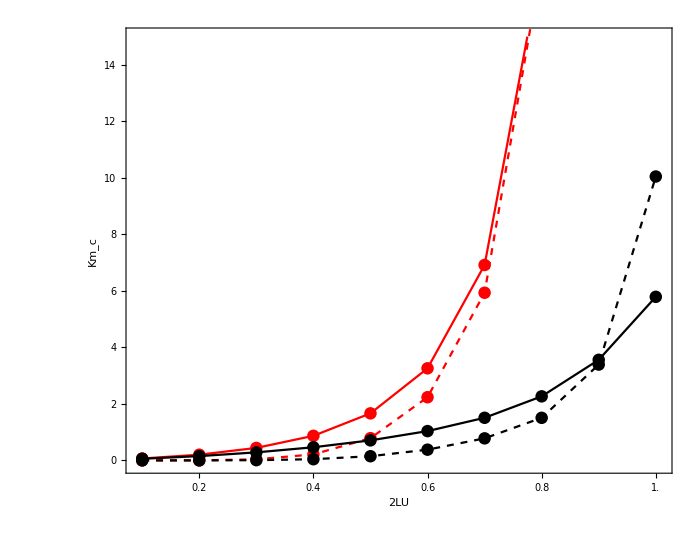

```mathematica
a01=Show[ListPlot[Transpose[{2{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5},{0.067,0.202,0.442,0.87,1.665,3.259,6.916,17.701,73.8,600}}],PlotRange->{{0.09,1.01},{-0.15,15}},PlotLegends->Placed[{Style["h = 0.5",26,FontFamily->"Times"]},{Left,Top}],Joined->True,Mesh->All,Frame->True,PlotStyle->Red,FrameTicks->{{{0,2,4,6,8,10,12,14},None},{{0,0.2,0.4,0.6,0.8,1.0},None}},FrameTicksStyle->Directive[Times,30],FrameLabel->{Row[{Style["",30,Black,Bold],Style["   2LU",30,FontFamily->"Times"]},""],Row[{Style["Km_c",30,Black,Bold,FontFamily->"Times"],Style["  ",30]},""]},AspectRatio->0.8,ImageSize->700],ListPlot[Transpose[{2{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5},{0,0.0023,0.0377,0.213,0.787,2.236,5.933,17.606,84.243,300}}],Joined->True,Mesh->All,Frame->True, FrameTicks->{{{0,2,4,6,8,10,12,14},None},{{0,0.2,0.4,0.6,0.8,1.0},None}},PlotStyle->Directive[Red,Dashed],ImageSize->700],ListPlot[Transpose[{2{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5},{0.058,0.152,0.284,0.465,0.709,1.037,1.508,2.267,3.56,5.789}}],Joined->True,Mesh->All,PlotLegends->Placed[{Style["h = 0.02",26,FontFamily->"Times"]},{Left,Top}],PlotStyle->Black,ImageSize->700],ListPlot[Transpose[{2{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5},{0,0,0.00804,0.0424,0.148,0.38,0.7802,1.507,3.392,10.047}}],Joined->True,Mesh->All,PlotStyle->Directive[Black,Dashed],ImageSize->700],ImageSize->700]
```

```mathematica
Export["a01.pdf",a01,"PDF","AllowRasterization"->False];
```

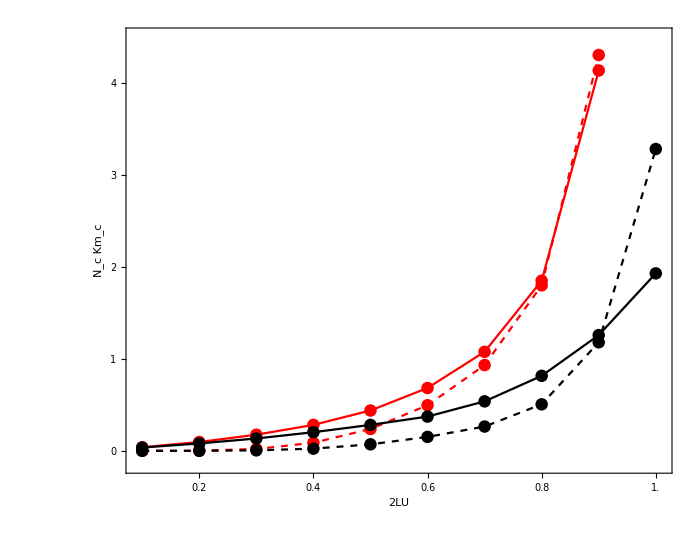

```mathematica
a04=Show[ListPlot[Transpose[{2{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45},({0.573506,0.4749916,0.396302,0.324091,0.263122,0.209392,0.155554,0.104401,0.05598}*{0.067,0.202,0.442,0.87,1.665,3.259,6.916,17.701,73.8})}],PlotRange->{{0.09,1.01},{-0.15,4.5}},PlotLegends->Placed[{Style["h = 0.5",26,FontFamily->"Times"]},{Left,Top}],Joined->True,Mesh->All,Frame->True,PlotStyle->Red,FrameTicks->{{{0,1,2,3,4},None},{{0,0.2,0.4,0.6,0.8,1.0},None}},FrameTicksStyle->Directive[Times,30],FrameLabel->{Row[{Style["",30,Black,Bold],Style["   2LU",30,FontFamily->"Times"]},""],Row[{Style["N_c Km_c",30,Black,Bold,FontFamily->"Times"],Style["  ",30]},""]},AspectRatio->0.8,ImageSize->700],ListPlot[Transpose[{2{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45},({0.87665,0.675356,0.540186,0.40932,0.301929,0.221452,0.156956,0.102114,0.0510406}*{0,0.0023,0.0377,0.213,0.787,2.236,5.933,17.606,84.243})}],Joined->True,Mesh->All,Frame->True, FrameTicks->{{{0,2,4,6,8,10,12,14},None},{{0,0.2,0.4,0.6,0.8,1.0},None}},PlotStyle->Directive[Red,Dashed],ImageSize->700],ListPlot[Transpose[{2{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5},({0.609405,0.528614,0.471744,0.435054,0.397169,0.358894,0.356305,0.359326,0.353034,0.332989}*{0.058,0.152,0.284,0.465,0.709,1.037,1.508,2.267,3.56,5.789})}],Joined->True,Mesh->All,PlotLegends->Placed[{Style["h = 0.02",26,FontFamily->"Times"]},{Left,Top}],PlotStyle->Black,ImageSize->700],ListPlot[Transpose[{2{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5},({0.915232,0.802894,0.650207,0.558598,0.476341,0.398164,0.337966,0.335249,0.347604,0.326297}*{0,0,0.00804,0.0424,0.148,0.38,0.7802,1.507,3.392,10.047})}],Joined->True,Mesh->All,PlotStyle->Directive[Black,Dashed],ImageSize->700],ImageSize->700]
```

```mathematica
Export["a04.pdf",a04,"PDF","AllowRasterization"->False];
```

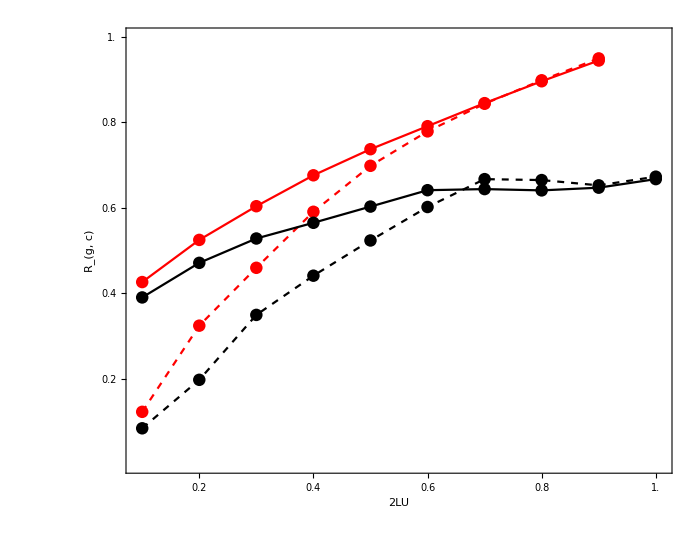

```mathematica
a03=Show[ListPlot[Transpose[{2{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45},1-{0.573506,0.4749916,0.396302,0.324091,0.263122,0.209392,0.155554,0.104401,0.05598}}],PlotRange->{{0.09,1.01},{0.,1}},PlotLegends->Placed[{Style["h = 0.5",26,FontFamily->"Times"]},{Left,Top}],Joined->True,Mesh->All,Frame->True,PlotStyle->Red,FrameTicks->{{{0.2,0.4,0.6,0.8,1.0},None},{{0.2,0.4,0.6,0.8,1.0},None}},FrameTicksStyle->Directive[Times,30],FrameLabel->{Row[{Style["",30,Black,Bold],Style["   2LU",30,FontFamily->"Times"]},""],Row[{Style["R_(g,  c)",30,Black,Bold,FontFamily->"Times"],Style["  ",30]},""]},AspectRatio->0.8,ImageSize->700],ListPlot[Transpose[{2{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45},1-{0.87665,0.675356,0.540186,0.40932,0.301929,0.221452,0.156956,0.102114,0.0510406}}],Joined->True,Mesh->All,PlotStyle->Directive[Red,Dashed],ImageSize->700],ListPlot[Transpose[{2{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5},1-{0.609405,0.528614,0.471744,0.435054,0.397169,0.358894,0.356305,0.359326,0.353034,0.332989}}],Joined->True,Mesh->All,PlotLegends->Placed[{Style["h = 0.02",26,FontFamily->"Times"]},{Left,Top}],PlotStyle->Black,ImageSize->700],ListPlot[Transpose[{2{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5},1-{0.915117,0.801841,0.650207,0.558598,0.476341,0.398164,0.333052,0.335249,0.347604,0.327333}}],Joined->True,Mesh->All,PlotStyle->Directive[Black,Dashed],ImageSize->700],ImageSize->700]
```

```mathematica
Export["a03.pdf",a03,"PDF","AllowRasterization"->False];
```

### Looking at the distribution of fitness effects

a = 0.2

```mathematica
LENmLU03h002Ns1Ku0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,1,10,Km,0.5,0.02,0.3,80,0.2]⟦1⟧},{Km,{0.02,0.05,0.1,0.2,0.22,0.24,0.26,0.28,0.3,0.31,0.32,0.34,0.36,0.38,0.4,0.44,0.45,0.46,0.48,0.5,0.6,0.8,1.0,1.1,1.2,1.4,1.6,1.8,2.0,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.128664,0.0044095,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.123673,0.0789936,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.0815452,0.0360643,Indeterminate,Indeterminate,Indeterminate}},{0.2,{0,0.0441538,0.00432673,Indeterminate,Indeterminate,Indeterminate}},{0.22,{0,0.0348998,0.00304348,Indeterminate,Indeterminate,Indeterminate}},{0.24,{0,0.0373692,0.00330807,Indeterminate,Indeterminate,Indeterminate}},{0.26,{0,0.0398257,0.0041671,Indeterminate,Indeterminate,Indeterminate}},{0.28,{0,0.041462,0.00571275,Indeterminate,Indeterminate,Indeterminate}},{0.3,{0,0.0405142,0.00573408,Indeterminate,Indeterminate,Indeterminate}},{0.31,{0,0.0332955,0.00312579,Indeterminate,Indeterminate,Indeterminate}},{0.32,{0,0.0366423,0.0039225,Indeterminate,Indeterminate,Indeterminate}},{0.34,{0,0.0321131,0.00308308,Indeterminate,Indeterminate,Indeterminate}},{0.36,{0,0.032696,0.00320542,Indeterminate,Indeterminate,Indeterminate}},{0.38,{0,0.0383011,0.00659286,Indeterminate,Indeterminate,Indeterminate}},{0.4,{0,0.0312056,0.00311062,Indeterminate,Indeterminate,Indeterminate}},{0.44,{0,0.0296925,0.00301923,Indeterminate,Indeterminate,Indeterminate}},{0.45,{0,0.0299457,0.00305448,Indeterminate,Indeterminate,Indeterminate}},{0.46,{0.347892,0.0214083,0.00318533,0.2569,0.395208,0.652108}},{0.48,{0.372902,0.0201045,0.00325512,0.241254,0.385844,0.627098}},{0.5,{0.387466,0.0193031,0.00330022,0.231638,0.380897,0.612534}},{0.6,{0.426928,0.0170384,0.00344762,0.20446,0.368611,0.573072}},{0.8,{0.462818,0.0149566,0.00364415,0.179479,0.357703,0.537182}},{1.,{0.48208,0.0138779,0.00380419,0.166535,0.351385,0.51792}},{1.1,{0.488977,0.0135044,0.00387838,0.162053,0.34897,0.511023}},{1.2,{0.494738,0.0131988,0.00395013,0.158386,0.346876,0.505262}},{1.4,{0.503889,0.0127268,0.00408847,0.152722,0.343389,0.496111}},{1.6,{0.510882,0.0123777,0.00422188,0.148533,0.340585,0.489118}},{1.8,{0.516423,0.0121082,0.00435162,0.145298,0.338279,0.483577}},{2.,{0.520924,0.0118933,0.00447837,0.14272,0.336356,0.479076}},{3.,{0.53459,0.0112492,0.00507668,0.13499,0.330419,0.46541}},{4.,{0.540953,0.010925,0.0056237,0.1311,0.327947,0.459047}},{5,{0.544035,0.0107289,0.00612342,0.128747,0.327218,0.455965}},{9,{0.545029,0.0103751,0.00771819,0.124502,0.330469,0.454971}},{10,{0.544281,0.0103302,0.00803426,0.123962,0.331757,0.455719}},{11,{0.543415,0.0102932,0.00832404,0.123518,0.333067,0.456585}},{12,{0.542487,0.0102622,0.00859036,0.123146,0.334368,0.457513}},{13,{0.541531,0.0102358,0.00883574,0.12283,0.335639,0.458469}},{14,{0.540573,0.0102131,0.0090624,0.122557,0.33687,0.459427}},{15,{0.539625,0.0101934,0.00927226,0.12232,0.338054,0.460375}},{20,{0.535285,0.0101235,0.0101229,0.121482,0.343233,0.464715}},{22,{0.533771,0.0101041,0.0103918,0.12125,0.344979,0.466229}},{24,{0.53238,0.0100879,0.0106302,0.121055,0.346564,0.46762}},{26,{0.531105,0.0100742,0.0108428,0.12089,0.348006,0.468895}},{28,{0.529933,0.0100623,0.0110335,0.120747,0.34932,0.470067}},{30,{0.528856,0.0100519,0.0112056,0.120623,0.350521,0.471144}}}

```mathematica
LENmLU03h002Ns1bKu0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,1,20,Km,0.5,0.02,0.3,80,0.2]⟦1⟧},{Km,{0.02,0.05,0.1,0.2,0.22,0.24,0.26,0.28,0.3,0.31,0.32,0.33,0.34,0.36,0.38,0.4,0.6,0.8,1.0,1.1,1.2,1.4,1.6,1.8,2.0,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.126955,0.0016793,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.111377,0.00826012,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.0623553,0.00157582,Indeterminate,Indeterminate,Indeterminate}},{0.2,{0,0.0631936,0.00901534,Indeterminate,Indeterminate,Indeterminate}},{0.22,{0,0.0495842,0.00160952,Indeterminate,Indeterminate,Indeterminate}},{0.24,{0,0.0490812,0.00165894,Indeterminate,Indeterminate,Indeterminate}},{0.26,{0,0.0531296,0.00309598,Indeterminate,Indeterminate,Indeterminate}},{0.28,{0,0.0491539,0.00200088,Indeterminate,Indeterminate,Indeterminate}},{0.3,{0,0.0515145,0.00374941,Indeterminate,Indeterminate,Indeterminate}},{0.31,{0,0.0511518,0.00393043,Indeterminate,Indeterminate,Indeterminate}},{0.32,{0,0.0433168,0.00154619,Indeterminate,Indeterminate,Indeterminate}},{0.33,{0.32921,0.0265274,0.00187167,0.318328,0.352462,0.67079}},{0.34,{0.355956,0.0246315,0.00192511,0.295578,0.348467,0.644044}},{0.36,{0.381728,0.0227565,0.00197734,0.273078,0.345194,0.618272}},{0.38,{0.398265,0.0215346,0.00201181,0.258415,0.34332,0.601735}},{0.4,{0.410704,0.020608,0.00203858,0.247296,0.342,0.589296}},{0.6,{0.467665,0.0163207,0.00218532,0.195849,0.336486,0.532335}},{0.8,{0.490072,0.0146406,0.00227339,0.175687,0.334241,0.509928}},{1.,{0.502823,0.0136974,0.00234601,0.164369,0.332808,0.497177}},{1.1,{0.507412,0.0133616,0.00237951,0.16034,0.332248,0.492588}},{1.2,{0.511237,0.0130836,0.00241181,0.157004,0.33176,0.488763}},{1.4,{0.517267,0.0126487,0.00247384,0.151784,0.330949,0.482733}},{1.6,{0.52182,0.0123228,0.00253347,0.147874,0.330307,0.47818}},{1.8,{0.525381,0.0120687,0.0025914,0.144824,0.329795,0.474619}},{2.,{0.528236,0.0118645,0.00264801,0.142375,0.329389,0.471764}},{3.,{0.536595,0.011244,0.00291717,0.134928,0.328476,0.463405}},{4.,{0.540124,0.0109266,0.00316836,0.13112,0.328756,0.459876}},{5,{0.541478,0.0107329,0.00340367,0.128795,0.329727,0.458522}},{9,{0.539143,0.0103803,0.00420115,0.124564,0.336293,0.460857}},{10,{0.53786,0.0103353,0.00436871,0.124024,0.338116,0.46214}},{11,{0.536499,0.0102982,0.00452532,0.123579,0.339922,0.463501}},{12,{0.535103,0.0102672,0.00467186,0.123206,0.341691,0.464897}},{13,{0.5337,0.0102407,0.00480913,0.122889,0.343411,0.4663}},{14,{0.53231,0.010218,0.00493789,0.122616,0.345074,0.46769}},{15,{0.530945,0.0101982,0.00505883,0.122378,0.346677,0.469055}},{20,{0.524689,0.010128,0.00556651,0.121536,0.353775,0.475311}},{22,{0.522482,0.0101086,0.00573309,0.121303,0.356215,0.477518}},{24,{0.520438,0.0100923,0.00588324,0.121107,0.358455,0.479562}},{26,{0.518545,0.0100784,0.00601923,0.120941,0.360514,0.481455}},{28,{0.516792,0.0100664,0.00614293,0.120797,0.362411,0.483208}},{30,{0.515167,0.010056,0.0062559,0.120672,0.364161,0.484833}}}

```mathematica
LENmLU03h002Ns1bbKu0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,1,30,Km,0.5,0.02,0.3,80,0.2]⟦1⟧},{Km,{0.02,0.05,0.1,0.2,0.22,0.24,0.26,0.28,0.3,0.31,0.32,0.34,0.36,0.38,0.4,0.6,0.8,1.0,1.1,1.2,1.4,1.6,1.8,2.0,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.127168,0.00126683,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.109778,0.00207159,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.0602118,0.00115055,Indeterminate,Indeterminate,Indeterminate}},{0.2,{0,0.0613555,0.00148739,Indeterminate,Indeterminate,Indeterminate}},{0.22,{0,0.0578274,0.00121222,Indeterminate,Indeterminate,Indeterminate}},{0.24,{0,0.0574635,0.00136885,Indeterminate,Indeterminate,Indeterminate}},{0.26,{0,0.0638154,0.0130246,Indeterminate,Indeterminate,Indeterminate}},{0.28,{0,0.0513003,0.00104672,Indeterminate,Indeterminate,Indeterminate}},{0.3,{0,0.0515456,0.00108927,Indeterminate,Indeterminate,Indeterminate}},{0.31,{0.344833,0.0265473,0.00145174,0.318567,0.336599,0.655167}},{0.32,{0.364707,0.0250124,0.00148329,0.300149,0.335144,0.635293}},{0.34,{0.388649,0.0231428,0.00152127,0.277714,0.333638,0.611351}},{0.36,{0.404766,0.0218738,0.00154716,0.262485,0.332748,0.595234}},{0.38,{0.417036,0.020903,0.00156726,0.250835,0.332128,0.582964}},{0.4,{0.426921,0.0201183,0.00158387,0.24142,0.33166,0.573079}},{0.6,{0.476098,0.0161886,0.00168002,0.194263,0.32964,0.523902}},{0.8,{0.496195,0.0145746,0.00173733,0.174896,0.328909,0.503805}},{1.,{0.507585,0.0136582,0.00178359,0.163898,0.328517,0.492415}},{1.1,{0.51165,0.0133303,0.00180468,0.159964,0.328386,0.48835}},{1.2,{0.515015,0.0130583,0.00182491,0.1567,0.328285,0.484985}},{1.4,{0.520265,0.0126318,0.0018635,0.151581,0.328153,0.479735}},{1.6,{0.524171,0.0123113,0.00190038,0.147735,0.328093,0.475829}},{1.8,{0.52718,0.0120609,0.00193607,0.144731,0.328089,0.47282}},{2.,{0.529555,0.0118594,0.00197086,0.142313,0.328132,0.470445}},{3.,{0.536213,0.011245,0.00213604,0.13494,0.328846,0.463787}},{4.,{0.538723,0.0109293,0.0022909,0.131152,0.330125,0.461277}},{5,{0.539421,0.0107361,0.00243725,0.128833,0.331745,0.460579}},{9,{0.535866,0.0103833,0.00294629,0.1246,0.339535,0.464134}},{10,{0.534406,0.0103381,0.00305619,0.124058,0.341536,0.465594}},{11,{0.532884,0.0103009,0.00315989,0.123611,0.343504,0.467116}},{12,{0.531337,0.0102698,0.0032578,0.123237,0.345426,0.468663}},{13,{0.529788,0.0102433,0.0033503,0.122919,0.347293,0.470212}},{14,{0.528254,0.0102204,0.00343776,0.122645,0.349101,0.471746}},{15,{0.526747,0.0102005,0.00352053,0.122407,0.350847,0.473253}},{20,{0.519792,0.0101301,0.00387459,0.121562,0.358647,0.480208}},{22,{0.517311,0.0101106,0.00399312,0.121328,0.361361,0.482689}},{24,{0.514998,0.0100943,0.00410098,0.121132,0.36387,0.485002}},{26,{0.512844,0.0100804,0.00419949,0.120964,0.366192,0.487156}},{28,{0.510836,0.0100684,0.0042898,0.12082,0.368343,0.489164}},{30,{0.508965,0.0100579,0.00437286,0.120695,0.37034,0.491035}}}

```mathematica
LENmLU03h002Ns1cKu0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,5,10,Km,0.5,0.02,0.3,80,0.2]⟦1⟧},{Km,{0.02,0.05,0.1,0.11,0.12,0.13,0.14,0.15,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.31,0.32,0.34,0.36,0.38,0.4,0.6,0.8,1.0,1.1,1.2,1.4,1.6,1.8,2.0,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.0204399,0.00437199,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.0204264,0.00597807,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.00682831,0.00315005,Indeterminate,Indeterminate,Indeterminate}},{0.11,{0,0.00855517,0.0034405,Indeterminate,Indeterminate,Indeterminate}},{0.12,{0.399885,0.00336183,0.00317549,0.20171,0.398405,0.600115}},{0.13,{0.420753,0.00315227,0.0032198,0.189136,0.39011,0.579247}},{0.14,{0.430375,0.00305221,0.00324327,0.183133,0.386493,0.569625}},{0.15,{0.437031,0.00298245,0.00326122,0.178947,0.384022,0.562969}},{0.18,{0.44985,0.00284884,0.00330172,0.17093,0.37922,0.55015}},{0.2,{0.455575,0.00279045,0.00332347,0.167427,0.376998,0.544425}},{0.22,{0.460139,0.00274494,0.00334308,0.164696,0.375165,0.539861}},{0.24,{0.463939,0.00270794,0.00336129,0.162477,0.373584,0.536061}},{0.26,{0.467202,0.00267695,0.00337853,0.160617,0.372181,0.532798}},{0.28,{0.470067,0.00265039,0.00339505,0.159023,0.370909,0.529933}},{0.3,{0.472626,0.00262723,0.00341104,0.157634,0.369741,0.527374}},{0.31,{0.473811,0.00261668,0.00341887,0.157001,0.369188,0.526189}},{0.32,{0.474942,0.00260674,0.00342661,0.156404,0.368654,0.525058}},{0.34,{0.477061,0.00258839,0.00344184,0.155304,0.367636,0.522939}},{0.36,{0.479016,0.00257182,0.00345679,0.154309,0.366675,0.520984}},{0.38,{0.480835,0.00255671,0.00347152,0.153402,0.365763,0.519165}},{0.4,{0.482535,0.00254284,0.00348605,0.15257,0.364894,0.517465}},{0.6,{0.495455,0.00244548,0.0036251,0.146729,0.357816,0.504545}},{0.8,{0.50432,0.00238585,0.00375833,0.143151,0.35253,0.49568}},{1.,{0.511065,0.00234351,0.00388862,0.140611,0.348324,0.488935}},{1.1,{0.513898,0.00232635,0.00395296,0.139581,0.34652,0.486102}},{1.2,{0.516451,0.00231115,0.00401683,0.138669,0.34488,0.483549}},{1.4,{0.520873,0.00228527,0.00414331,0.137116,0.342011,0.479127}},{1.6,{0.524568,0.00226392,0.00426815,0.135835,0.339597,0.475432}},{1.8,{0.527693,0.00224593,0.00439141,0.134756,0.337551,0.472307}},{2.,{0.530361,0.00223048,0.00451306,0.133829,0.33581,0.469639}},{3.,{0.539116,0.00217691,0.00509627,0.130614,0.33027,0.460884}},{4.,{0.543422,0.00214452,0.0056357,0.128671,0.327907,0.456578}},{5,{0.545435,0.00212254,0.00613081,0.127353,0.327212,0.454565}},{9,{0.544926,0.00207679,0.00771756,0.124607,0.330467,0.455074}},{10,{0.544034,0.00207026,0.00803273,0.124216,0.331751,0.455966}},{11,{0.543058,0.00206475,0.00832182,0.123885,0.333057,0.456942}},{12,{0.542045,0.00206003,0.00858762,0.123602,0.334354,0.457955}},{13,{0.541022,0.00205593,0.00883259,0.123356,0.335622,0.458978}},{14,{0.540008,0.00205235,0.00905893,0.123141,0.336851,0.459992}},{15,{0.539016,0.00204918,0.00926855,0.122951,0.338033,0.460984}},{20,{0.534539,0.00203759,0.0101186,0.122255,0.343206,0.465461}},{22,{0.532992,0.00203428,0.0103875,0.122057,0.344951,0.467008}},{24,{0.531577,0.00203147,0.0106259,0.121888,0.346535,0.468423}},{26,{0.530281,0.00202904,0.0108385,0.121743,0.347976,0.469719}},{28,{0.529094,0.00202694,0.0110293,0.121616,0.34929,0.470906}},{30,{0.528003,0.00202508,0.0112014,0.121505,0.350492,0.471997}}}

```mathematica
LENmLU03h002Ns1dKu0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,5,20,Km,0.5,0.02,0.3,80,0.2]⟦1⟧},{Km,{0.02,0.05,0.052,0.053,0.054,0.058,0.06,0.08,0.1,0.2,0.22,0.24,0.26,0.28,0.3,0.31,0.32,0.34,0.36,0.38,0.4,0.6,0.8,1.0,1.1,1.2,1.4,1.6,1.8,2.0,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.0254856,0.00163495,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.037405,0.00318199,Indeterminate,Indeterminate,Indeterminate}},{0.052,{0,0.0282413,0.00199913,Indeterminate,Indeterminate,Indeterminate}},{0.053,{0,0.035378,0.00301174,Indeterminate,Indeterminate,Indeterminate}},{0.054,{0.422703,0.00389002,0.00198482,0.233401,0.343896,0.577297}},{0.058,{0.445202,0.00354816,0.00202213,0.21289,0.341908,0.554798}},{0.06,{0.450729,0.00346368,0.00203139,0.207821,0.34145,0.549271}},{0.08,{0.475726,0.00308014,0.00207535,0.184809,0.339465,0.524274}},{0.1,{0.486047,0.00292192,0.00209615,0.175315,0.338638,0.513953}},{0.2,{0.504219,0.00264861,0.00214892,0.158917,0.336864,0.495781}},{0.22,{0.50598,0.00262304,0.00215666,0.157383,0.336638,0.49402}},{0.24,{0.507508,0.00260108,0.00216406,0.156065,0.336428,0.492492}},{0.26,{0.508858,0.00258186,0.0021712,0.154911,0.336231,0.491142}},{0.28,{0.510068,0.0025648,0.00217814,0.153888,0.336044,0.489932}},{0.3,{0.511165,0.00254948,0.00218492,0.152969,0.335867,0.488835}},{0.31,{0.511677,0.00254237,0.00218825,0.152542,0.335781,0.488323}},{0.32,{0.512169,0.00253558,0.00219156,0.152135,0.335696,0.487831}},{0.34,{0.513096,0.00252287,0.00219809,0.151372,0.335532,0.486904}},{0.36,{0.513957,0.00251115,0.00220453,0.150669,0.335374,0.486043}},{0.38,{0.514761,0.0025003,0.0022109,0.150018,0.335221,0.485239}},{0.4,{0.515517,0.00249018,0.00221719,0.149411,0.335072,0.484483}},{0.6,{0.521316,0.00241515,0.00227775,0.144909,0.333775,0.478684}},{0.8,{0.525324,0.00236589,0.00233594,0.141954,0.332722,0.474676}},{1.,{0.528384,0.00232952,0.00239288,0.139771,0.331845,0.471616}},{1.1,{0.529672,0.00231446,0.00242102,0.138868,0.33146,0.470328}},{1.2,{0.530833,0.00230097,0.00244897,0.138058,0.331109,0.469167}},{1.4,{0.532846,0.0022777,0.00250438,0.136662,0.330492,0.467154}},{1.6,{0.534527,0.00225821,0.00255919,0.135493,0.32998,0.465473}},{1.8,{0.535947,0.00224159,0.00261345,0.134495,0.329558,0.464053}},{2.,{0.537153,0.00222718,0.00266718,0.133631,0.329216,0.462847}},{3.,{0.540977,0.00217624,0.0029279,0.130574,0.328449,0.459023}},{4.,{0.542547,0.00214477,0.00317493,0.128686,0.328767,0.457453}},{5,{0.542865,0.00212317,0.00340775,0.12739,0.329745,0.457135}},{9,{0.53905,0.00207768,0.00420082,0.124661,0.336289,0.46095}},{10,{0.537624,0.00207116,0.00436785,0.124269,0.338107,0.462376}},{11,{0.536154,0.00206564,0.00452405,0.123939,0.339907,0.463846}},{12,{0.534673,0.00206092,0.00467026,0.123655,0.341672,0.465327}},{13,{0.533204,0.00205682,0.00480727,0.123409,0.343387,0.466796}},{14,{0.531759,0.00205323,0.00493581,0.123194,0.345047,0.468241}},{15,{0.53035,0.00205005,0.00505657,0.123003,0.346647,0.46965}},{20,{0.523959,0.00203843,0.00556377,0.122306,0.353735,0.476041}},{22,{0.52172,0.00203511,0.00573027,0.122107,0.356174,0.47828}},{24,{0.519651,0.00203228,0.00588038,0.121937,0.358412,0.480349}},{26,{0.517739,0.00202985,0.00601635,0.121791,0.360471,0.482261}},{28,{0.51597,0.00202772,0.00614005,0.121663,0.362367,0.48403}},{30,{0.514332,0.00202586,0.00625304,0.121551,0.364117,0.485668}}}

```mathematica
LENmLU03h002Ns1eKu0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,5,30,Km,0.5,0.02,0.3,80,0.2]⟦1⟧},{Km,{0.02,0.03,0.04,0.05,0.051,0.052,0.054,0.058,0.06,0.08,0.1,0.2,0.22,0.24,0.26,0.28,0.3,0.31,0.32,0.34,0.36,0.38,0.4,0.6,0.8,1.0,1.1,1.2,1.4,1.6,1.8,2.0,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.0152876,0.0013129,Indeterminate,Indeterminate,Indeterminate}},{0.03,{0,0.0124584,0.00130183,Indeterminate,Indeterminate,Indeterminate}},{0.04,{0,0.0310332,0.00108512,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0.450851,0.00362506,0.0015676,0.217504,0.331645,0.549149}},{0.051,{0.45445,0.00356742,0.00157233,0.214045,0.331505,0.54555}},{0.052,{0.45751,0.00351837,0.00157636,0.211102,0.331388,0.54249}},{0.054,{0.462549,0.00343754,0.001583,0.206252,0.331199,0.537451}},{0.058,{0.470018,0.00331756,0.00159294,0.199053,0.330929,0.529982}},{0.06,{0.472938,0.00327059,0.00159688,0.196236,0.330826,0.527062}},{0.08,{0.489759,0.0029998,0.00162059,0.179988,0.330252,0.510241}},{0.1,{0.497861,0.00286935,0.00163348,0.172161,0.329979,0.502139}},{0.2,{0.512918,0.00262799,0.00166715,0.15768,0.329402,0.487082}},{0.22,{0.514394,0.00260455,0.00167205,0.156273,0.329333,0.485606}},{0.24,{0.515672,0.00258429,0.00167672,0.155058,0.32927,0.484328}},{0.26,{0.516798,0.00256649,0.00168122,0.15399,0.329212,0.483202}},{0.28,{0.517804,0.00255063,0.00168557,0.153038,0.329158,0.482196}},{0.3,{0.518712,0.00253634,0.00168982,0.15218,0.329108,0.481288}},{0.31,{0.519135,0.00252969,0.0016919,0.151781,0.329083,0.480865}},{0.32,{0.519541,0.00252333,0.00169397,0.1514,0.32906,0.480459}},{0.34,{0.520302,0.0025114,0.00169804,0.150684,0.329014,0.479698}},{0.36,{0.521007,0.00250037,0.00170205,0.150022,0.328971,0.478993}},{0.38,{0.521662,0.00249014,0.00170601,0.149408,0.32893,0.478338}},{0.4,{0.522275,0.00248058,0.00170991,0.148835,0.32889,0.477725}},{0.6,{0.526886,0.00240913,0.00174727,0.144548,0.328566,0.473114}},{0.8,{0.529957,0.00236176,0.00178293,0.141706,0.328338,0.470043}},{1.,{0.532227,0.00232657,0.00181768,0.139594,0.328179,0.467773}},{1.1,{0.533162,0.00231195,0.00183483,0.138717,0.328121,0.466838}},{1.2,{0.533994,0.00229882,0.00185185,0.137929,0.328077,0.466006}},{1.4,{0.535407,0.00227613,0.00188556,0.136568,0.328025,0.464593}},{1.6,{0.536558,0.00225708,0.00191889,0.135425,0.328017,0.463442}},{1.8,{0.537504,0.00224079,0.00195188,0.134447,0.328049,0.462496}},{2.,{0.538286,0.00222664,0.00198456,0.133598,0.328115,0.461714}},{3.,{0.540537,0.0021764,0.00214361,0.130584,0.328879,0.459463}},{4.,{0.541127,0.00214518,0.00229551,0.128711,0.330163,0.458873}},{5,{0.540803,0.00212367,0.00244011,0.12742,0.331777,0.459197}},{9,{0.535778,0.00207819,0.00294608,0.124691,0.339531,0.464222}},{10,{0.534175,0.00207165,0.0030556,0.124299,0.341526,0.465825}},{11,{0.532545,0.00206612,0.003159,0.123967,0.343488,0.467455}},{12,{0.530913,0.00206138,0.00325668,0.123683,0.345404,0.469087}},{13,{0.529297,0.00205727,0.00334898,0.123436,0.347267,0.470703}},{14,{0.52771,0.00205367,0.00343628,0.12322,0.34907,0.47229}},{15,{0.526158,0.00205049,0.00351891,0.123029,0.350813,0.473842}},{20,{0.519069,0.00203883,0.00387259,0.12233,0.358601,0.480931}},{22,{0.516556,0.0020355,0.00399105,0.12213,0.361314,0.483444}},{24,{0.514219,0.00203267,0.00409886,0.12196,0.363821,0.485781}},{26,{0.512046,0.00203022,0.00419734,0.121813,0.366141,0.487954}},{28,{0.510023,0.0020281,0.00428763,0.121686,0.368291,0.489977}},{30,{0.508138,0.00202622,0.00437069,0.121573,0.370288,0.491862}}}

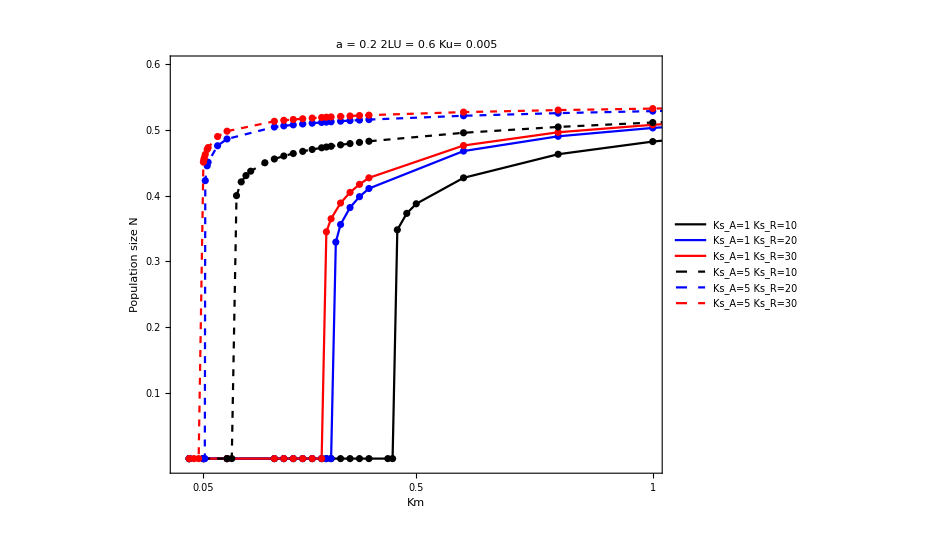

```mathematica
Fig5aAppendixGNoLog=ListPlot[{Transpose[{LENmLU03h002Ns1Ku0005⟦All,1⟧,LENmLU03h002Ns1Ku0005⟦All,2⟧⟦All,1⟧}],Transpose[{LENmLU03h002Ns1bKu0005⟦All,1⟧,LENmLU03h002Ns1bKu0005⟦All,2⟧⟦All,1⟧}],Transpose[{LENmLU03h002Ns1bbKu0005⟦All,1⟧,LENmLU03h002Ns1bbKu0005⟦All,2⟧⟦All,1⟧}],Transpose[{LENmLU03h002Ns1cKu0005⟦All,1⟧,LENmLU03h002Ns1cKu0005⟦All,2⟧⟦All,1⟧}],Transpose[{LENmLU03h002Ns1dKu0005⟦All,1⟧,LENmLU03h002Ns1dKu0005⟦All,2⟧⟦All,1⟧}],Transpose[{LENmLU03h002Ns1eKu0005⟦All,1⟧,LENmLU03h002Ns1eKu0005⟦All,2⟧⟦All,1⟧}]},Joined->True,PlotLabel->Style["a = 0.2        2LU = 0.6        Ku= 0.005",30,FontFamily->"Times"],PlotStyle->{Black,Blue,Red,Directive[Black,Dashed],Directive[Blue,Dashed],Directive[Red,Dashed]},PlotRange->{{0,1.0},{-0.01,0.6}},Mesh->All,Frame->True,PlotLegends->Placed[{Style["Ks_A=1   Ks_R=10",26,FontFamily->"Times"],Style["Ks_A=1   Ks_R=20",26,FontFamily->"Times"],Style["Ks_A=1   Ks_R=30",26,FontFamily->"Times"],Style["Ks_A=5   Ks_R=10",26,FontFamily->"Times"],Style["Ks_A=5   Ks_R=20",26,FontFamily->"Times"],Style["Ks_A=5   Ks_R=30",26,FontFamily->"Times"]},{Right,Bottom}],FrameTicks->{{{0.1,0.2,0.3,0.4,0.5,0.6},None},{{0.05,0.5,1,1.5,2,5,10,20},None}},FrameTicksStyle->Directive[Times,30],FrameLabel->{Row[{Style["",30,Black,Bold],Style["   Km",30]},""],Row[{Style["Population size",30,Black,Bold],Style["  N",30]},""]},AspectRatio->0.8,ImageSize->700]
```

```mathematica
Export["Fig5aAppendixGNoLog.pdf",Fig5aAppendixGNoLog,"PDF","AllowRasterization"->False];
```

a = 0.5

```mathematica
LENmLU03Ns1aKu0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,1,10,Km,0.5,0.02,0.3,80,0.5]⟦1⟧},{Km,{0.02,0.05,0.1,0.2,0.22,0.24,0.26,0.28,0.3,0.31,0.32,0.34,0.36,0.38,0.4,0.46,0.48,0.5,0.6,0.8,1.0,1.1,1.2,1.21,1.22,1.23,1.25,1.3,1.4,1.6,1.8,2.0,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.0357048,0.00410161,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.0740364,0.00529196,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.0315549,0.00318806,Indeterminate,Indeterminate,Indeterminate}},{0.2,{0,0.0265032,0.00305332,Indeterminate,Indeterminate,Indeterminate}},{0.22,{0,0.0435242,0.0206295,Indeterminate,Indeterminate,Indeterminate}},{0.24,{0,0.0346121,0.00548688,Indeterminate,Indeterminate,Indeterminate}},{0.26,{0,0.029318,0.00345906,Indeterminate,Indeterminate,Indeterminate}},{0.28,{0,0.0258117,0.00307904,Indeterminate,Indeterminate,Indeterminate}},{0.3,{0,0.023314,0.00302155,Indeterminate,Indeterminate,Indeterminate}},{0.31,{0,0.0357163,0.0121978,Indeterminate,Indeterminate,Indeterminate}},{0.32,{0,0.0322031,0.00644905,Indeterminate,Indeterminate,Indeterminate}},{0.34,{0,0.0275416,0.00361999,Indeterminate,Indeterminate,Indeterminate}},{0.36,{0,0.0245465,0.00310209,Indeterminate,Indeterminate,Indeterminate}},{0.38,{0,0.0224321,0.00300393,Indeterminate,Indeterminate,Indeterminate}},{0.4,{0,0.0289982,0.00530929,Indeterminate,Indeterminate,Indeterminate}},{0.46,{0,0.0299039,0.00841507,Indeterminate,Indeterminate,Indeterminate}},{0.48,{0,0.0253825,0.00371481,Indeterminate,Indeterminate,Indeterminate}},{0.5,{0,0.0228201,0.00308446,Indeterminate,Indeterminate,Indeterminate}},{0.6,{0,0.0233052,0.00335122,Indeterminate,Indeterminate,Indeterminate}},{0.8,{0,0.021935,0.00323836,Indeterminate,Indeterminate,Indeterminate}},{1.,{0,0.0222105,0.0037042,Indeterminate,Indeterminate,Indeterminate}},{1.1,{0,0.0212277,0.00326509,Indeterminate,Indeterminate,Indeterminate}},{1.2,{0,0.0199336,0.00294712,Indeterminate,Indeterminate,Indeterminate}},{1.21,{0,0.0222234,0.00419346,Indeterminate,Indeterminate,Indeterminate}},{1.22,{0,0.0206446,0.00310717,Indeterminate,Indeterminate,Indeterminate}},{1.23,{0.275958,0.0159806,0.00323438,0.479417,0.244625,0.724042}},{1.25,{0.301589,0.0153413,0.00333017,0.460239,0.238172,0.698411}},{1.3,{0.324499,0.0147499,0.00342893,0.442498,0.233003,0.675501}},{1.4,{0.349795,0.014082,0.00355847,0.422459,0.227746,0.650205}},{1.6,{0.378855,0.0133036,0.00374943,0.399108,0.222037,0.621145}},{1.8,{0.397142,0.0128118,0.00390783,0.384353,0.218505,0.602858}},{2.,{0.410279,0.0124589,0.00405105,0.373767,0.215954,0.589721}},{3.,{0.445057,0.0115282,0.00467159,0.345847,0.209096,0.554943}},{4.,{0.460573,0.0111071,0.00521524,0.333212,0.206215,0.539427}},{5,{0.469134,0.0108629,0.00570932,0.325887,0.204979,0.530866}},{9,{0.481152,0.0104385,0.00730607,0.313155,0.205693,0.518848}},{10,{0.482063,0.0103859,0.00762784,0.311576,0.206362,0.517937}},{11,{0.482635,0.0103428,0.00792448,0.310284,0.207081,0.517365}},{12,{0.482971,0.0103069,0.00819846,0.309207,0.207822,0.517029}},{13,{0.48314,0.0102765,0.00845202,0.308294,0.208566,0.51686}},{14,{0.483189,0.0102504,0.00868716,0.307511,0.2093,0.516811}},{15,{0.483151,0.0102277,0.00890566,0.306831,0.210018,0.516849}},{20,{0.48231,0.010148,0.00979836,0.304441,0.213249,0.51769}},{22,{0.481852,0.0101262,0.0100828,0.303785,0.214364,0.518148}},{24,{0.48138,0.0101079,0.0103356,0.303236,0.215384,0.51862}},{26,{0.480912,0.0100924,0.0105616,0.302771,0.216317,0.519088}},{28,{0.480457,0.010079,0.0107649,0.30237,0.217173,0.519543}},{30,{0.480019,0.0100674,0.0109486,0.302022,0.217959,0.519981}}}

```mathematica
LENmLU03Ns1bKu0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,1,20,Km,0.5,0.02,0.3,80,0.5]⟦1⟧},{Km,{0.02,0.05,0.1,0.2,0.22,0.24,0.26,0.28,0.3,0.31,0.32,0.34,0.36,0.38,0.4,0.6,0.8,1.0,1.05,1.07,1.08,1.09,1.1,1.2,1.4,1.6,1.8,2.0,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.0357048,0.00266983,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.0736576,0.00161151,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.0315614,0.00195448,Indeterminate,Indeterminate,Indeterminate}},{0.2,{0,0.0260865,0.00178003,Indeterminate,Indeterminate,Indeterminate}},{0.22,{0,0.0385385,0.00238462,Indeterminate,Indeterminate,Indeterminate}},{0.24,{0,0.0319212,0.00155375,Indeterminate,Indeterminate,Indeterminate}},{0.26,{0,0.0276672,0.00160846,Indeterminate,Indeterminate,Indeterminate}},{0.28,{0,0.0397966,0.00982367,Indeterminate,Indeterminate,Indeterminate}},{0.3,{0,0.0324547,0.00176639,Indeterminate,Indeterminate,Indeterminate}},{0.31,{0,0.0299945,0.00156005,Indeterminate,Indeterminate,Indeterminate}},{0.32,{0,0.02802,0.00154347,Indeterminate,Indeterminate,Indeterminate}},{0.34,{0,0.0250426,0.00160901,Indeterminate,Indeterminate,Indeterminate}},{0.36,{0,0.0316375,0.00204244,Indeterminate,Indeterminate,Indeterminate}},{0.38,{0,0.0273529,0.00153345,Indeterminate,Indeterminate,Indeterminate}},{0.4,{0,0.0245601,0.00157853,Indeterminate,Indeterminate,Indeterminate}},{0.6,{0,0.0260999,0.00161413,Indeterminate,Indeterminate,Indeterminate}},{0.8,{0,0.0240736,0.00153171,Indeterminate,Indeterminate,Indeterminate}},{1.,{0,0.0254658,0.00256422,Indeterminate,Indeterminate,Indeterminate}},{1.05,{0,0.0234784,0.0015704,Indeterminate,Indeterminate,Indeterminate}},{1.07,{0,0.0244482,0.00194124,Indeterminate,Indeterminate,Indeterminate}},{1.08,{0.279321,0.0166649,0.00188706,0.499947,0.220732,0.720679}},{1.09,{0.292547,0.0162769,0.00192074,0.488306,0.219147,0.707453}},{1.1,{0.300567,0.0160394,0.00194161,0.481183,0.21825,0.699433}},{1.2,{0.339682,0.0148633,0.00205109,0.445898,0.21442,0.660318}},{1.4,{0.37517,0.0137787,0.00217121,0.413362,0.211468,0.62483}},{1.6,{0.395594,0.0131506,0.00225889,0.394518,0.209889,0.604406}},{1.8,{0.409625,0.0127182,0.00233353,0.381547,0.208828,0.590375}},{2.,{0.420055,0.0123965,0.00240099,0.371896,0.208049,0.579945}},{3.,{0.448472,0.0115155,0.00269069,0.345465,0.206063,0.551528}},{4.,{0.46133,0.0111051,0.00294473,0.333152,0.205519,0.53867}},{5,{0.468415,0.0108644,0.00317902,0.325932,0.205653,0.531585}},{9,{0.477914,0.0104422,0.00397438,0.313265,0.208822,0.522086}},{10,{0.478465,0.0103895,0.00414332,0.311686,0.209849,0.521535}},{11,{0.478714,0.0103464,0.00430195,0.310393,0.210893,0.521286}},{12,{0.478749,0.0103105,0.00445101,0.309315,0.211936,0.521251}},{13,{0.478634,0.01028,0.00459121,0.308401,0.212965,0.521366}},{14,{0.478411,0.0102539,0.0047232,0.307616,0.213973,0.521589}},{15,{0.47811,0.0102312,0.00484759,0.306935,0.214955,0.52189}},{20,{0.476068,0.0101513,0.00537395,0.304538,0.219394,0.523932}},{22,{0.475173,0.0101293,0.00554801,0.30388,0.220947,0.524827}},{24,{0.474287,0.010111,0.00570542,0.303329,0.222383,0.525713}},{26,{0.473428,0.0100954,0.00584837,0.302862,0.223711,0.526572}},{28,{0.472602,0.010082,0.00597869,0.30246,0.224939,0.527398}},{30,{0.471814,0.0100703,0.00609795,0.30211,0.226076,0.528186}}}

```mathematica
LENmLU03Ns1bbKu0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,1,30,Km,0.5,0.02,0.3,80,0.5]⟦1⟧},{Km,{0.02,0.05,0.1,0.2,0.22,0.24,0.26,0.28,0.3,0.31,0.32,0.34,0.36,0.38,0.4,0.6,0.8,1.0,1.02,1.03,1.05,1.1,1.2,1.4,1.6,1.8,2.0,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.0357048,0.00207945,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.0738307,0.00114753,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.0316674,0.00149733,Indeterminate,Indeterminate,Indeterminate}},{0.2,{0,0.048536,0.0240249,Indeterminate,Indeterminate,Indeterminate}},{0.22,{0,0.0377612,0.0010885,Indeterminate,Indeterminate,Indeterminate}},{0.24,{0,0.0314549,0.00111187,Indeterminate,Indeterminate,Indeterminate}},{0.26,{0,0.0273633,0.00121134,Indeterminate,Indeterminate,Indeterminate}},{0.28,{0,0.0378115,0.00213534,Indeterminate,Indeterminate,Indeterminate}},{0.3,{0,0.0313854,0.00104683,Indeterminate,Indeterminate,Indeterminate}},{0.31,{0,0.029165,0.00108989,Indeterminate,Indeterminate,Indeterminate}},{0.32,{0,0.0273598,0.00113846,Indeterminate,Indeterminate,Indeterminate}},{0.34,{0,0.0358468,0.00259295,Indeterminate,Indeterminate,Indeterminate}},{0.36,{0,0.0299822,0.00103742,Indeterminate,Indeterminate,Indeterminate}},{0.38,{0,0.0263777,0.00111919,Indeterminate,Indeterminate,Indeterminate}},{0.4,{0,0.0323663,0.00137812,Indeterminate,Indeterminate,Indeterminate}},{0.6,{0,0.0286131,0.00121033,Indeterminate,Indeterminate,Indeterminate}},{0.8,{0,0.0272325,0.0013115,Indeterminate,Indeterminate,Indeterminate}},{1.,{0,0.0251488,0.00104916,Indeterminate,Indeterminate,Indeterminate}},{1.02,{0,0.0243718,0.0010071,Indeterminate,Indeterminate,Indeterminate}},{1.03,{0.26833,0.0172848,0.0013934,0.518545,0.213125,0.73167}},{1.05,{0.297838,0.016371,0.00145189,0.491129,0.211033,0.702162}},{1.1,{0.323476,0.0155654,0.00150439,0.466961,0.209563,0.676524}},{1.2,{0.35113,0.0146875,0.00156508,0.440626,0.208244,0.64887}},{1.4,{0.381769,0.0137067,0.00164272,0.411202,0.207029,0.618231}},{1.6,{0.400303,0.0131099,0.00170017,0.393298,0.206399,0.599697}},{1.8,{0.413219,0.0126924,0.00174869,0.380771,0.20601,0.586781}},{2.,{0.422873,0.0123791,0.00179215,0.371373,0.205754,0.577127}},{3.,{0.449228,0.0115127,0.00197571,0.345381,0.205391,0.550772}},{4.,{0.461092,0.0111057,0.00213502,0.333171,0.205737,0.538908}},{5,{0.467586,0.0108661,0.00228217,0.325984,0.206431,0.532414}},{9,{0.476069,0.0104443,0.0027909,0.313328,0.210603,0.523931}},{10,{0.47649,0.0103916,0.00290146,0.311747,0.211763,0.52351}},{11,{0.476625,0.0103484,0.0030062,0.310452,0.212923,0.523375}},{12,{0.476558,0.0103124,0.00310545,0.309372,0.214071,0.523442}},{13,{0.476345,0.0102819,0.00319955,0.308456,0.215199,0.523655}},{14,{0.476029,0.0102556,0.00328882,0.307669,0.216301,0.523971}},{15,{0.475638,0.0102329,0.00337356,0.306987,0.217375,0.524362}},{20,{0.473157,0.0101528,0.00373887,0.304585,0.222258,0.526843}},{22,{0.472091,0.0101308,0.00386211,0.303925,0.223984,0.527909}},{24,{0.471038,0.0101124,0.00397461,0.303373,0.225589,0.528962}},{26,{0.470013,0.0100968,0.00407766,0.302904,0.227082,0.529987}},{28,{0.469027,0.0100834,0.00417234,0.302501,0.228472,0.530973}},{30,{0.468083,0.0100717,0.0042596,0.302151,0.229766,0.531917}}}

```mathematica
LENmLU03Ns1cKu0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,5,10,Km,0.5,0.02,0.3,80,0.5]⟦1⟧},{Km,{0.02,0.05,0.1,0.12,0.13,0.14,0.15,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.36,0.4,0.5,0.56,0.57,0.58,0.6,0.8,1.0,1.1,1.2,1.4,1.6,1.8,2.0,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.10921,0.0683207,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.0101147,0.00343102,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.0263865,0.0141337,Indeterminate,Indeterminate,Indeterminate}},{0.12,{0,0.0108795,0.00427472,Indeterminate,Indeterminate,Indeterminate}},{0.13,{0,0.00830674,0.00353638,Indeterminate,Indeterminate,Indeterminate}},{0.14,{0,0.00679621,0.00323973,Indeterminate,Indeterminate,Indeterminate}},{0.15,{0,0.00583555,0.0031104,Indeterminate,Indeterminate,Indeterminate}},{0.18,{0,0.0221835,0.0155986,Indeterminate,Indeterminate,Indeterminate}},{0.2,{0,0.00952012,0.00438263,Indeterminate,Indeterminate,Indeterminate}},{0.22,{0,0.00615183,0.00322693,Indeterminate,Indeterminate,Indeterminate}},{0.24,{0,0.00481496,0.0030255,Indeterminate,Indeterminate,Indeterminate}},{0.26,{0,0.0126582,0.00724741,Indeterminate,Indeterminate,Indeterminate}},{0.28,{0,0.00660876,0.003446,Indeterminate,Indeterminate,Indeterminate}},{0.3,{0,0.00483883,0.00303237,Indeterminate,Indeterminate,Indeterminate}},{0.36,{0,0.0156181,0.0128474,Indeterminate,Indeterminate,Indeterminate}},{0.4,{0,0.0112672,0.00751513,Indeterminate,Indeterminate,Indeterminate}},{0.5,{0,0.00617235,0.0035888,Indeterminate,Indeterminate,Indeterminate}},{0.56,{0,0.00482376,0.00308456,Indeterminate,Indeterminate,Indeterminate}},{0.57,{0,0.00445088,0.00299896,Indeterminate,Indeterminate,Indeterminate}},{0.58,{0.314972,0.00289046,0.00314408,0.43357,0.251459,0.685028}},{0.6,{0.336416,0.00278806,0.0032068,0.41821,0.245374,0.663584}},{0.8,{0.384241,0.00255672,0.00342008,0.383508,0.232252,0.615759}},{1.,{0.403744,0.00246435,0.00356759,0.369653,0.226603,0.596256}},{1.1,{0.410626,0.00243236,0.00363525,0.364854,0.224521,0.589374}},{1.2,{0.416404,0.00240576,0.00370064,0.360864,0.222732,0.583596}},{1.4,{0.425708,0.00236344,0.00382687,0.354515,0.219776,0.574292}},{1.6,{0.432986,0.00233073,0.00394893,0.349609,0.217404,0.567014}},{1.8,{0.438897,0.00230437,0.00406801,0.345655,0.215448,0.561103}},{2.,{0.443819,0.00228249,0.00418473,0.342374,0.213807,0.556181}},{3.,{0.459842,0.00221069,0.00474086,0.331604,0.208554,0.540158}},{4.,{0.468509,0.00216963,0.00525714,0.325444,0.206048,0.531491}},{5,{0.473691,0.00214252,0.00573559,0.321378,0.204931,0.526309}},{9,{0.481154,0.00208768,0.00730608,0.313152,0.205693,0.518846}},{10,{0.481641,0.00208002,0.00762493,0.312004,0.206355,0.518359}},{11,{0.481894,0.00207359,0.00791931,0.311038,0.207068,0.518106}},{12,{0.481983,0.00206809,0.00819155,0.310214,0.207803,0.518017}},{13,{0.481957,0.00206335,0.00844374,0.309502,0.208541,0.518043}},{14,{0.481848,0.00205921,0.00867781,0.308881,0.209271,0.518152}},{15,{0.481682,0.00205556,0.00889548,0.308333,0.209984,0.518318}},{20,{0.480454,0.00204229,0.00978615,0.306344,0.213202,0.519546}},{22,{0.479906,0.00203853,0.0100703,0.30578,0.214314,0.520094}},{24,{0.479366,0.00203534,0.010323,0.305301,0.215333,0.520634}},{26,{0.478844,0.0020326,0.0105491,0.304891,0.216265,0.521156}},{28,{0.478345,0.00203023,0.0107525,0.304534,0.217121,0.521655}},{30,{0.477872,0.00202814,0.0109364,0.304221,0.217906,0.522128}}}

```mathematica
LENmLU03Ns1dKu0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,5,20,Km,0.5,0.02,0.3,80,0.5]⟦1⟧},{Km,{0.02,0.05,0.08,0.1,0.2,0.3,0.31,0.36,0.38,0.4,0.41,0.42,0.43,0.48,0.5,0.6,0.8,1.0,1.1,1.2,1.4,1.6,1.8,2.0,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{0.02,{0,0.0704113,0.00486925,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.00812793,0.00173601,Indeterminate,Indeterminate,Indeterminate}},{0.08,{0,0.0305336,0.00446166,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.0102621,0.00157687,Indeterminate,Indeterminate,Indeterminate}},{0.2,{0,0.0102616,0.00163753,Indeterminate,Indeterminate,Indeterminate}},{0.3,{0,0.00557961,0.00155912,Indeterminate,Indeterminate,Indeterminate}},{0.31,{0,0.00840017,0.00162964,Indeterminate,Indeterminate,Indeterminate}},{0.36,{0,0.00888031,0.00181085,Indeterminate,Indeterminate,Indeterminate}},{0.38,{0,0.00492099,0.00156649,Indeterminate,Indeterminate,Indeterminate}},{0.4,{0,0.00661434,0.00153463,Indeterminate,Indeterminate,Indeterminate}},{0.41,{0,0.0116413,0.00368277,Indeterminate,Indeterminate,Indeterminate}},{0.42,{0.33836,0.00295232,0.00190585,0.442848,0.218791,0.66164}},{0.43,{0.346873,0.002901,0.00192445,0.435149,0.217978,0.653127}},{0.48,{0.368886,0.00276768,0.00197682,0.415153,0.215961,0.631114}},{0.5,{0.374411,0.00273417,0.00199141,0.410125,0.215464,0.625589}},{0.6,{0.392767,0.00262296,0.00204695,0.393443,0.213789,0.607233}},{0.8,{0.412384,0.00250502,0.00212707,0.375753,0.211863,0.587616}},{1.,{0.424067,0.00243561,0.00219354,0.365342,0.210591,0.575933}},{1.1,{0.42849,0.00240954,0.00222444,0.361431,0.210079,0.57151}},{1.2,{0.432296,0.0023872,0.00225435,0.35808,0.209624,0.567704}},{1.4,{0.438573,0.00235054,0.00231203,0.35258,0.208847,0.561427}},{1.6,{0.443589,0.00232137,0.00236769,0.348205,0.208206,0.556411}},{1.8,{0.447722,0.00229738,0.00242192,0.344607,0.207671,0.552278}},{2.,{0.451201,0.00227718,0.00247503,0.341577,0.207221,0.548799}},{3.,{0.462741,0.00220924,0.00272882,0.331386,0.205874,0.537259}},{4.,{0.469103,0.00216939,0.00296768,0.325409,0.205487,0.530897}},{5,{0.472917,0.00214277,0.00319343,0.321415,0.205668,0.527083}},{9,{0.477931,0.00208831,0.00397445,0.313247,0.208822,0.522069}},{10,{0.478061,0.00208066,0.00414171,0.312099,0.209839,0.521939}},{11,{0.477992,0.00207423,0.00429902,0.311134,0.210874,0.522008}},{12,{0.477782,0.00206873,0.00444702,0.31031,0.211908,0.522218}},{13,{0.477473,0.00206399,0.00458637,0.309598,0.212929,0.522527}},{14,{0.477093,0.00205984,0.00471766,0.308976,0.213931,0.522907}},{15,{0.476666,0.00205619,0.00484149,0.308428,0.214906,0.523334}},{20,{0.474238,0.0020429,0.00536626,0.306436,0.219326,0.525762}},{22,{0.473255,0.00203913,0.00554004,0.30587,0.220876,0.526745}},{24,{0.472302,0.00203593,0.00569728,0.30539,0.222309,0.527698}},{26,{0.471388,0.00203318,0.00584015,0.304978,0.223634,0.528612}},{28,{0.47052,0.0020308,0.00597045,0.30462,0.224861,0.52948}},{30,{0.469697,0.0020287,0.00608973,0.304305,0.225998,0.530303}}}

```mathematica
LENmLU03Ns1eKu0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,5,30,Km,0.5,0.02,0.3,80,0.5]⟦1⟧},{Km,{0.02,0.05,0.08,0.1,0.2,0.3,0.31,0.36,0.37,0.38,0.4,0.43,0.48,0.5,0.6,0.8,1.0,1.1,1.2,1.4,1.6,1.8,2.0,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.0678351,0.00135568,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.00791595,0.00133053,Indeterminate,Indeterminate,Indeterminate}},{0.08,{0,0.0249688,0.00117013,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.00907644,0.00118568,Indeterminate,Indeterminate,Indeterminate}},{0.2,{0,0.00651755,0.00116336,Indeterminate,Indeterminate,Indeterminate}},{0.3,{0,0.00692219,0.00107607,Indeterminate,Indeterminate,Indeterminate}},{0.31,{0,0.00686372,0.00107339,Indeterminate,Indeterminate,Indeterminate}},{0.36,{0,0.0103676,0.00120804,Indeterminate,Indeterminate,Indeterminate}},{0.37,{0,0.00947185,0.00110304,Indeterminate,Indeterminate,Indeterminate}},{0.38,{0.338288,0.00300798,0.00144945,0.451197,0.210515,0.661712}},{0.4,{0.355692,0.00289766,0.00147901,0.434649,0.209659,0.644308}},{0.43,{0.369388,0.00281053,0.00150363,0.421579,0.209033,0.630612}},{0.48,{0.383304,0.0027218,0.00153087,0.40827,0.208427,0.616696}},{0.5,{0.38742,0.00269553,0.00153956,0.40433,0.208251,0.61258}},{0.6,{0.402155,0.00260147,0.00157442,0.390221,0.207624,0.597845}},{0.8,{0.418976,0.0024942,0.00162598,0.37413,0.206894,0.581024}},{1.,{0.429242,0.00242883,0.00166852,0.364325,0.206433,0.570758}},{1.1,{0.433149,0.00240397,0.00168816,0.360595,0.206256,0.566851}},{1.2,{0.436514,0.00238255,0.0017071,0.357382,0.206104,0.563486}},{1.4,{0.442064,0.00234719,0.00174343,0.352078,0.205858,0.557936}},{1.6,{0.446493,0.00231889,0.00177831,0.347834,0.205673,0.553507}},{1.8,{0.450136,0.00229552,0.00181217,0.344329,0.205536,0.549864}},{2.,{0.453195,0.00227578,0.00184523,0.341367,0.205437,0.546805}},{3.,{0.463284,0.00220897,0.00200273,0.331345,0.205371,0.536716}},{4.,{0.468795,0.00216951,0.00215113,0.325427,0.205778,0.531205}},{5,{0.472064,0.00214304,0.00229224,0.321457,0.20648,0.527936}},{9,{0.476095,0.00208867,0.00279097,0.313301,0.210604,0.523905}},{10,{0.476096,0.00208102,0.00290036,0.312153,0.211751,0.523904}},{11,{0.475914,0.00207457,0.00300416,0.311186,0.2129,0.524086}},{12,{0.475601,0.00206907,0.00310266,0.310361,0.214038,0.524399}},{13,{0.475195,0.00206432,0.00319614,0.309648,0.215158,0.524805}},{14,{0.474722,0.00206016,0.0032849,0.309024,0.216253,0.525278}},{15,{0.474205,0.0020565,0.00336923,0.308475,0.21732,0.525795}},{20,{0.47134,0.00204319,0.00373329,0.306479,0.222181,0.52866}},{22,{0.470186,0.00203941,0.00385628,0.305912,0.223902,0.529814}},{24,{0.469065,0.00203621,0.00396862,0.305431,0.225503,0.530935}},{26,{0.467988,0.00203346,0.00407156,0.305018,0.226994,0.532012}},{28,{0.466959,0.00203106,0.00416619,0.304659,0.228381,0.533041}},{30,{0.465981,0.00202896,0.00425343,0.304345,0.229674,0.534019}}}

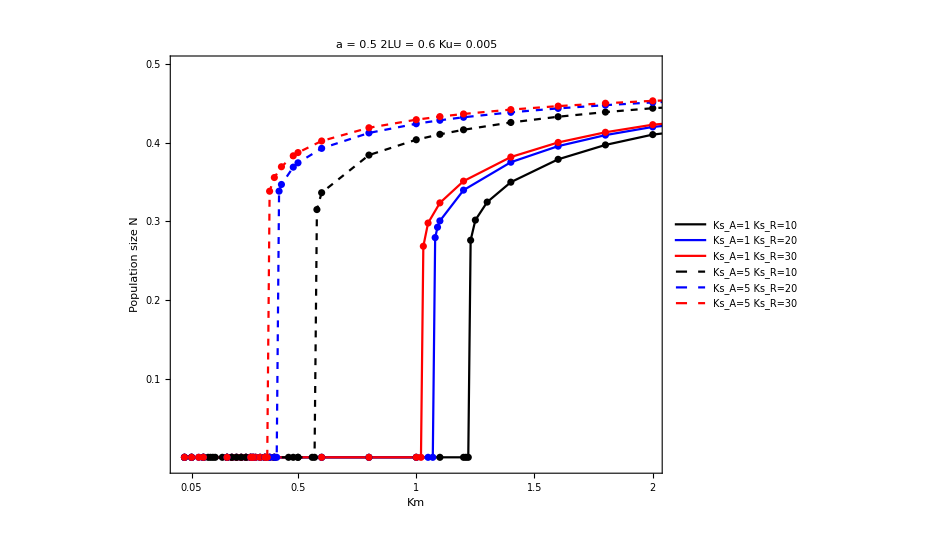

```mathematica
Fig5bAppendixGNoLog=ListPlot[{Transpose[{LENmLU03Ns1aKu0005⟦All,1⟧,LENmLU03Ns1aKu0005⟦All,2⟧⟦All,1⟧}],Transpose[{LENmLU03Ns1bKu0005⟦All,1⟧,LENmLU03Ns1bKu0005⟦All,2⟧⟦All,1⟧}],Transpose[{LENmLU03Ns1bbKu0005⟦All,1⟧,LENmLU03Ns1bbKu0005⟦All,2⟧⟦All,1⟧}],Transpose[{LENmLU03Ns1cKu0005⟦All,1⟧,LENmLU03Ns1cKu0005⟦All,2⟧⟦All,1⟧}],Transpose[{LENmLU03Ns1dKu0005⟦All,1⟧,LENmLU03Ns1dKu0005⟦All,2⟧⟦All,1⟧}],Transpose[{LENmLU03Ns1eKu0005⟦All,1⟧,LENmLU03Ns1eKu0005⟦All,2⟧⟦All,1⟧}]},Joined->True,Mesh->All,Frame->True,PlotLabel->Style["a = 0.5        2LU = 0.6        Ku= 0.005",30,FontFamily->"Times"],PlotStyle->{Black,Blue,Red,Directive[Black,Dashed],Directive[Blue,Dashed],Directive[Red,Dashed]},PlotRange->{{0,2.0},{-0.01,0.5}},Mesh->All,Frame->True,PlotLegends->Placed[{Style["Ks_A=1   Ks_R=10",26,FontFamily->"Times"],Style["Ks_A=1   Ks_R=20",26,FontFamily->"Times"],Style["Ks_A=1   Ks_R=30",26,FontFamily->"Times"],Style["Ks_A=5   Ks_R=10",26,FontFamily->"Times"],Style["Ks_A=5   Ks_R=20",26,FontFamily->"Times"],Style["Ks_A=5   Ks_R=30",26,FontFamily->"Times"]},{Right,Bottom}],FrameTicks->{{{0.1,0.2,0.3,0.4,0.5},None},{{0.05,0.5,1,1.5,2},None}},FrameTicksStyle->Directive[Times,30],FrameLabel->{Row[{Style["",30,Black,Bold],Style["   Km",30]},""],Row[{Style["Population size",30,Black,Bold],Style["  N",30]},""]},AspectRatio->0.8,ImageSize->700]
```

```mathematica
Export["Fig5bAppendixGNoLog.pdf",Fig5bAppendixGNoLog,"PDF","AllowRasterization"->False];
```

a = 0.8

```mathematica
LENmLU03Ns1a1Ku0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,1,10,Km,0.5,0.02,0.3,80,0.8]⟦1⟧},{Km,{0.02,0.05,0.1,0.2,0.22,0.24,0.26,0.28,0.3,0.31,0.32,0.34,0.36,0.38,0.4,0.46,0.48,0.5,0.6,0.8,1.0,1.1,1.2,1.3,1.4,1.6,1.8,2.0,2.1,2.2,2.27,2.28,2.29,2.3,2.35,2.4,2.5,2.6,2.8,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.0357048,0.00410161,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.0207535,0.00403062,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.0382566,0.00319213,Indeterminate,Indeterminate,Indeterminate}},{0.2,{0,0.0371528,0.0108647,Indeterminate,Indeterminate,Indeterminate}},{0.22,{0,0.0304702,0.00442258,Indeterminate,Indeterminate,Indeterminate}},{0.24,{0,0.0261136,0.00329079,Indeterminate,Indeterminate,Indeterminate}},{0.26,{0,0.0230814,0.00307347,Indeterminate,Indeterminate,Indeterminate}},{0.28,{0,0.0208608,0.00306285,Indeterminate,Indeterminate,Indeterminate}},{0.3,{0,0.0191674,0.00310632,Indeterminate,Indeterminate,Indeterminate}},{0.31,{0,0.0332959,0.0174814,Indeterminate,Indeterminate,Indeterminate}},{0.32,{0,0.0303485,0.00946421,Indeterminate,Indeterminate,Indeterminate}},{0.34,{0,0.026111,0.00451525,Indeterminate,Indeterminate,Indeterminate}},{0.36,{0,0.023223,0.00338419,Indeterminate,Indeterminate,Indeterminate}},{0.38,{0,0.021131,0.00309327,Indeterminate,Indeterminate,Indeterminate}},{0.4,{0,0.019544,0.00303442,Indeterminate,Indeterminate,Indeterminate}},{0.46,{0,0.0227189,0.00374551,Indeterminate,Indeterminate,Indeterminate}},{0.48,{0,0.0207927,0.00319524,Indeterminate,Indeterminate,Indeterminate}},{0.5,{0,0.0193483,0.00304191,Indeterminate,Indeterminate,Indeterminate}},{0.6,{0,0.0187814,0.00303331,Indeterminate,Indeterminate,Indeterminate}},{0.8,{0,0.0217157,0.00506966,Indeterminate,Indeterminate,Indeterminate}},{1.,{0,0.0217675,0.00662273,Indeterminate,Indeterminate,Indeterminate}},{1.1,{0,0.0180836,0.00307356,Indeterminate,Indeterminate,Indeterminate}},{1.2,{0,0.0182853,0.00316007,Indeterminate,Indeterminate,Indeterminate}},{1.3,{0,0.0178414,0.00305594,Indeterminate,Indeterminate,Indeterminate}},{1.4,{0,0.0195328,0.00426939,Indeterminate,Indeterminate,Indeterminate}},{1.6,{0,0.0184438,0.00341269,Indeterminate,Indeterminate,Indeterminate}},{1.8,{0,0.0176945,0.00307634,Indeterminate,Indeterminate,Indeterminate}},{2.,{0,0.0180623,0.00329481,Indeterminate,Indeterminate,Indeterminate}},{2.1,{0,0.0172126,0.00295203,Indeterminate,Indeterminate,Indeterminate}},{2.2,{0,0.0191631,0.00483348,Indeterminate,Indeterminate,Indeterminate}},{2.27,{0,0.0177942,0.00317353,Indeterminate,Indeterminate,Indeterminate}},{2.28,{0,0.0191261,0.0048489,Indeterminate,Indeterminate,Indeterminate}},{2.29,{0.24268,0.0138166,0.00341388,0.663197,0.094123,0.75732}},{2.3,{0.249336,0.0136919,0.00344894,0.657211,0.0934533,0.750664}},{2.35,{0.266768,0.0133633,0.00354874,0.641441,0.0917915,0.733232}},{2.4,{0.27758,0.0131584,0.00361753,0.631602,0.0908182,0.72242}},{2.5,{0.292901,0.0128667,0.0037265,0.617599,0.0895001,0.707099}},{2.6,{0.304216,0.0126504,0.00381782,0.607219,0.0885646,0.695784}},{2.8,{0.320948,0.0123297,0.00397537,0.591824,0.0872285,0.679052}},{3.,{0.333291,0.0120924,0.00411473,0.580437,0.0862729,0.666709}},{4.,{0.368354,0.0114154,0.00470058,0.54794,0.083706,0.631646}},{5,{0.385872,0.0110735,0.00520233,0.53153,0.0825983,0.614128}},{9,{0.412643,0.0105283,0.00680969,0.505359,0.0819982,0.587357}},{10,{0.415555,0.0104639,0.0071378,0.502268,0.0821765,0.584445}},{11,{0.417841,0.0104117,0.00744207,0.499761,0.0823982,0.582159}},{12,{0.419669,0.0103684,0.00772465,0.497685,0.0826456,0.580331}},{13,{0.421156,0.010332,0.0079875,0.495937,0.082907,0.578844}},{14,{0.422382,0.0103009,0.00823237,0.494444,0.0831746,0.577618}},{15,{0.423404,0.010274,0.00846087,0.493153,0.083443,0.576596}},{20,{0.426631,0.0101804,0.00940338,0.48866,0.0847088,0.573369}},{22,{0.4274,0.010155,0.00970641,0.48744,0.0851606,0.5726}},{24,{0.427998,0.0101338,0.00997676,0.486423,0.0855791,0.572002}},{26,{0.428471,0.0101159,0.0102193,0.485563,0.0859656,0.571529}},{28,{0.428851,0.0101006,0.0104378,0.484827,0.0863224,0.571149}},{30,{0.42916,0.0100873,0.0106358,0.484188,0.0866519,0.57084}}}

```mathematica
LENmLU03Ns1b1Ku0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,1,20,Km,0.5,0.02,0.3,80,0.8]⟦1⟧},{Km,{0.02,0.05,0.1,0.2,0.22,0.24,0.26,0.28,0.3,0.31,0.32,0.34,0.36,0.38,0.4,0.6,0.8,1.0,1.1,1.2,1.4,1.6,1.8,2.0,2.2,2.201,2.202,2.205,2.208,2.21,2.23,2.25,2.27,2.3,2.5,2.8,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.0357048,0.00266983,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.0207535,0.00263997,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.0382602,0.00170384,Indeterminate,Indeterminate,Indeterminate}},{0.2,{0,0.0367198,0.00363165,Indeterminate,Indeterminate,Indeterminate}},{0.22,{0,0.0302122,0.00160217,Indeterminate,Indeterminate,Indeterminate}},{0.24,{0,0.0259518,0.00160218,Indeterminate,Indeterminate,Indeterminate}},{0.26,{0,0.022977,0.00169073,Indeterminate,Indeterminate,Indeterminate}},{0.28,{0,0.0207926,0.00177206,Indeterminate,Indeterminate,Indeterminate}},{0.3,{0,0.0191231,0.00184131,Indeterminate,Indeterminate,Indeterminate}},{0.31,{0,0.0320024,0.00713445,Indeterminate,Indeterminate,Indeterminate}},{0.32,{0,0.0293758,0.00290196,Indeterminate,Indeterminate,Indeterminate}},{0.34,{0,0.025519,0.00160987,Indeterminate,Indeterminate,Indeterminate}},{0.36,{0,0.0228358,0.0015661,Indeterminate,Indeterminate,Indeterminate}},{0.38,{0,0.0208647,0.00163011,Indeterminate,Indeterminate,Indeterminate}},{0.4,{0,0.0193542,0.00169938,Indeterminate,Indeterminate,Indeterminate}},{0.6,{0,0.025449,0.00541036,Indeterminate,Indeterminate,Indeterminate}},{0.8,{0,0.0196612,0.00152569,Indeterminate,Indeterminate,Indeterminate}},{1.,{0,0.0186999,0.00151047,Indeterminate,Indeterminate,Indeterminate}},{1.1,{0,0.0189399,0.00151905,Indeterminate,Indeterminate,Indeterminate}},{1.2,{0,0.0185117,0.00150448,Indeterminate,Indeterminate,Indeterminate}},{1.4,{0,0.0211179,0.00408655,Indeterminate,Indeterminate,Indeterminate}},{1.6,{0,0.0191719,0.001735,Indeterminate,Indeterminate,Indeterminate}},{1.8,{0,0.0201614,0.00331254,Indeterminate,Indeterminate,Indeterminate}},{2.,{0,0.0181214,0.00150904,Indeterminate,Indeterminate,Indeterminate}},{2.2,{0,0.0178178,0.00148309,Indeterminate,Indeterminate,Indeterminate}},{2.201,{0.23427,0.0141173,0.00192399,0.67763,0.0881001,0.76573}},{2.202,{0.236213,0.0140792,0.00193023,0.675801,0.0879867,0.763787}},{2.205,{0.239945,0.0140059,0.00194234,0.672281,0.0877735,0.760055}},{2.208,{0.242596,0.0139537,0.00195104,0.669778,0.0876254,0.757404}},{2.21,{0.244082,0.0139245,0.00195594,0.668375,0.0875437,0.755918}},{2.23,{0.254255,0.0137237,0.00199028,0.65874,0.0870056,0.745745}},{2.25,{0.261132,0.0135876,0.00201432,0.652206,0.0866616,0.738868}},{2.27,{0.266637,0.0134785,0.00203411,0.646966,0.0863967,0.733363}},{2.3,{0.273455,0.013343,0.00205939,0.640465,0.0860804,0.726545}},{2.5,{0.301969,0.012774,0.0021774,0.613154,0.0848772,0.698031}},{2.8,{0.326102,0.01229,0.00230143,0.589918,0.0839794,0.673898}},{3.,{0.337234,0.012066,0.00237082,0.579169,0.0835972,0.662766}},{4.,{0.369698,0.0114098,0.00265766,0.547671,0.0826316,0.630302}},{5,{0.386194,0.0110725,0.00290102,0.531482,0.0823235,0.613806}},{9,{0.411576,0.0105299,0.00370269,0.505438,0.0829863,0.588424}},{10,{0.414324,0.0104656,0.00387349,0.502349,0.083327,0.585676}},{11,{0.416467,0.0104134,0.00403454,0.499842,0.0836907,0.583533}},{12,{0.418167,0.0103701,0.00418653,0.497766,0.0840667,0.581833}},{13,{0.419536,0.0103337,0.00433009,0.496017,0.0844474,0.580464}},{14,{0.420649,0.0103026,0.00446579,0.494523,0.0848277,0.579351}},{15,{0.421564,0.0102757,0.00459417,0.493232,0.085204,0.578436}},{20,{0.424306,0.010182,0.00514247,0.488734,0.0869598,0.575694}},{22,{0.424898,0.0101565,0.00532547,0.487512,0.0875901,0.575102}},{24,{0.425328,0.0101353,0.0054916,0.486494,0.0881782,0.574672}},{26,{0.425642,0.0101173,0.00564297,0.485632,0.0887259,0.574358}},{28,{0.42587,0.010102,0.00578135,0.484894,0.0892357,0.57413}},{30,{0.426035,0.0100886,0.00590827,0.484254,0.0897104,0.573965}}}

```mathematica
LENmLU03Ns1bb1Ku0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,1,30,Km,0.5,0.02,0.3,80,0.8]⟦1⟧},{Km,{0.02,0.05,0.1,0.2,0.22,0.24,0.26,0.28,0.3,0.31,0.32,0.34,0.36,0.38,0.4,0.6,0.8,1.0,1.1,1.2,1.4,1.6,1.8,2.0,2.1,2.15,2.16,2.17,2.19,2.2,2.25,2.3,2.5,2.8,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.0357048,0.00207945,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.0207535,0.00206127,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.0383198,0.00128672,Indeterminate,Indeterminate,Indeterminate}},{0.2,{0,0.0366855,0.00162008,Indeterminate,Indeterminate,Indeterminate}},{0.22,{0,0.0301961,0.00107618,Indeterminate,Indeterminate,Indeterminate}},{0.24,{0,0.0259456,0.00118076,Indeterminate,Indeterminate,Indeterminate}},{0.26,{0,0.0229765,0.00126931,Indeterminate,Indeterminate,Indeterminate}},{0.28,{0,0.0207958,0.00133949,Indeterminate,Indeterminate,Indeterminate}},{0.3,{0,0.0191285,0.00139669,Indeterminate,Indeterminate,Indeterminate}},{0.31,{0,0.0317557,0.00364627,Indeterminate,Indeterminate,Indeterminate}},{0.32,{0,0.029185,0.00134823,Indeterminate,Indeterminate,Indeterminate}},{0.34,{0,0.0253983,0.00105757,Indeterminate,Indeterminate,Indeterminate}},{0.36,{0,0.0227553,0.00113658,Indeterminate,Indeterminate,Indeterminate}},{0.38,{0,0.020809,0.00121278,Indeterminate,Indeterminate,Indeterminate}},{0.4,{0,0.0193146,0.001276,Indeterminate,Indeterminate,Indeterminate}},{0.6,{0,0.0246248,0.00193196,Indeterminate,Indeterminate,Indeterminate}},{0.8,{0,0.0192712,0.00106801,Indeterminate,Indeterminate,Indeterminate}},{1.,{0,0.0221488,0.00209183,Indeterminate,Indeterminate,Indeterminate}},{1.1,{0,0.0220313,0.00255022,Indeterminate,Indeterminate,Indeterminate}},{1.2,{0,0.0204744,0.00119757,Indeterminate,Indeterminate,Indeterminate}},{1.4,{0,0.0186023,0.0010141,Indeterminate,Indeterminate,Indeterminate}},{1.6,{0,0.0186272,0.00100567,Indeterminate,Indeterminate,Indeterminate}},{1.8,{0,0.0185119,0.0010026,Indeterminate,Indeterminate,Indeterminate}},{2.,{0,0.0183972,0.00100002,Indeterminate,Indeterminate,Indeterminate}},{2.1,{0,0.0185112,0.00100705,Indeterminate,Indeterminate,Indeterminate}},{2.15,{0,0.0186592,0.00102658,Indeterminate,Indeterminate,Indeterminate}},{2.16,{0,0.0182393,0.000996779,Indeterminate,Indeterminate,Indeterminate}},{2.17,{0.238064,0.0141022,0.00143019,0.676907,0.0850295,0.761936}},{2.19,{0.251044,0.0138409,0.00146278,0.664362,0.0845944,0.748956}},{2.2,{0.255139,0.0137582,0.00147328,0.660394,0.0844668,0.744861}},{2.25,{0.269463,0.0134684,0.00151109,0.646485,0.0840528,0.730537}},{2.3,{0.279442,0.013266,0.00153867,0.636766,0.0837912,0.720558}},{2.5,{0.305123,0.0127431,0.00161658,0.611671,0.0832055,0.694877}},{2.8,{0.327982,0.0122758,0.00169954,0.589239,0.0827794,0.672018}},{3.,{0.338676,0.0120565,0.00174553,0.578713,0.0826117,0.661324}},{4.,{0.370124,0.011408,0.0019323,0.547586,0.0822904,0.629876}},{5,{0.386185,0.0110726,0.00208843,0.531484,0.0823309,0.613815}},{9,{0.410952,0.0105309,0.00260461,0.505484,0.083564,0.589048}},{10,{0.413632,0.0104666,0.00271635,0.502395,0.0839727,0.586368}},{11,{0.41572,0.0104143,0.0028225,0.499887,0.0843934,0.58428}},{12,{0.417372,0.010371,0.00292342,0.497809,0.084819,0.582628}},{13,{0.418697,0.0103346,0.00301944,0.496059,0.0852446,0.581303}},{14,{0.41977,0.0103034,0.00311085,0.494564,0.0856666,0.58023}},{15,{0.420646,0.0102765,0.00319791,0.493271,0.0860824,0.579354}},{20,{0.423209,0.0101827,0.0035765,0.488769,0.0880213,0.576791}},{22,{0.423733,0.0101572,0.00370535,0.487546,0.0887216,0.576267}},{24,{0.424095,0.010136,0.00382343,0.486526,0.0893784,0.575905}},{26,{0.424342,0.010118,0.00393195,0.485664,0.0899933,0.575658}},{28,{0.424506,0.0101026,0.00403194,0.484925,0.0905688,0.575494}},{30,{0.424608,0.0100893,0.00412431,0.484285,0.0911074,0.575392}}}

```mathematica
LENmLU03Ns1c1Ku0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,5,10,Km,0.5,0.02,0.3,80,0.8]⟦1⟧},{Km,{0.02,0.05,0.1,0.12,0.13,0.14,0.15,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.36,0.4,0.5,0.56,0.6,0.8,1.0,1.1,1.2,1.3,1.37,1.39,1.4,1.42,1.45,1.5,1.6,1.8,2.0,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.00712229,0.0031908,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.00441309,0.00317745,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.0202502,0.00917591,Indeterminate,Indeterminate,Indeterminate}},{0.12,{0,0.011899,0.00478696,Indeterminate,Indeterminate,Indeterminate}},{0.13,{0,0.00976697,0.00404561,Indeterminate,Indeterminate,Indeterminate}},{0.14,{0,0.00828939,0.00363322,Indeterminate,Indeterminate,Indeterminate}},{0.15,{0,0.00722625,0.00339255,Indeterminate,Indeterminate,Indeterminate}},{0.18,{0,0.00536479,0.00310227,Indeterminate,Indeterminate,Indeterminate}},{0.2,{0,0.00468754,0.00304835,Indeterminate,Indeterminate,Indeterminate}},{0.22,{0,0.00423023,0.00303353,Indeterminate,Indeterminate,Indeterminate}},{0.24,{0,0.00390495,0.00303702,Indeterminate,Indeterminate,Indeterminate}},{0.26,{0,0.0213084,0.0200443,Indeterminate,Indeterminate,Indeterminate}},{0.28,{0,0.0128516,0.00821097,Indeterminate,Indeterminate,Indeterminate}},{0.3,{0,0.00895629,0.00490613,Indeterminate,Indeterminate,Indeterminate}},{0.36,{0,0.00494639,0.00312303,Indeterminate,Indeterminate,Indeterminate}},{0.4,{0,0.00407588,0.00300633,Indeterminate,Indeterminate,Indeterminate}},{0.5,{0,0.00546898,0.00339484,Indeterminate,Indeterminate,Indeterminate}},{0.56,{0,0.00392807,0.00299045,Indeterminate,Indeterminate,Indeterminate}},{0.6,{0,0.00886183,0.00660925,Indeterminate,Indeterminate,Indeterminate}},{0.8,{0,0.00377095,0.00296807,Indeterminate,Indeterminate,Indeterminate}},{1.,{0,0.00423006,0.00307847,Indeterminate,Indeterminate,Indeterminate}},{1.1,{0,0.00392831,0.00299097,Indeterminate,Indeterminate,Indeterminate}},{1.2,{0,0.00627073,0.00490914,Indeterminate,Indeterminate,Indeterminate}},{1.3,{0,0.00420532,0.0031023,Indeterminate,Indeterminate,Indeterminate}},{1.37,{0,0.00362973,0.00292749,Indeterminate,Indeterminate,Indeterminate}},{1.39,{0,0.00416797,0.00309427,Indeterminate,Indeterminate,Indeterminate}},{1.4,{0.255573,0.00269061,0.00321253,0.645747,0.0986795,0.744427}},{1.42,{0.270773,0.00263496,0.00327445,0.632391,0.0968361,0.729227}},{1.45,{0.281049,0.00259721,0.00332227,0.623331,0.0956205,0.718951}},{1.5,{0.292162,0.00255631,0.00338088,0.613513,0.0943242,0.707838}},{1.6,{0.306831,0.00250225,0.00347236,0.600541,0.0926278,0.693169}},{1.8,{0.325337,0.00243408,0.0036202,0.584178,0.0904846,0.674663}},{2.,{0.337789,0.00238826,0.0037494,0.573183,0.0890276,0.662211}},{3.,{0.370636,0.00226758,0.00430753,0.544219,0.0851449,0.629364}},{4.,{0.386456,0.00220899,0.0048058,0.530157,0.0833872,0.613544}},{5,{0.396074,0.00217264,0.00526732,0.521435,0.0824913,0.603926}},{9,{0.413268,0.00210305,0.0068145,0.504732,0.0820001,0.586732}},{10,{0.415345,0.00209367,0.00713615,0.50248,0.0821755,0.584655}},{11,{0.417006,0.00208584,0.00743543,0.500601,0.082393,0.582994}},{12,{0.418357,0.0020792,0.00771412,0.499008,0.082636,0.581643}},{13,{0.419468,0.00207349,0.00797391,0.497639,0.082893,0.580532}},{14,{0.420394,0.00206854,0.00821638,0.496449,0.0831567,0.579606}},{15,{0.421173,0.00206419,0.00844298,0.495405,0.0834216,0.578827}},{20,{0.423677,0.00204853,0.00938064,0.491647,0.0846758,0.576323}},{22,{0.424283,0.00204413,0.00968299,0.490592,0.0851252,0.575717}},{24,{0.424757,0.00204042,0.00995305,0.489701,0.0855419,0.575243}},{26,{0.425134,0.00203724,0.0101955,0.488938,0.0859274,0.574866}},{28,{0.425438,0.00203449,0.0104142,0.488279,0.0862836,0.574562}},{30,{0.425685,0.00203209,0.0106125,0.487702,0.0866128,0.574315}}}

```mathematica
LENmLU03Ns1d1Ku0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,5,20,Km,0.5,0.02,0.3,80,0.8]⟦1⟧},{Km,{0.02,0.05,0.08,0.1,0.2,0.3,0.31,0.36,0.38,0.4,0.43,0.48,0.5,0.6,0.8,1.0,1.1,1.2,1.25,1.27,1.28,1.29,1.3,1.33,1.4,1.6,1.8,2.0,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.00703175,0.0019146,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.004391,0.00194679,Indeterminate,Indeterminate,Indeterminate}},{0.08,{0,0.0390956,0.0112655,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.0180514,0.00199358,Indeterminate,Indeterminate,Indeterminate}},{0.2,{0,0.00453441,0.00170982,Indeterminate,Indeterminate,Indeterminate}},{0.3,{0,0.00728022,0.00157106,Indeterminate,Indeterminate,Indeterminate}},{0.31,{0,0.0065045,0.00154622,Indeterminate,Indeterminate,Indeterminate}},{0.36,{0,0.0045131,0.00161003,Indeterminate,Indeterminate,Indeterminate}},{0.38,{0,0.00412811,0.0016452,Indeterminate,Indeterminate,Indeterminate}},{0.4,{0,0.00384812,0.00167755,Indeterminate,Indeterminate,Indeterminate}},{0.43,{0,0.00928455,0.00255555,Indeterminate,Indeterminate,Indeterminate}},{0.48,{0,0.00511807,0.00153482,Indeterminate,Indeterminate,Indeterminate}},{0.5,{0,0.00450711,0.00156043,Indeterminate,Indeterminate,Indeterminate}},{0.6,{0,0.00512663,0.00153058,Indeterminate,Indeterminate,Indeterminate}},{0.8,{0,0.0043559,0.00151966,Indeterminate,Indeterminate,Indeterminate}},{1.,{0,0.00476569,0.00154843,Indeterminate,Indeterminate,Indeterminate}},{1.1,{0,0.006533,0.00277138,Indeterminate,Indeterminate,Indeterminate}},{1.2,{0,0.00401016,0.00150298,Indeterminate,Indeterminate,Indeterminate}},{1.25,{0,0.00372417,0.0015205,Indeterminate,Indeterminate,Indeterminate}},{1.27,{0,0.00661481,0.00333995,Indeterminate,Indeterminate,Indeterminate}},{1.28,{0,0.0053915,0.00192424,Indeterminate,Indeterminate,Indeterminate}},{1.29,{0.261052,0.00270936,0.00187274,0.650246,0.0887024,0.738948}},{1.3,{0.268391,0.0026805,0.00189326,0.643321,0.0882881,0.731609}},{1.33,{0.280286,0.00263362,0.00192845,0.632069,0.0876446,0.719714}},{1.4,{0.295894,0.00257194,0.00197945,0.617266,0.0868402,0.704106}},{1.6,{0.319815,0.0024772,0.00207417,0.594527,0.0856578,0.680185}},{1.8,{0.334164,0.00242032,0.00214653,0.580877,0.0849585,0.665836}},{2.,{0.344498,0.00237937,0.00221004,0.571048,0.0844541,0.655502}},{3.,{0.373197,0.00226553,0.00247895,0.543728,0.0830748,0.626803}},{4.,{0.387489,0.00220838,0.00271594,0.530012,0.0824995,0.612511}},{5,{0.396296,0.00217254,0.00293677,0.52141,0.0822946,0.603704}},{9,{0.41221,0.00210333,0.00370543,0.504799,0.0829911,0.58779}},{10,{0.414125,0.00209396,0.00387261,0.50255,0.0833252,0.585875}},{11,{0.415646,0.00208613,0.0040308,0.500672,0.0836821,0.584354}},{12,{0.416869,0.0020795,0.00418052,0.49908,0.0840516,0.583131}},{13,{0.417863,0.00207379,0.00432224,0.497711,0.0844264,0.582137}},{14,{0.418678,0.00206884,0.00445645,0.496521,0.0848013,0.581322}},{15,{0.419351,0.00206449,0.00458361,0.495477,0.0851728,0.580649}},{20,{0.421371,0.00204882,0.00512842,0.491717,0.0869124,0.578629}},{22,{0.421801,0.00204442,0.00531077,0.49066,0.087539,0.578199}},{24,{0.422108,0.0020407,0.00547651,0.489768,0.0881244,0.577892}},{26,{0.422325,0.00203752,0.00562765,0.489005,0.0886702,0.577675}},{28,{0.422478,0.00203477,0.00576594,0.488344,0.0891787,0.577522}},{30,{0.422582,0.00203236,0.00589287,0.487766,0.0896526,0.577418}}}

```mathematica
LENmLU03Ns1e1Ku0005=Table[{Km,fxptHardmetaA[1,0,0,0.005,5,30,Km,0.5,0.02,0.3,80,0.8]⟦1⟧},{Km,{0.02,0.05,0.08,0.1,0.2,0.3,0.31,0.36,0.38,0.4,0.43,0.48,0.5,0.6,0.8,1.0,1.1,1.2,1.21,1.22,1.23,1.24,1.25,1.3,1.4,1.6,1.8,2.0,3.0,4.0,5,9,10,11,12,13,14,15,20,22,24,26,28,30}}]
```

{{0.02,{0,0.00704299,0.00147427,Indeterminate,Indeterminate,Indeterminate}},{0.05,{0,0.00440108,0.00149757,Indeterminate,Indeterminate,Indeterminate}},{0.08,{0,0.038759,0.00486011,Indeterminate,Indeterminate,Indeterminate}},{0.1,{0,0.0179027,0.00107422,Indeterminate,Indeterminate,Indeterminate}},{0.2,{0,0.00451736,0.00129421,Indeterminate,Indeterminate,Indeterminate}},{0.3,{0,0.00701233,0.00106766,Indeterminate,Indeterminate,Indeterminate}},{0.31,{0,0.0062926,0.00109294,Indeterminate,Indeterminate,Indeterminate}},{0.36,{0,0.00442987,0.00120283,Indeterminate,Indeterminate,Indeterminate}},{0.38,{0,0.00406612,0.00123565,Indeterminate,Indeterminate,Indeterminate}},{0.4,{0,0.00380049,0.00126387,Indeterminate,Indeterminate,Indeterminate}},{0.43,{0,0.0082514,0.00112303,Indeterminate,Indeterminate,Indeterminate}},{0.48,{0,0.00485527,0.00111075,Indeterminate,Indeterminate,Indeterminate}},{0.5,{0,0.00433051,0.00115534,Indeterminate,Indeterminate,Indeterminate}},{0.6,{0,0.00468243,0.00108792,Indeterminate,Indeterminate,Indeterminate}},{0.8,{0,0.00386437,0.00113516,Indeterminate,Indeterminate,Indeterminate}},{1.,{0,0.00521018,0.00104048,Indeterminate,Indeterminate,Indeterminate}},{1.1,{0,0.00657767,0.0018072,Indeterminate,Indeterminate,Indeterminate}},{1.2,{0,0.00471018,0.00102133,Indeterminate,Indeterminate,Indeterminate}},{1.21,{0,0.00396413,0.00105651,Indeterminate,Indeterminate,Indeterminate}},{1.22,{0,0.00485931,0.00103309,Indeterminate,Indeterminate,Indeterminate}},{1.23,{0,0.00767715,0.00484156,Indeterminate,Indeterminate,Indeterminate}},{1.24,{0,0.00758355,0.00462868,Indeterminate,Indeterminate,Indeterminate}},{1.25,{0.259643,0.0027295,0.00139646,0.655081,0.0852761,0.740357}},{1.3,{0.283282,0.00263412,0.00144894,0.632188,0.08453,0.716718}},{1.4,{0.302626,0.00255577,0.00149714,0.613386,0.0839881,0.697374}},{1.6,{0.323729,0.0024701,0.0015595,0.592825,0.0834465,0.676271}},{1.8,{0.337023,0.00241605,0.00160755,0.579851,0.0831262,0.662977}},{2.,{0.346743,0.00237647,0.00164937,0.570354,0.0829026,0.653257}},{3.,{0.374068,0.00226484,0.00182295,0.543563,0.0823693,0.625932}},{4.,{0.387771,0.00220822,0.00197355,0.529972,0.0822569,0.612229}},{5,{0.396238,0.00217257,0.00211352,0.521416,0.082346,0.603762}},{9,{0.411591,0.00210349,0.00260653,0.504838,0.0835704,0.588409}},{10,{0.41344,0.00209412,0.00271575,0.50259,0.0839705,0.58656}},{11,{0.414905,0.0020863,0.00281991,0.500711,0.0843831,0.585095}},{12,{0.416081,0.00207966,0.00291923,0.499118,0.0848013,0.583919}},{13,{0.417031,0.00207395,0.00301394,0.497748,0.0852202,0.582969}},{14,{0.417806,0.00206899,0.00310427,0.496558,0.0856362,0.582194}},{15,{0.418441,0.00206464,0.00319045,0.495513,0.0860467,0.581559}},{20,{0.420283,0.00204896,0.00356637,0.49175,0.0879674,0.579717}},{22,{0.420645,0.00204455,0.00369468,0.490692,0.0886632,0.579355}},{24,{0.420884,0.00204083,0.0038124,0.489799,0.0893167,0.579116}},{26,{0.421036,0.00203765,0.00392069,0.489035,0.0899292,0.578964}},{28,{0.421123,0.00203489,0.00402055,0.488374,0.0905029,0.578877}},{30,{0.421164,0.00203248,0.00411285,0.487795,0.0910404,0.578836}}}

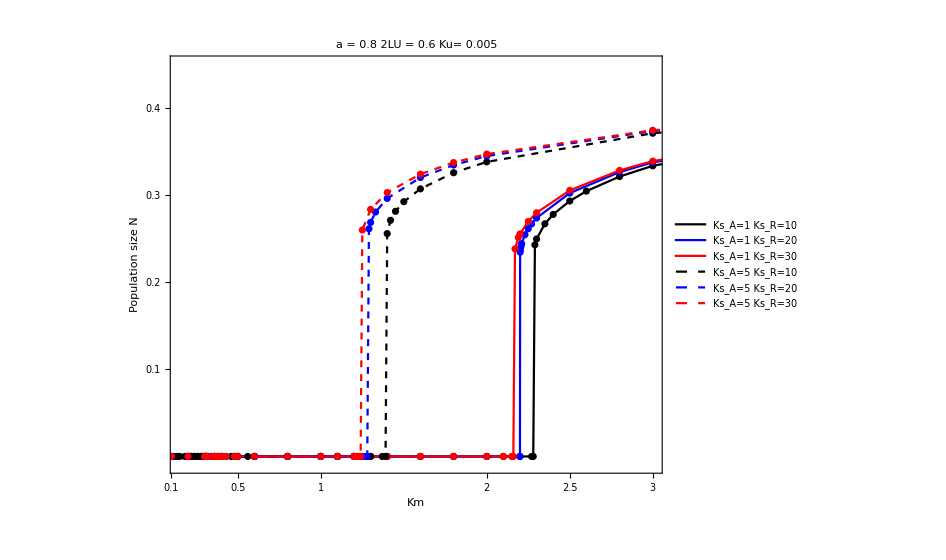

```mathematica
Fig5cAppendixGNoLog=ListPlot[{Transpose[{LENmLU03Ns1a1Ku0005⟦All,1⟧,LENmLU03Ns1a1Ku0005⟦All,2⟧⟦All,1⟧}],Transpose[{LENmLU03Ns1b1Ku0005⟦All,1⟧,LENmLU03Ns1b1Ku0005⟦All,2⟧⟦All,1⟧}],Transpose[{LENmLU03Ns1bb1Ku0005⟦All,1⟧,LENmLU03Ns1bb1Ku0005⟦All,2⟧⟦All,1⟧}],Transpose[{LENmLU03Ns1c1Ku0005⟦All,1⟧,LENmLU03Ns1c1Ku0005⟦All,2⟧⟦All,1⟧}],Transpose[{LENmLU03Ns1d1Ku0005⟦All,1⟧,LENmLU03Ns1d1Ku0005⟦All,2⟧⟦All,1⟧}],Transpose[{LENmLU03Ns1e1Ku0005⟦All,1⟧,LENmLU03Ns1e1Ku0005⟦All,2⟧⟦All,1⟧}]},Joined->True,Mesh->All,Frame->True,PlotLabel->Style["a = 0.8        2LU = 0.6        Ku= 0.005",30,FontFamily->"Times"],PlotStyle->{Black,Blue,Red,Directive[Black,Dashed],Directive[Blue,Dashed],Directive[Red,Dashed]},PlotRange->{{0.15,3},{-0.01,0.45}},Mesh->All,Frame->True,PlotLegends->Placed[{Style["Ks_A=1   Ks_R=10",26,FontFamily->"Times"],Style["Ks_A=1   Ks_R=20",26,FontFamily->"Times"],Style["Ks_A=1   Ks_R=30",26,FontFamily->"Times"],Style["Ks_A=5   Ks_R=10",26,FontFamily->"Times"],Style["Ks_A=5   Ks_R=20",26,FontFamily->"Times"],Style["Ks_A=5   Ks_R=30",26,FontFamily->"Times"]},{Left,Center}],FrameTicks->{{{0.1,0.2,0.3,0.4},None},{{0.05,0.1,0.5,1,2,2.5,3,5,10,20},None}},FrameTicksStyle->Directive[Times,30],FrameLabel->{Row[{Style["",30,Black,Bold],Style["   Km",30]},""],Row[{Style["Population size",30,Black,Bold],Style["  N",30]},""]},AspectRatio->0.8,ImageSize->700]
```